For the host-parasite system presented in the main text and all other model variants, we use standard adaptive dynamics techniques to investigate when a generalist parasite that can infect both hosts can “invade” (mathematically, this means investigating the stability of the equilibrium where the generalist is absent - the generalist can invade if this equilibrium is unstable). For all of the models we study, four assumptions remain constant: there are two potential hosts; infections occur due to contact between susceptible hosts and parasites in the environment; infected hosts shed parasites into the environment throughout the infection; generalist parasites have a reduced shedding rate compared to specialist parasites. 

The models differ in a number of ways that could affect the conclusions about the evolution of generalism. We explore three fundamentally different host-parasite systems: parasites with a direct life cycle where each host is infected by only a single parasite; parasites with a direct life cycle where coinfection is allowed; trophically transmitted parasites. Within each host-parasite system, we determine how each of the following factors influence the evolution of generalism: (1) the number of specialist parasites (either one or two); (2) the effect of parasites on host population growth (dynamic versus constant host population sizes); (3) whether the parasite comes in contact only with susceptible hosts. For (3), in all cases, we assume that the parasite is in control of the contact process (that is, that the parameter β depends on parasite traits), but that the parasite may come in contact only with susceptible hosts, or with all hosts, regardless of their infection status.

## Direct life cycle without coinfection

### Case 1: One specialist parasite; parasite regulates host population size; avoidance of infected hosts

For this model, let S_1 and S_2 be the number of susceptible hosts of species 1 and 2, respectively. We will refer to these the “primary” and “secondary” hosts for simplicity. We assume that the “resident” parasite is a specialist on the primary host, and let I_(1r) be the number of primary hosts infected by the resident parasite. The “mutant” parasite is a generalist, and we let I_(1m) and I_(2m) be the number of primary and secondary hosts infected by the mutant parasite. We let P_r and P_m be the number of resident (specialist) and mutant (generalist) parasites in the environment.

In the absence of any infection, the primary and secondary hosts population sizes reach species-specific carrying capacities K_1 and K_2. Infection, however, induces mortality that depends on host traits, quantified by the species-specific mortality rates μ_1 and μ_2. Infected hosts shed parasites into the environment. The rate of shedding depends on host traits and whether the host is infected by a generalist or a specialist. Primary hosts infected by the specialist parasite shed parasites at the rate λ_1 , whereas primary hosts infected by the generalist parasite shed parasites at the reduced rate a λ_1. Secondary hosts infected by the generalist parasite shed at the rate a λ_2 (where λ_2 is the rate that a specialist parasite would be shed). We assume that the parasite controls the infection process and can detect whether a host is infected or not, so that parasites in the environment come in contact with susceptible hosts at the rate β. Finally, we assume that parasites are lost from the environment (whether due to death or washout) at the rate γ.

Note that we have assumed that specialist and generalist parasites differ only in the rate that they are shed from infected hosts, rather than assuming that they differ in transmission (β) or mortality (μ). The model for this system is given below:

```mathematica
dS1dt=r1 (S1+I1r+I1m) (1-(S1+I1r+I1m)/K1)-β S1 (Pr+Pm);
dS2dt=r2 (S2+I2m) (1-(S2+I2m)/K2)-β S2 Pm;
dI1rdt=β S1 Pr-μ1 I1r;
dPrdt=λ1 I1r-β S1 Pr-γ Pr;
dI1mdt=β S1 Pm-μ1 I1m;
dI2mdt=β S2 Pm-μ2 I2m;
dPmdt=a λ1 I1m+a λ2 I2m-β S1 Pm-β S2 Pm-γ Pm;
```

For an invasion analysis, we assume that the resident parasite comes to an ecological equilibrium with the host. Since it does not parasitize the second host, it will go to its carrying capacity: S_2=K_2. The density of the exploited host at equilibrium will be S_1=(γ μ_1)/(β (λ_1-μ_1)).

```mathematica
Eq=Solve[({dS1dt==0,dI1rdt==0,dPrdt==0}/.{I1m->0,Pm->0}),{S1,I1r,Pr}];
Eq[[4,1]]
```

S1→-(γ μ1)/(β (-λ1+μ1))

While evaluating the stability of the endemic equilibrium is somewhat challenging, it is obvious that, for there to be any chance for the endemic parasite equilibrium to be stable, the parasite extinction equilibrium must be unstable. This requires (β K (λ_1-μ))/(γ μ)>1. Notice that this is the reciprocal of the equilibrium host abundance at the endemic equilibrium, as expected.

```mathematica
Jres={{D[dS1dt,S1],D[dS1dt,I1r],D[dS1dt,Pr]},
{D[dI1rdt,S1],D[dI1rdt,I1r],D[dI1rdt,Pr]},
{D[dPrdt,S1],D[dPrdt,I1r],D[dPrdt,Pr]}}/.{I1m->0,Pm->0};
(* Eigenvalues for the parasite-free equilibrium *)
Eigenvalues[Jres/.{I1r->0,Pr->0,S1->K1}]
```

{-r1,1/2 (-K1 β-γ-μ1-√((K1 β+γ+μ1)^2-4 (-K1 β λ1+K1 β μ1+γ μ1))),1/2 (-K1 β-γ-μ1+√((K1 β+γ+μ1)^2-4 (-K1 β λ1+K1 β μ1+γ μ1)))}

To determine whether the generalist parasite can invade, we need to examine the stability of the full system when the generalist parasite is absent (i.e., when I_(1,m)=0, I_(2,m)=0, and P_m=0). The Jacobian matrix for this is given below. Note that this matrix has a very simple structure: 
J=(J_s
0M
J_m)
This structure is actually quite convenient - J is an upper-triangular matrix, which means that its eigenvalues are given by the eigenvalues of J_s and J_m. The eigenvalues of J_s determine the stability of the endemic equilibria for the system with only the specialist parasite. By assumption, these eigenvalues are negative. Thus, we only need be concerned about the eigenvalues of J_m, which is the submatrix dealing with the equations for the generalist parasite.

```mathematica
J={{D[dS1dt,S1],D[dS1dt,S2],D[dS1dt,I1r],D[dS1dt,Pr],D[dS1dt,I1m],D[dS1dt,I2m],D[dS1dt,Pm]},
{D[dS2dt,S1],D[dS2dt,S2],D[dS2dt,I1r],D[dS2dt,Pr],D[dS2dt,I1m],D[dS2dt,I2m],D[dS2dt,Pm]},
{D[dI1rdt,S1],D[dI1rdt,S2],D[dI1rdt,I1r],D[dI1rdt,Pr],D[dI1rdt,I1m],D[dI1rdt,I2m],D[dI1rdt,Pm]},
{D[dPrdt,S1],D[dPrdt,S2],D[dPrdt,I1r],D[dPrdt,Pr],D[dPrdt,I1m],D[dPrdt,I2m],D[dPrdt,Pm]},
{D[dI1mdt,S1],D[dI1mdt,S2],D[dI1mdt,I1r],D[dI1mdt,Pr],D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,Pm]},
{D[dI2mdt,S1],D[dI2mdt,S2],D[dI2mdt,I1r],D[dI2mdt,Pr],D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,Pm]},
{D[dPmdt,S1],D[dPmdt,S2],D[dPmdt,I1r],D[dPmdt,Pr],D[dPmdt,I1m],D[dPmdt,I2m],D[dPmdt,Pm]}}/.{I1m->0,I2m->0,Pm->0};
MatrixForm[Jm=J[[5;;7,5;;7]]]
```

(-μ1 | 0 | 0
0 | -μ2 | 0
c λ1 | c λ2 | -I1r β1-S1 β1-S2 β2-γ)

However, rather than calculating the eigenvalues of this matrix directly, we apply the next generation theorem to calculate the spectral radius of the matrix F.V^-1, where J_m=F-V:

```mathematica
F={{0,0,S1 β},{0,0,S2 β},{a λ1,a λ2,0}};
V={{μ1,0,0},{0,μ2,0},{0,0,S1 β+S2 β+γ}};
J[[5;;7,5;;7]]==F-V//Simplify
Eigenvalues[Dot[F,Inverse[V]]]
```

True

{0,-(√a √β √(S2 λ2 μ1+S1 λ1 μ2))/(√(S1 β+S2 β+γ) √μ1 √μ2),(√a √β √(S2 λ2 μ1+S1 λ1 μ2))/(√(S1 β+S2 β+γ) √μ1 √μ2)}

If the largest of these eigenvalues (the spectral radius) is larger than 1, then the generalist-absent equilibrium is unstable. This is equivalent to requiring that (β (a λ_1-μ_1))/(γ μ_1)OverHat[S_1]+(β (a λ_1-μ_2))/(γ μ_2)OverHat[S_2]>1, where OverHat[S_1] and OverHat[S_2] are the equilibrium abundances of susceptible primary and secondary hosts when the generalist is absent. We can plug these equilibria into the stability condition. We define the left-hand side of this expression as R_0, the “invasion fitness” of the generalist parasite. Analogous to the canonical R_0 for an infectious disease, if R_0>1, the generalist will spread through the host population.

```mathematica
R0=((β (a λ1-μ1))/(γ μ1)S1+(β (a λ2-μ2))/(γ μ2)S2)/.{S1->-(γ μ1)/(β (-λ1+μ1)),S2->K2}
```

-(a λ1-μ1)/(-λ1+μ1)+(K2 β (a λ2-μ2))/(γ μ2)

We can explore how changing parameters of the model affect the magnitude of R_0 to see how these parameters affect the evolution of generalism. In particular, reducing the cost of generalism (increasing a) increases R_0; increasing the abundance of the secondary host (K_2) increases R_0; increasing the mortality induced by infection (μ_1 or μ_2) reduces R_0; increasing the parasite loss rate in the environment reduces R_0. None of these effects are surprising. However, in reality, many of these parameters are linked with one another by aspects of host physiology.

```mathematica
D[R0,a]//Simplify
D[R0,K2]
Simplify[D[R0,μ1]]
FullSimplify[D[R0,μ2]]
D[R0,γ]
```

λ1/(λ1-μ1)+(K2 β λ2)/(γ μ2)

(β (a λ2-μ2))/(γ μ2)

((-1+a) λ1)/(λ1-μ1)^2

-(a K2 β λ2)/(γ μ2^2)

-(K2 β (a λ2-μ2))/(γ^2 μ2)

In particular, carrying capacity, mortality rate, and shedding rate are all likely to be affected by host body size and temperature. Savage et al. 2004 suggested a scaling of 
K=K_0 e^(E/k T)W^-0.75
μ = μ_0 e^(-E/k T)W^-0.25
for carrying capacity and mortality rate.

Hechinger 2012 suggested that within-host abundance correlates with body size and temperature. If we assume that shedding rate is a linear function of abundance, then 
λ = λ_0 e^(-E/k T)W^0.75 (for endoparasites)
λ = λ_0 e^(-E/k T)W^(5/12) (for ectoparasites).
The difference in scaling for endoparasites and ectoparasites is because these two parasites utilize hosts differently: for endoparasites, abundance depends on host volume, whereas for ectoparasites, abundance depends on host surface area.

We assume that the only difference between the two hosts is in terms of body size. We let W be the mass of the primary host, and f W be the mass of the secondary host; without loss of generality, we assume that 0<f<1.

Notice that the derivatives of these expressions can be rewritten in terms of the expressions themselves, so that (∂K)/(∂W)=(-3K)/(4W), (∂μ)/(∂W)=-μ/(4 W), (∂r)/(∂W)=-r/(4 W) and (∂λ)/(∂W)=(3 λ)/(4 W) (for endoparasites) or (∂λ)/(∂W)=(5 λ)/(12 W) (for ectoparasites).
We can then study how R_0 is affected by changes in host body size or temperature for endoparasites and ectoparasites by differentiating R_0 with respect to host body size W and temperature T.

#### Endoparasites

For endoparasites, we find that increasing host body size always increases R_0 because dR_0/dW=((1-a) λ_1 μ_1)/(W(λ_1-μ_1))+(β K_2(a λ_2+3 μ_2))/(4 W γ μ_2), which is always positive.

```mathematica
(D[R0/.{λ1->λ1[W],μ1->μ1[W],λ2->λ2[W],μ2->μ2[W],K2->K2[W]},W]/.{μ1'[W]->(-μ1[W])/(4 W),μ2'[W]->(-μ2[W])/(4 W),K2'[W]->(-3 K2[W])/(4 W),λ1'[W]->(3 λ1[W])/(4 W),λ2'[W]->(3 λ2[W])/(4 W)})==((1-a) λ1[W] μ1[W])/(W (λ1[W]-μ1[W])^2)+(β K2[W] (a λ2[W]+3 μ2[W]))/(4 W γ μ2[W])//Simplify
```

True

We find that increasing temperature always decreases R_0 because dR_0/dT=(-β E K_2 (a λ_2-μ_2))/(k T^2 γ μ_2), which is always negative.

```mathematica
D[R0/.{λ1->λ1[T],μ1->μ1[T],λ2->λ2[T],μ2->μ2[T],K2->K2[T]},T]/.{μ1'[T]->Ε/(k T^2)μ1[T],λ1'[T]->Ε/(k T^2)λ1[T],K2'[T]->-Ε/(k T^2)K2[T],μ2'[T]->Ε/(k T^2)μ2[T],λ2'[T]->Ε/(k T^2)λ2[T]}//Simplify
```

(β Ε K2[T] (-a λ2[T]+μ2[T]))/(k T^2 γ μ2[T])

Thus, for endoparasites, we have that increasing the mass of the hosts (or making the masses more similar - since increasing f would increase the mass of the second host, it has the same sign as dR_0/dW) makes the evolution of generalism more likely, whereas increasing the temperature makes the evolution of generalism less likely.

#### Ectoparasites

For endoparasites, we find that increasing host body size has a more complicated effect. dR_0/dW=(2 (1-a) λ_1 μ_1)/(3 W(λ_1-μ_1))-(β K_2(a λ_2-9 μ_2))/(12 W γ μ_2); the sign of this expression depends on the sign of a λ_2-9 μ_2.

```mathematica
(D[R0/.{λ1->λ1[W],μ1->μ1[W],λ2->λ2[W],μ2->μ2[W],K2->K2[W]},W]/.{μ1'[W]->(-μ1[W])/(4 W),μ2'[W]->(-μ2[W])/(4 W),K2'[W]->(-3 K2[W])/(4 W),λ1'[W]->(5 λ1[W])/(12 W),λ2'[W]->(5 λ2[W])/(12 W)})==(2 (1-a) λ1[W] μ1[W])/(3 W (λ1[W]-μ1[W])^2)-(β K2[W] (a λ2[W]-9 μ2[W]))/(12 W γ μ2[W])//Simplify
```

True

We find that this expression will be negative whenever W<27/f(μ_0/(a λ_0))^(3/2), meaning that the derivative dR_0/dW>0. So, if host body size is small, increasing host size will make it easier for a generalist to invade. However, as host body size gets larger, eventually dR_0/dW<0.

```mathematica
Solve[(a λ2[W]-9 μ2[W]/.{μ2[W]->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ2[W]->λ0 Exp[-Ε/(k T)] (f W)^(5/12)})==0,W]
```

{{W→-(27 μ0^(3/2))/(a^(3/2) f λ0^(3/2))},{W→(27 μ0^(3/2))/(a^(3/2) f λ0^(3/2))}}

Increasing temperature has the same effect for an ectoparasite as an endoparasite.

### Case 2: Two specialist parasites; parasite regulates host population size; avoidance of infected hosts

For this model, let S_1 and S_2 be the number of susceptible hosts of species 1 and 2, respectively. We will refer to these the “primary” and “secondary” hosts for simplicity. We assume that there are two “resident” parasites, one specializing on the primary host and the other specializing on the secondary host. We let I_(1r) and I_(2 r) be the number of primary and secondary hosts infected by the resident parasites. The “mutant” parasite is a generalist, and we let I_(1m) and I_(2m) be the number of primary and secondary hosts infected by the mutant parasite. We let P_1, P_2 and P_m be the number of resident (specialist) and mutant (generalist) parasites in the environment.

The model for this system is given below.

```mathematica
dS1dt=r1 (S1+I1r+I1m) (1-(S1+I1r+I1m)/K1)-β1 S1 (P1r+P12m);
dI1rdt=β1 S1 P1r-μ1 I1r;
dP1rdt=λ1 I1r-β1 S1 P1r-γ1 P1r;

dS2dt=r2 (S2+I2r+I2m) (1-(S2+I2r+I2m)/K2)-β2 S2 (P2r+P12m);
dI2rdt=β2 S2 P2r-μ2 I2r;
dP2rdt=λ2 I2r-β2 S2 P2r-γ2 P2r;

dI1mdt=β1 S1 P12m-μ1 I1m;
dI2mdt=β2 S2 P12m-μ2 I2m;
dP12mdt=a λ1 I1m+a λ2 I2m-β1 S1 P12m-β2 S2 P12m-γ P12m;
```

Note that the specialist parasites do not have any interaction with one another (i.e., the dynamics of S_1,I_(1r), and P_1 do not depend on S_2,I_(2r,)or P_2). Since, for an invasion analysis, we assume that the resident parasites come to an ecological equilibrium with their hosts, we can solve for these equilibria easily, finding that S_1=(γ_1 μ_1)/(β_1 (λ_1-μ_1)) and S_2=(γ_2 μ_2)/(β_2(λ_2-μ_2)).

```mathematica
Eq=Solve[({dS1dt==0,dS2dt==0,dI1rdt==0,dI2rdt==0,dP1rdt==0,dP2rdt==0}/.{I1m->0,I2m->0,P12m->0}),{S1,S2,I1r,I2r,P1r,P2r}];
Eq[[13,1;;2]]
```

{S1→-(γ1 μ1)/(β1 (-λ1+μ1)),S2→-(γ2 μ2)/(β2 (-λ2+μ2))}

To determine whether the generalist parasite can invade, we need to examine the stability of the full system when the generalist parasite is absent (i.e., when I_(1m)=0, I_(2m)=0, and P_(12,m)=0). The Jacobian matrix for this is given below. Note that this matrix has a very simple structure: 
J=(J_1
0
00
J_2
0M_1
M_2
J_m)
This structure is actually quite convenient - J is an upper-triangular matrix, which means that its eigenvalues are given by the eigenvalues of J_1, J_2, and J_m. The eigenvalues J_1 and J_2 determine the stability of the endemic equilibria for the two specialist parasite. By assumption, these eigenvalues are negative. Thus, we only need be concerned about the eigenvalues of J_m, which is the submatrix dealing with the equations for the generalist parasite.

```mathematica
J={{D[dS1dt,S1],D[dS1dt,I1r],D[dS1dt,P1r],D[dS1dt,S2],D[dS1dt,I2r],D[dS1dt,P2r],D[dS1dt,I1m],D[dS1dt,I2m],D[dS1dt,P12m]},
{D[dI1rdt,S1],D[dI1rdt,I1r],D[dI1rdt,P1r],D[dI1rdt,S2],D[dI1rdt,I2r],D[dI1rdt,P2r],D[dI1rdt,I1m],D[dI1rdt,I2m],D[dI1rdt,P12m]},
{D[dP1rdt,S1],D[dP1rdt,I1r],D[dP1rdt,P1r],D[dP1rdt,S2],D[dP1rdt,I2r],D[dP1rdt,P2r],D[dP1rdt,I1m],D[dP1rdt,I2m],D[dP1rdt,P12m]},
{D[dS2dt,S1],D[dS2dt,I1r],D[dS2dt,P1r],D[dS2dt,S2],D[dS2dt,I2r],D[dS2dt,P2r],D[dS2dt,I1m],D[dS2dt,I2m],D[dS2dt,P12m]},
{D[dI2rdt,S1],D[dI2rdt,I1r],D[dI2rdt,P1r],D[dI2rdt,S2],D[dI2rdt,I2r],D[dI2rdt,P2r],D[dI2rdt,I1m],D[dI2rdt,I2m],D[dI2rdt,P12m]},
{D[dP2rdt,S1],D[dP2rdt,I1r],D[dP2rdt,P1r],D[dP2rdt,S2],D[dP2rdt,I2r],D[dP2rdt,P2r],D[dP2rdt,I1m],D[dP2rdt,I2m],D[dP2rdt,P12m]},
{D[dI1mdt,S1],D[dI1mdt,I1r],D[dI1mdt,P1r],D[dI1mdt,S2],D[dI1mdt,I2r],D[dI1mdt,P2r],D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,P12m]},
{D[dI2mdt,S1],D[dI2mdt,I1r],D[dI2mdt,P1r],D[dI2mdt,S2],D[dI2mdt,I2r],D[dI2mdt,P2r],D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,P12m]},
{D[dP12mdt,S1],D[dP12mdt,I1r],D[dP12mdt,P1r],D[dP12mdt,S2],D[dP12mdt,I2r],D[dP12mdt,P2r],D[dP12mdt,I1m],D[dP12mdt,I2m],D[dP12mdt,P12m]}}/.{I1m->0,I2m->0,P12m->0};
Jm=MatrixForm[J[[7;;9,7;;9]]]
```

(-μ1 | 0 | S1 β1
0 | -μ2 | S2 β2
a λ1 | a λ2 | -S1 β1-S2 β2-γ)

Rather than calculating the eigenvalues of J_m directly, we can use the next generation theorem (Hurford et al. 2010). Writing J_m=F-V, the stability of the system depends on the magnitude of the spectral radius of J.V^-1; if this is greater than 1, then the generalist-absent equilibrium is unstable and the generalist can invade.

```mathematica
F={{0,0,S1 β1},{0,0,S2 β2},{a λ1,a λ2,0}};
V={{μ1,0,0},{0,μ2,0},{0,0,S1 β1+S2 β2+γ}};
Dot[F,Inverse[V]]//MatrixForm
Eigenvalues[Dot[F,Inverse[V]]]
```

(0 | 0 | (S1 β1 μ1 μ2)/(S1 β1 μ1 μ2+S2 β2 μ1 μ2+γ μ1 μ2)
0 | 0 | (S2 β2 μ1 μ2)/(S1 β1 μ1 μ2+S2 β2 μ1 μ2+γ μ1 μ2)
(a λ1 (S1 β1 μ2+S2 β2 μ2+γ μ2))/(S1 β1 μ1 μ2+S2 β2 μ1 μ2+γ μ1 μ2) | (a λ2 (S1 β1 μ1+S2 β2 μ1+γ μ1))/(S1 β1 μ1 μ2+S2 β2 μ1 μ2+γ μ1 μ2) | 0)

{0,-(√a √(S2 β2 λ2 μ1+S1 β1 λ1 μ2))/(√(S1 β1+S2 β2+γ) √μ1 √μ2),(√a √(S2 β2 λ2 μ1+S1 β1 λ1 μ2))/(√(S1 β1+S2 β2+γ) √μ1 √μ2)}

The spectral radius of J.V^-1 is equal to:
((a λ_1-μ_1)β_1)/(μ_1 γ)OverHat[S_1]+((a λ_2-μ_2)β_2)/(μ_2 γ)OverHat[S_2]>1,
where OverHat[S_1] and OverHat[S_2] are the endemic equilibrium reached when only the specialist parasites are present. Interestingly, ((a λ_1-μ_1)β_1)/(μ_1 γ) is the reciprocal of the equilibrium abundance of the first host if the generalist parasite was the only parasite in the system and it only infected the first host; similarly, ((a λ_2-μ_2)β_2)/(μ_2 γ) is the reciprocal of the equilibrium abundance of the second host, if the generalist parasite was the only parasite in the system and it only infected the second host. Plugging in the equilibrium values for OverHat[S_1] and OverHat[S_2], the invasion condition simplifies to
(a λ_1-μ_1)/(λ_1-μ_1)+(a λ_2-μ_2)/(λ_2-μ_2)>1.

Notice that there are only three factors that influence whether a generalist parasite can invade or not: the cost of generalism a, the shedding rates λ_1 and λ_2, and the host mortality rates μ_1 and μ_2. In this model, the abundance of the hosts matters not at all, contrary to simple verbal theories for the evolution of generalism. Of course, this is because we assume that the parasite regulates the host population size. If that is not the case, we have a different model, one in which parasites can move hosts into an infected class, but do not cause mortality.

Regardless, we can use a similar analysis to study how changing the host body size or temperature will affect the ability of the generalist parasite to invade. Notice that because increasing the mass of the hosts increases shedding rates and decreases mortality rates, increasing host body size will still increase the likelihood that the generalist can invade, for both endoparasites and ectoparasites.

Effect of increasing body size for a generalist endoparasite:

```mathematica
Simplify[D[(a λ1[W]-μ1[W])/(λ1[W]-μ1[W]),W]/.{K1'[W]->(-3 K1[W])/(4 W),μ1'[W]->(-μ1[W])/(4 W),λ1'[W]->(3 λ1[W])/(4 W)}]
Simplify[D[(a λ2[W] -μ2[W])/(λ2[W]-μ2[W]),W]/.{K2'[W]->(-3 K2[W])/(4 W),μ2'[W]->(-μ2[W])/(4 W),λ2'[W]->(3 λ2[W])/(4 W)}]
```

-((-1+a) λ1[W] μ1[W])/(W (λ1[W]-μ1[W])^2)

-((-1+a) λ2[W] μ2[W])/(W (λ2[W]-μ2[W])^2)

Effect of increasing body size for a generalist ectoparasite:

```mathematica
Simplify[D[(a λ1[W]-μ1[W])/(λ1[W]-μ1[W]),W]/.{K1'[W]->(-3 K1[W])/(4 W),μ1'[W]->(-μ1[W])/(4 W),λ1'[W]->(5 λ1[W])/(12 W)}]
Simplify[D[(a λ2[W] -μ2[W])/(λ2[W]-μ2[W]),W]/.{K2'[W]->(-3 K2[W])/(4 W),μ2'[W]->(-μ2[W])/(4 W),λ2'[W]->(5 λ2[W])/(12 W)}]
```

-(2 (-1+a) λ1[W] μ1[W])/(3 W (λ1[W]-μ1[W])^2)

-(2 (-1+a) λ2[W] μ2[W])/(3 W (λ2[W]-μ2[W])^2)

However, for both endoparasites and ectoparasites, the invasion fitness is independent of temperature (because shedding rate and mortality rate scale with temperature in the same way):

```mathematica
D[(a λ1-μ1)/(λ1-μ1)+(a λ2-μ2)/(λ2-μ2)/.{μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4)},T]//Simplify
```

0

### Case 3: Two specialist parasites; parasite regulates host population size; no avoidance of infected hosts

For this model, let S_1 and S_2 be the number of susceptible hosts of species 1 and 2, respectively. We will refer to these the “primary” and “secondary” hosts for simplicity. We assume that there are two “resident” parasites, one specializing on the primary host and the other specializing on the secondary host. We let I_(1r) and I_(2 r) be the number of primary and secondary hosts infected by the resident parasites. The “mutant” parasite is a generalist, and we let I_(1m) and I_(2m) be the number of primary and secondary hosts infected by the mutant parasite. We let P_1, P_2 and P_m be the number of resident (specialist) and mutant (generalist) parasites in the environment.

The model for this system is given below.

```mathematica
dS1dt=r1 (S1+I1r+I1m) (1-(S1+I1r+I1m)/K1)-β1 S1 (P1r+P12m);
dI1rdt=β1 S1 P1r-μ1 I1r;
dP1rdt=λ1 I1r-β1 (S1+I1r) P1r-γ P1r;

dS2dt=r2 (S2+I2r+I2m) (1-(S2+I2r+I2m)/K2)-β2 S2 (P2r+P12m);
dI2rdt=β2 S2 P2r-μ2 I2r;
dP2rdt=λ2 I2r-β2 (S2+I2r) P2r-γ P2r;

dI1mdt=β1 S1 P12m-μ1 I1m;
dI2mdt=β2 S2 P12m-μ2 I2m;
dP12mdt=a λ1 I1m+a λ2 I2m-β1 (S1+I1r) P12m-β2 (S2+I2r) P12m-γ P12m;
```

To determine whether the generalist parasite can invade, we need to examine the stability of the full system when the generalist parasite is absent (i.e., when I_(1m)=0, I_(2m)=0, and P_(12,m)=0). The Jacobian matrix for this is given below. Note that this matrix has a very simple structure: 
J=(J_1
0
00
J_2
0M_1
M_2
J_m)
This structure is actually quite convenient - J is an upper-triangular matrix, which means that its eigenvalues are given by the eigenvalues of J_1, J_2, and J_m. The eigenvalues J_1 and J_2 determine the stability of the endemic equilibria for the two specialist parasite. By assumption, these eigenvalues are negative. Thus, we only need be concerned about the eigenvalues of J_m, which is the submatrix dealing with the equations for the generalist parasite.

```mathematica
J={{D[dS1dt,S1],D[dS1dt,I1r],D[dS1dt,P1r],D[dS1dt,S2],D[dS1dt,I2r],D[dS1dt,P2r],D[dS1dt,I1m],D[dS1dt,I2m],D[dS1dt,P12m]},
{D[dI1rdt,S1],D[dI1rdt,I1r],D[dI1rdt,P1r],D[dI1rdt,S2],D[dI1rdt,I2r],D[dI1rdt,P2r],D[dI1rdt,I1m],D[dI1rdt,I2m],D[dI1rdt,P12m]},
{D[dP1rdt,S1],D[dP1rdt,I1r],D[dP1rdt,P1r],D[dP1rdt,S2],D[dP1rdt,I2r],D[dP1rdt,P2r],D[dP1rdt,I1m],D[dP1rdt,I2m],D[dP1rdt,P12m]},
{D[dS2dt,S1],D[dS2dt,I1r],D[dS2dt,P1r],D[dS2dt,S2],D[dS2dt,I2r],D[dS2dt,P2r],D[dS2dt,I1m],D[dS2dt,I2m],D[dS2dt,P12m]},
{D[dI2rdt,S1],D[dI2rdt,I1r],D[dI2rdt,P1r],D[dI2rdt,S2],D[dI2rdt,I2r],D[dI2rdt,P2r],D[dI2rdt,I1m],D[dI2rdt,I2m],D[dI2rdt,P12m]},
{D[dP2rdt,S1],D[dP2rdt,I1r],D[dP2rdt,P1r],D[dP2rdt,S2],D[dP2rdt,I2r],D[dP2rdt,P2r],D[dP2rdt,I1m],D[dP2rdt,I2m],D[dP2rdt,P12m]},
{D[dI1mdt,S1],D[dI1mdt,I1r],D[dI1mdt,P1r],D[dI1mdt,S2],D[dI1mdt,I2r],D[dI1mdt,P2r],D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,P12m]},
{D[dI2mdt,S1],D[dI2mdt,I1r],D[dI2mdt,P1r],D[dI2mdt,S2],D[dI2mdt,I2r],D[dI2mdt,P2r],D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,P12m]},
{D[dP12mdt,S1],D[dP12mdt,I1r],D[dP12mdt,P1r],D[dP12mdt,S2],D[dP12mdt,I2r],D[dP12mdt,P2r],D[dP12mdt,I1m],D[dP12mdt,I2m],D[dP12mdt,P12m]}}/.{I1m->0,I2m->0,P12m->0};
```

The eigenvalues of this matrix determine the stability of the generalist-absent system.

```mathematica
MatrixForm[J[[7;;9,7;;9]]]
```

(-μ1 | 0 | S1 β1
0 | -μ2 | S2 β2
a λ1 | a λ2 | -(I1r+S1) β1-(I2r+S2) β2-γ)

Using the next generation theorem, we find that the stability of the system depends on the magnitude of (√a √(S2 β2 λ2 μ1+S1 β1 λ1 μ2))/(√(I1r β1+S1 β1+I2r β2+S2 β2+γ) √μ1 √μ2) - if this is greater than 1, then the generalist-absent equilibrium is unstable and the generalist can invade.

```mathematica
F={{0,0,S1 β1},{0,0,S2 β2},{a λ1,a λ2,0}};
V={{μ1,0,0},{0,μ2,0},{0,0,(I1r+S1) β1+(I2r+S2) β2+γ}};
Dot[F,Inverse[V]]//MatrixForm
Eigenvalues[Dot[F,Inverse[V]]]
```

(0 | 0 | (S1 β1)/((I1r+S1) β1+(I2r+S2) β2+γ)
0 | 0 | (S2 β2)/((I1r+S1) β1+(I2r+S2) β2+γ)
(a λ1 (I1r β1 μ2+S1 β1 μ2+I2r β2 μ2+S2 β2 μ2+γ μ2))/(((I1r+S1) β1+(I2r+S2) β2+γ) μ1 μ2) | (a λ2 (I1r β1 μ1+S1 β1 μ1+I2r β2 μ1+S2 β2 μ1+γ μ1))/(((I1r+S1) β1+(I2r+S2) β2+γ) μ1 μ2) | 0)

{0,-(√a √(S2 β2 λ2 μ1+S1 β1 λ1 μ2))/(√(I1r β1+S1 β1+I2r β2+S2 β2+γ) √μ1 √μ2),(√a √(S2 β2 λ2 μ1+S1 β1 λ1 μ2))/(√(I1r β1+S1 β1+I2r β2+S2 β2+γ) √μ1 √μ2)}

This condition can be rewritten as
R_m=(β_1 S_1)/(β_1 S_1+β_1 I_(1r)+γ) (a λ_1)/μ_1+(β_2 S_2)/(β_2 S_2+β_2 I_(2r)+γ)>1,
where OverHat[S_1], OverHat[S_2], OverHat[I_(1r)], and OverHat[I_(2r)] are the endemic equilibrium reached when only the specialist parasites are present.

```mathematica
Rm=((√a √(S2 β2 λ2 μ1+S1 β1 λ1 μ2))/(√(I1r β1+S1 β1+I2r β2+S2 β2+γ) √μ1 √μ2))^2;
```

The equilibria of this model are actually quite challenging to find, but it is possible to express the invasion fitness in terms of the abundances of the specialist parasites at equilibrium (OverHat[P_(1r)] and OverHat[P_(2r)]).

```mathematica
S1Eq=Solve[dI1rdt==0,S1];
I1rEq=Solve[(dP1rdt/.S1Eq[[1]])==0,I1r]
S1Eq=Simplify[S1Eq/.I1rEq[[1]]]
S2Eq=Solve[dI2rdt==0,S2];
I2rEq=Solve[(dP2rdt/.S2Eq[[1]])==0,I2r]
S2Eq=Simplify[S2Eq/.I2rEq[[1]]]
FullSimplify[Rm/.S1Eq[[1]]/.S2Eq[[1]]/.I1rEq[[1]]/.I2rEq[[1]]]
```

{{I1r→-(P1r γ)/(P1r β1-λ1+μ1)}}

{{S1→-(γ μ1)/(β1 (P1r β1-λ1+μ1))}}

{{I2r→-(P2r γ)/(P2r β2-λ2+μ2)}}

{{S2→-(γ μ2)/(β2 (P2r β2-λ2+μ2))}}

(a (P2r β2 λ1+λ2 (P1r β1-2 λ1+μ1)+λ1 μ2))/(-λ1 λ2+(P1r β1+μ1) (P2r β2+μ2))

The generalist parasite can only invade if the invasion fitness is greater than one. This requires that the numerator be larger than the denominator. Since 0<a<1, this can only happen if the inequality below is satisfied. However, from the equilibrium expressions for OverHat[S_1], OverHat[S_2], OverHat[I_(1r)], and OverHat[I_(2r)], we know that β_1 OverHat[P_(1r)]-λ_1+μ_1<0 and β_2 OverHat[P_(2r)]-λ_2+μ_2<0. Thus (β_1 OverHat[P_(1r)]-λ_1+μ_1)(β_2 OverHat[P_(2r)]-λ_2+μ_2)>0, and the inequality is never satisfied: the generalist parasite can never invade the system when already infected hosts remove parasites from the environment but do not yield any new spore production.

### Case 4: Two specialist parasites; constant host population size; avoidance of infected hosts

For this model, we assume that the primary and secondary host population sizes are constant at K_1 and K_2, respectively. As such, we do not need to keep track of the dynamics of both susceptible and infected hosts - we can simply track the prevalence of infection. We define I_(1r) and I_(2r) as the fraction of primary and secondary hosts infected by the specialist parasites, respectively. 

The dynamics of parasites in the environment are governed by shedding and loss, as before. The rate of shedding depends on the number of infected hosts, e.g., I_(1r)K_1. Similarly, loss due to contact with susceptible hosts depends on the number of susceptible hosts, e.g., (1-I_(1r)-I_(1m))K_1. 

The model is given below:

```mathematica
dI1rdt=β1 (1-I1r-I1m) P1r-μ1 I1r;
dP1rdt=λ1 I1r K1-β1 (1-I1r-I1m) K1 P1r -γ P1r;

dI2rdt=β2 (1-I2r-I2m) P2r-μ2 I2r;
dP2rdt=λ2 I2r K2-β2 (1-I2r-I2m) K2 P2r-γ P2r;

dI1mdt=β1 (1-I1r-I1m) P12m-μ1 I1m;
dI2mdt=β2 (1-I2r-I2m) P12m-μ2 I2m;
dP12mdt=a λ1 I1m K1 +a λ2 I2m K2 -β1 (1-I1r-I1m) K1  P12m-β2 (1-I2r-I2m) K2 P12m-γ P12m;
```

In the absence of the generalist parasite, the equilibrium prevalences of infection are I_(1,r)= 1 -(γ μ_1)/(β_1 K_1(λ_1-μ_1)) and I_(2,r)= 1-(γ μ_2)/(β_2 K_2(λ_2-μ_2)), implying that the equilibrium number of susceptibles are (γ μ_1)/(β_1 K_1(λ_1-μ_1)) and (γ μ_2)/(β_2 K_2(λ_2-μ_2)).

```mathematica
Eq=Solve[({dI1rdt==0,dP1rdt==0,dI2rdt==0,dP2rdt==0}/.{I1m->0,I2m->0}), {I1r,P1r,I2r,P2r}]//Simplify;
Eq[[4]]
```

{I1r→(K1 β1 λ1-K1 β1 μ1-γ μ1)/(K1 β1 λ1-K1 β1 μ1),P1r→(K1 β1 (λ1-μ1)-γ μ1)/(β1 γ),I2r→(K2 β2 λ2-K2 β2 μ2-γ μ2)/(K2 β2 λ2-K2 β2 μ2),P2r→(K2 β2 (λ2-μ2)-γ μ2)/(β2 γ)}

The Jacobian matrix for the full system is:

```mathematica
J={{D[dI1rdt,I1r],D[dI1rdt,P1r],D[dI1rdt,I2r],D[dI1rdt,P2r],D[dI1rdt,I1m],D[dI1rdt,I2m],D[dI1rdt,P12m]},
{D[dP1rdt,I1r],D[dP1rdt,P1r],D[dP1rdt,I2r],D[dP1rdt,P2r],D[dP1rdt,I1m],D[dP1rdt,I2m],D[dP1rdt,P12m]},
{D[dI2rdt,I1r],D[dI2rdt,P1r],D[dI2rdt,I2r],D[dI2rdt,P2r],D[dI2rdt,I1m],D[dI2rdt,I2m],D[dI2rdt,P12m]},
{D[dP2rdt,I1r],D[dP2rdt,P1r],D[dP2rdt,I2r],D[dP2rdt,P2r],D[dP2rdt,I1m],D[dP2rdt,I2m],D[dP2rdt,P12m]},
{D[dI1mdt,I1r],D[dI1mdt,P1r],D[dI1mdt,I2r],D[dI1mdt,P2r],D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,P12m]},
{D[dI2mdt,I1r],D[dI2mdt,P1r],D[dI2mdt,I2r],D[dI2mdt,P2r],D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,P12m]},
{D[dP12mdt,I1r],D[dP12mdt,P1r],D[dP12mdt,I2r],D[dP12mdt,P2r],D[dP12mdt,I1m],D[dP12mdt,I2m],D[dP12mdt,P12m]}}/.{I1m->0,I2m->0,P12m->0};
MatrixForm[J]
```

(-P1r β1-μ1 | (1-I1r) β1 | 0 | 0 | -P1r β1 | 0 | 0
K1 P1r β1+K1 λ1 | -(1-I1r) K1 β1-γ | 0 | 0 | K1 P1r β1 | 0 | 0
0 | 0 | -P2r β2-μ | (1-I2r) β2 | 0 | -P2r β2 | 0
0 | 0 | K2 P2r β2+K2 λ2 | -(1-I2r) K2 β2-γ | 0 | K2 P2r β2 | 0
0 | 0 | 0 | 0 | -μ1 | 0 | (1-I1r) β1
0 | 0 | 0 | 0 | 0 | -μ2 | (1-I2r) β2
0 | 0 | 0 | 0 | a K1 λ1 | a K2 λ2 | -(1-I1r) K1 β1-(1-I2r) K2 β2-γ)

As before, this has a upper block triangular structure, and whether the generalist can invade is entirely determined by the bottom left submatrix:

```mathematica
MatrixForm[J[[5;;7,5;;7]]]
```

(-μ1 | 0 | (1-I1r) β1
0 | -μ2 | (1-I2r) β2
a K1 λ1 | a K2 λ2 | -(1-I1r) K1 β1-(1-I2r) K2 β2-γ)

Applying the next generation matrix theorem, the generalist will be able to invade if the eigenvalue is greater than 1.

```mathematica
F={{0,0,(1-I1r) β1},{0,0,(1-I2r) β2},{a λ1 K1,a λ2 K2,0}};
V={{μ1,0,0},{0,μ2,0},{0,0,(1-I1r) K1 β1+(1-I2r)K2 β2+γ}};
Eigenvalues[Dot[F,Inverse[V]]]//Simplify
```

{0,-(√a √((-1+I2r) K2 β2 λ2 μ1+(-1+I1r) K1 β1 λ1 μ2))/(√((-1+I1r) K1 β1+(-1+I2r) K2 β2-γ) √μ1 √μ2),(√a √((-1+I2r) K2 β2 λ2 μ1+(-1+I1r) K1 β1 λ1 μ2))/(√((-1+I1r) K1 β1+(-1+I2r) K2 β2-γ) √μ1 √μ2)}

This condition can be simplified to
(β_1 K_1(a λ_1-μ_1))/(γ μ_1)(1-I_(1,r))+(β_2 K_2(a λ_2-μ_2))/(γ μ_2)(1-I_(2,r))>1,
which, after plugging in the generalist-free endemic equilibria for I_(1,r) and I_(2,r), simplifies to 
(a λ_1-μ_1)/(λ_1-μ_1)+(a λ_2-μ_2)/(λ_2-μ_2)>1

```mathematica
Simplify[(β1 K1(a λ1-μ1))/(γ μ1)(1-I1r)/.{I1r->(K1 β1 λ1-K1 β1 μ1-γ μ1)/(K1 β1 λ1-K1 β1 μ1)}]
Simplify[(β2 K2(a λ2-μ2))/(γ μ2)(1-I2r)/.{I2r->(K2 β2 λ2-K2 β2 μ2-γ μ2)/(K2 β2 λ2-K2 β2 μ2)}]
```

(a λ1-μ1)/(λ1-μ1)

(a λ2-μ2)/(λ2-μ2)

We can again see how changing host body size and temperature will affect invasion by looking at the derivatives of the invasion condition with respect to body size and temperature, after substituting in the allometric scaling relationships. Note that now you have a contravailing pressure of increasing body size on invasion fitness for the generalist: increasing host body size increases shedding rate, but decreases carrying capacity.

For an endoparasite, the derivative of the invasion fitness with respect to host body size is always positive because dR_0/dW=(1-a)/W((λ_1 μ_1)/(λ_1-μ_1)^2+(λ_2 μ_2)/(λ_2-μ_2)^2).

```mathematica
(D[(a λ1[W]-μ1[W])/(λ1[W]-μ1[W])+(a λ2[W] -μ2[W])/(λ2[W]-μ2[W]),W]/.{μ1'[W]->(-μ1[W])/(4 W),λ1'[W]->(3 λ1[W])/(4 W),μ2'[W]->(-μ2[W])/(4 W),λ2'[W]->(3 λ2[W])/(4 W)})==(1-a)/W((λ1[W] μ1[W])/(λ1[W]-μ1[W])^2+(λ2[W] μ2[W])/(λ2[W]-μ2[W])^2)//Simplify
```

True

Similarly, for an ectoparasite, the derivative of the invasion fitness with respect to host body size is always positive beacuse dR_0/dW=(2 (1-a))/(3 W)((λ_1 μ_1)/(λ_1-μ_1)^2+(λ_2 μ_2)/(λ_2-μ_2)^2).

```mathematica
Simplify[D[(a λ1[W]-μ1[W])/(λ1[W]-μ1[W])+(a λ2[W]-μ2[W])/(λ2[W]-μ2[W]),W]/.{μ1'[W]->(-μ1[W])/(4 W),λ1'[W]->(5 λ1[W])/(12 W),μ2'[W]->(-μ2[W])/(4 W),λ2'[W]->(5 λ2[W])/(12 W)}]==(2 (1-a))/(3 W)((λ1[W] μ1[W])/(λ1[W]-μ1[W])^2+(λ2[W] μ2[W])/(λ2[W]-μ2[W])^2)//Simplify
```

True

For both endoparasites and ectoparasites, the derivative of the invasion fitness with respect to temperature is zero, as before.

```mathematica
D[(a λ1[T] -μ1[T])/(λ1[T] -μ1[T])+(a λ2[T] -μ2[T])/(λ2[T] -μ2[T]),T]/.{μ2'[T]->(Ε μ2[T])/(k T^2),λ2'[T]->(Ε λ2[T])/(k T^2),μ1'[T]->(Ε μ1[T])/(k T^2),λ1'[T]->(Ε λ1[T])/(k T^2)}//Simplify
```

0

### Case 5: Two specialist parasites; constant host population size; no avoidance of infected hosts

The only change with the model above involves the loss of parasites due to contact with hosts. Since the parasite cannot determine whether a host is infected or not, the loss rate is, e.g., β K_1. Parasite consumption by an infected individual has no effect on infection status; if the parasite ends up in an already-infected host, it is simply lost from the system.

```mathematica
dI1rdt=β1 (1-I1r-I1m) P1r-μ1 I1r;
dP1rdt=λ1 I1r K1-β1 K1 P1r-γ P1r;

dI2rdt=β2 (1-I2r-I2m) P2r-μ2 I2r;
dP2rdt=λ2 I2r K2-β2 K2 P2r-γ P2r;

dI1mdt=β1 (1-I1r-I1m) P12m-μ1 I1m;
dI2mdt=β2 (1-I2r-I2m) P12m-μ2 I2m;
dP12mdt=a λ1 I1m K1 +a λ2 I2m K2 -β1 K1 P12m-β2 K2 P12m-γ P12m;
```

In the absence of the generalist parasite, the equilibrium prevalences of infection are I_(1,r)= 1-((K1 β1+γ) μ1)/(K1 β1 λ1) and I_(2,r)= 1-((K2 β2+γ) μ2)/(K2 β2 λ2).

```mathematica
Solve[({dI1rdt==0,dP1rdt==0,dI2rdt==0,dP2rdt==0}/.{I1m->0,I2m->0}), {I1r,P1r,I2r,P2r}]//Simplify
```

{{I1r→0,P1r→0,I2r→0,P2r→0},{I1r→1-((K1 β1+γ) μ1)/(K1 β1 λ1),P1r→(K1 β1 (λ1-μ1)-γ μ1)/(β1 (K1 β1+γ)),I2r→0,P2r→0},{I1r→0,P1r→0,I2r→1-((K2 β2+γ) μ2)/(K2 β2 λ2),P2r→(K2 β2 (λ2-μ2)-γ μ2)/(β2 (K2 β2+γ))},{I1r→1-((K1 β1+γ) μ1)/(K1 β1 λ1),P1r→(K1 β1 (λ1-μ1)-γ μ1)/(β1 (K1 β1+γ)),I2r→1-((K2 β2+γ) μ2)/(K2 β2 λ2),P2r→(K2 β2 (λ2-μ2)-γ μ2)/(β2 (K2 β2+γ))}}

Skipping ahead to the calculation of the Jacobian for the full system:

```mathematica
J={{D[dI1rdt,I1r],D[dI1rdt,P1r],D[dI1rdt,I2r],D[dI1rdt,P2r],D[dI1rdt,I1m],D[dI1rdt,I2m],D[dI1rdt,P12m]},
{D[dP1rdt,I1r],D[dP1rdt,P1r],D[dP1rdt,I2r],D[dP1rdt,P2r],D[dP1rdt,I1m],D[dP1rdt,I2m],D[dP1rdt,P12m]},
{D[dI2rdt,I1r],D[dI2rdt,P1r],D[dI2rdt,I2r],D[dI2rdt,P2r],D[dI2rdt,I1m],D[dI2rdt,I2m],D[dI2rdt,P12m]},
{D[dP2rdt,I1r],D[dP2rdt,P1r],D[dP2rdt,I2r],D[dP2rdt,P2r],D[dP2rdt,I1m],D[dP2rdt,I2m],D[dP2rdt,P12m]},
{D[dI1mdt,I1r],D[dI1mdt,P1r],D[dI1mdt,I2r],D[dI1mdt,P2r],D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,P12m]},
{D[dI2mdt,I1r],D[dI2mdt,P1r],D[dI2mdt,I2r],D[dI2mdt,P2r],D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,P12m]},
{D[dP12mdt,I1r],D[dP12mdt,P1r],D[dP12mdt,I2r],D[dP12mdt,P2r],D[dP12mdt,I1m],D[dP12mdt,I2m],D[dP12mdt,P12m]}}/.{I1m->0,I2m->0,P12m->0};
MatrixForm[J]
```

(-P1r β1-μ1 | (1-I1r) β1 | 0 | 0 | -P1r β1 | 0 | 0
K1 λ1 | -K1 β1-γ | 0 | 0 | 0 | 0 | 0
0 | 0 | -P2r β2-μ2 | (1-I2r) β2 | 0 | -P2r β2 | 0
0 | 0 | K2 λ2 | -K2 β2-γ | 0 | 0 | 0
0 | 0 | 0 | 0 | -μ1 | 0 | (1-I1r) β1
0 | 0 | 0 | 0 | 0 | -μ2 | (1-I2r) β2
0 | 0 | 0 | 0 | a K1 λ1 | a K2 λ2 | -K1 β1-K2 β2-γ)

As before, this has a upper block triangular structure, and whether the generalist can invade is entirely determined by the bottom left submatrix:

```mathematica
MatrixForm[J[[5;;7,5;;7]]]
```

(-μ1 | 0 | (1-I1r) β1
0 | -μ2 | (1-I2r) β2
a K1 λ1 | a K2 λ2 | -K1 β1-K2 β2-γ)

Applying the next generation matrix theorem, the generalist will be able to invade if the eigenvalue is greater than 1. This expression simplifies to

```mathematica
F={{0,0,(1-I1r) β1},{0,0,(1-I2r) β2},{a λ1 K1,a λ2 K2,0}};
V={{μ1,0,0},{0,μ2,0},{0,0,K1 β1+K2 β2+γ}};
Eigenvalues[Dot[F,Inverse[V]]]//Simplify
```

{0,-(ⅈ √a √((-1+I2r) K2 β2 λ2 μ1+(-1+I1r) K1 β1 λ1 μ2))/(√(K1 β1+K2 β2+γ) √μ1 √μ2),(ⅈ √a √((-1+I2r) K2 β2 λ2 μ1+(-1+I1r) K1 β1 λ1 μ2))/(√(K1 β1+K2 β2+γ) √μ1 √μ2)}

Notice that if you square the second eigenvalue, you get a positive real number - this is R_0 for the generalist for this system.

```mathematica
Rm=(-((ⅈ √a √((-1+I2r) K2 β2 λ2 μ1+(-1+I1r) K1 β1 λ1 μ2))/(√(K1 β1+K2 β2+γ) √μ1 √μ2)))^2
```

-(a ((-1+I2r) K2 β2 λ2 μ1+(-1+I1r) K1 β1 λ1 μ2))/((K1 β1+K2 β2+γ) μ1 μ2)

If you plug in the equilibrium values of I_(1r) and I_(2r), you end up with a very simple expression, which is the cost of generalism multiplied by 1 plus the probability that a parasite in the environment is lost rather than consumed (γ/(β_1 K_1+β_2 K_2+γ)).

```mathematica
Simplify[Rm/.{I1r->1-((K1 β1+γ) μ1)/(K1 β1 λ1),I2r->1-((K2 β2+γ) μ2)/(K2 β2 λ2)}]==a(1+γ/(β1 K1+β2 K2+γ))//Simplify
```

True

For an endoparasite, we again see that increasing body size increases the magnitude of the invasion exponent (because increasing body size decreases the carrying capacity, thereby increasing the probability that a parasite in the environment will be lost rather than consumed - this increases the benefit to being a generalist).

```mathematica
Simplify[D[a(1+γ/(β1 K1[W]+β2 K2[W]+γ)),W]/.{K1'[W]->(-3 K1[W])/(4 W),K2'[W]->(-3 K2[W])/(4 W)}]
```

(3 a γ (β1 K1[W]+β2 K2[W]))/(4 W (γ+β1 K1[W]+β2 K2[W])^2)

This is true for endoparasites as well:

```mathematica
Simplify[D[a(1+γ/(β1 K1[W]+β2 K2[W]+γ)),W]/.{K1'[W]->(-5 K1[W])/(12 W),K2'[W]->(-5 K2[W])/(12 W)}]
```

(5 a γ (β1 K1[W]+β2 K2[W]))/(12 W (γ+β1 K1[W]+β2 K2[W])^2)

Interestingly, now increasing temperature actually increases the likelihood that the generalist parasite can invade - warmer temperatures decrease carrying capacity, thereby making it more likely that a parasite in the environment ends up not infecting any host.

```mathematica
Simplify[D[a(1+γ/(β1 K1[T]+β2 K2[T]+γ)),T]/.{K1'[T]->-(Ε K1[W])/(k T^2),K2'[T]->-(Ε K2[W])/(k T^2)}]
```

(a γ Ε (β1 K1[W]+β2 K2[W]))/(k T^2 (γ+β1 K1[T]+β2 K2[T])^2)

## Direct life cycle with coinfection

There are a number of additional considerations when we allow for coinfection. In particular, as discussed at length in Alizon (2013), coinfection models can be biased towards the invading strain (in this case, the generalist), giving them a frequency-dependent advantage during the early stage of invasion. This frequency dependent bias arises when there are only 4 classes of host (susceptible, singly infected with the specialist strain, singly infected with the generalist strain, and coinfected), because the invading generalist can infect susceptible hosts and hosts infected with the specialist strain. The specialist strain can only infect susceptible hosts because the number of hosts singly infected with the generalist strain is negligible during early in the invasion. The proper way to deal with that is by allowing for double infection - that is, hosts that are singly infected with the specialist strain can become doubly infected with the resident strain, and those hosts are unavailable to be infected by the invading generalist. Although for symmetry it seems that we should also consider the dynamics of hosts that are doubly infected with the generalist strain, mathematically we do not need to do this because such double infections are rare. (In an invasion analysis, we are investigating the stability of the equilibrium where the generalist strain is absent. Since the number of new double infections will depend on contacts between singly infected hosts, I_g, and generalist parasites in the environment, P_g, the elements of the Jacobian matrix of partial derivatives, used to evaluate the stability of the generalist-free equilibrium, will be all zero.) In Appendix B, we show how to derive an unbiased coinfection model for a parasite transmitted through the environment.

We also need to consider the susceptibility of hosts to coinfection; that is, given a contact between a host and parasite, does that contact lead to a new infection? We let σ_1 be the probability that a contact between a singly infected host and a parasite results in a coinfection. Finally, we need to consider how shedding changes in doubly infected or coinfected hosts. As above, we assume that shedding rate is proportional to the body size of the host, because total parasite abundance is proportional to host size. Therefore, we assume that doubly infected hosts will shed at the same rate because the total parasite population size is set by the body size of the host. In coinfected hosts, however, the shedding rate of each of the coinfecting strains must be reduced by competition for host resources. That is, the total abundance of the strains is set by host body size; thus each parasite attains a population size that is reduced from the single infection case. We let the parameter x_1 be the fraction of host resources used by the specialist strain. This allows us to vary the strength of within-host competition between strains. If x_1=1/2, then the two strains equally partition the host resources, with each attaining half the total parasite abundance of a single infection.

### Case 1: One specialist parasite; parasite regulates host population size; avoidance of infected hosts

In this case, there are two host populations (the primary and secondary host). The primary host has a specialist parasite; the secondary host is currently unparasitized. There can be coinfections between the invading generalist parasite and the specialist parasite in the primary host. In the secondary host, there can only be single infections with the generalist parasite. To avoid biasing the model in favor of the invading strain, we must allow for double-infection of the specialist parasite in the primary host (see Alizon 2013 for a full account of why this is necessary). Thus we let S_1 be the number of susceptible primary hosts, I_(1r) be the number of primary hosts singly infected with the resident (specialist) strain, D_(1r r) be the number of primary hosts doubly infected with the resident strain, P_(1r) be the number of resident parasites in the environment, I_(1m) be the number of primary hosts singly infected with the mutant (generalist) strain, D_(1r m) be the number of coinfected primary hosts, S_2 be the number of susceptible secondary hosts, I_(2 m) be the number of secondary hosts singly infected with the mutant strain, and P_m be the number of mutant parasites in the environment. The dynamics of the full system are given below.

```mathematica
dS1dt=r1 (S1+I1r+D1rr+I1m+D1rm) (1-(S1+I1r+D1rr+I1m+D1rm)/K1)-β1 S1 (P1r+Pm);
dI1rdt=β1 S1 P1r-σ1 β1 I1r (P1r+Pm)-μ1 I1r;
dD1rrdt=σ1 β1 I1r P1r-μ1 D1rr;
dP1rdt=λ1 (I1r+D1rr+x1 D1rm)-β1 S1 P1r- β1 I1r P1r-β1 I1m P1r-γ P1r;
dS2dt=r2 (S2+I2m) (1-(S2+I2m)/K2)-β2 S2 Pm;

dI1mdt=β1 S1 Pm-σ1 β1 I1m P1r-μ1 I1m;
dI2mdt=β2 S2 Pm-μ2 I2m;
dD1rmdt=σ1 β1 I1r Pm+σ1 β1 I1m P1r-μ1 D1rm;
dPmdt=c (λ1 I1m+λ2 I2m+(1-x1) λ1 D1rm)-β1 S1 Pm-β2 S2 Pm-β1 I1r Pm-γ Pm;
```

Whether the mutant can invade will depend on the mutant Jacobian matrix:

```mathematica
MatrixForm[Jmut={{D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,D1rm],D[dI1mdt,Pm]},
{D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,D1rm],D[dI2mdt,Pm]},{D[dD1rmdt,I1m],D[dD1rmdt,I2m],D[dD1rmdt,D1rm],D[dD1rmdt,Pm]},
{D[dPmdt,I1m],D[dPmdt,I2m],D[dPmdt,D1rm],D[dPmdt,Pm]}}]
```

(-μ1-P1r β1 σ1 | 0 | 0 | S1 β1
0 | -μ2 | 0 | S2 β2
P1r β1 σ1 | 0 | -μ1 | I1r β1 σ1
c λ1 | c λ2 | c (1-x1) λ1 | -I1r β1-S1 β1-S2 β2-γ)

Applying the next generation theorem, whether there are any positive eigenvalues of the Jacobian can be assessed by studying the spectral radius of the matrix F.V^-1, where F-V=J_mut:

```mathematica
F={{0,0,0,Jmut[[1,4]]},
{0,0,0,Jmut[[2,4]]},
{Jmut[[3,1]],0,0,Jmut[[3,4]]},
{0,0,0,0}};
V=F-Jmut;
Simplify[Eigenvalues[Dot[F,Inverse[V]]]]
```

{0,0,(c S2 β2 λ2 μ1^2+c S1 β1 λ1 μ1 μ2+c P1r S2 β1 β2 λ2 μ1 σ1+c I1r β1 λ1 μ1 μ2 σ1-c I1r x1 β1 λ1 μ1 μ2 σ1+c I1r P1r β1^2 λ1 μ2 σ1^2-c I1r P1r x1 β1^2 λ1 μ2 σ1^2-√(c (-4 P1r S1 (-1+x1) β1^2 (I1r β1+S1 β1+S2 β2+γ) λ1 μ1 μ2^2 σ1 (μ1+P1r β1 σ1)+c (S2 β2 λ2 μ1 (μ1+P1r β1 σ1)+β1 λ1 μ2 (S1 μ1-I1r (-1+x1) σ1 (μ1+P1r β1 σ1)))^2)))/(2 (I1r β1+S1 β1+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1)),(c S2 β2 λ2 μ1^2+c S1 β1 λ1 μ1 μ2+c P1r S2 β1 β2 λ2 μ1 σ1+c I1r β1 λ1 μ1 μ2 σ1-c I1r x1 β1 λ1 μ1 μ2 σ1+c I1r P1r β1^2 λ1 μ2 σ1^2-c I1r P1r x1 β1^2 λ1 μ2 σ1^2+√(c (-4 P1r S1 (-1+x1) β1^2 (I1r β1+S1 β1+S2 β2+γ) λ1 μ1 μ2^2 σ1 (μ1+P1r β1 σ1)+c (S2 β2 λ2 μ1 (μ1+P1r β1 σ1)+β1 λ1 μ2 (S1 μ1-I1r (-1+x1) σ1 (μ1+P1r β1 σ1)))^2)))/(2 (I1r β1+S1 β1+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1))}

The mutant can invade if this spectral radius is greater than one. This invasion fitness can be expressed as:

```mathematica
Rm=(σ1 β1 I1r)/(S1 β1+S2 β2+I1r β1+γ) (c λ1 (1-x1))/μ1+(β1 S1)/(S1 β1+S2 β2+I1r β1+γ) (μ1/(σ1 β1 P1r+μ1) (c λ1)/μ1+(σ1 β1 P1r)/(σ1 β1 P1r+μ1) (c λ1 (1-x1))/μ1)+(β2 S2)/(S1 β1+S2 β2+I1r β1+γ)  (c λ2)/μ2;
```

The invasion condition depends on the equilibria of the system when the generalist parasite is absent. These equilibria are found below.

```mathematica
Solve[(dI1rdt/.{Pm->0})==0,S1];
Solve[(dD1rrdt/.{Pm->0})==0,I1r];
D1rrEq2=Solve[(dP1rdt/.{D1rm->0,I1m->0}/.{S1->(I1r μ1+I1r P1r β1 σ1)/(P1r β1)}/.{I1r->(D1rr μ1)/(P1r β1 σ1)})==0,D1rr]
I1rEq2=Solve[(dD1rrdt/.{Pm->0})==0,I1r]/.{D1rr->(P1r^2 β1 γ σ1)/(λ1 μ1-μ1^2+P1r β1 λ1 σ1-2 P1r β1 μ1 σ1)}
S1Eq2=Simplify[Solve[(dI1rdt/.{Pm->0})==0,S1]/.{I1r->(P1r γ μ1)/(λ1 μ1-μ1^2+P1r β1 λ1 σ1-2 P1r β1 μ1 σ1)}]
P1rEq2=Solve[Simplify[dS1dt/.{D1rm->0,I1m->0,Pm->0}/.{S1->(γ μ1 (μ1+P1r β1 σ1))/(β1 (λ1 (μ1+P1r β1 σ1)-μ1 (μ1+2 P1r β1 σ1)))}/.{I1r->(P1r γ μ1)/(λ1 μ1-μ1^2+P1r β1 λ1 σ1-2 P1r β1 μ1 σ1)}/.{D1rr->(P1r^2 β1 γ σ1)/(λ1 μ1-μ1^2+P1r β1 λ1 σ1-2 P1r β1 μ1 σ1)}]==0,P1r];

Solve[(dS2dt/.{I2m->0,Pm->0})==0,S2]
```

{{D1rr→(P1r^2 β1 γ σ1)/(-P1r β1 μ1+λ1 μ1-μ1^2+P1r β1 λ1 σ1-P1r β1 μ1 σ1)}}

{{I1r→(P1r γ μ1)/(λ1 μ1-μ1^2+P1r β1 λ1 σ1-2 P1r β1 μ1 σ1)}}

{{S1→(γ μ1 (μ1+P1r β1 σ1))/(β1 (λ1 (μ1+P1r β1 σ1)-μ1 (μ1+2 P1r β1 σ1)))}}

{{S2→0},{S2→K2}}

We can examine the invasion condition a bit more carefully. Focusing on the case where we fully allow coinfection (σ_1=1) and where coinfecting strains equally divide host resources (x_1=1/2), the invasion condition can be expressed in terms of the equilibrium abundance of specialist parasites in the environment.

```mathematica
FullSimplify[Rm/.D1rrEq2[[1]]/.I1rEq2[[1]]/.S1Eq2[[1]]/.S2->K2/.{σ1->1,x1->1/2}]
```

(c (K2 β2 λ2 (P1r β1 (λ1-2 μ1)+(λ1-μ1) μ1)+γ λ1 (P1r β1+μ1) μ2))/((γ λ1 (P1r β1+μ1)+K2 β2 (P1r β1 (λ1-2 μ1)+(λ1-μ1) μ1)) μ2)

Notice that the numerator must be greater than than the denominator before accounting for the cost of generalism (c) for the generalist to ever be able to invade. This requires that (β_1 P_(1r)(λ_1-2 μ_1)+(λ_1-μ_1) μ_1)>0, which is guaranteed by the fact that OverHat[S_1]>0 requires that to be true as well.

```mathematica
K2 β2 λ2 (P1r β1 (λ1-2 μ1)+(λ1-μ1) μ1)+γ λ1 (P1r β1+μ1) μ2>(γ λ1 (P1r β1+μ1)+K2 β2 (P1r β1 (λ1-2 μ1)+(λ1-μ1) μ1)) μ2//Simplify
λ1 (μ1+P1r β1 σ1)-μ1 (μ1+2 P1r β1 σ1)==P1r β1 (λ1-2 μ1)+(λ1-μ1) μ1/.σ1->1//Simplify
```

K2 β2 (P1r β1 (λ1-2 μ1)+(λ1-μ1) μ1) (λ2-μ2)>0

True

The question at hand is how changing host traits like body size influences the magnitude of the generalist’s fitness. We can assess this by taking the derivative of R_m with respect to host body size. As was the case in the model without coinfection, we assume that the host’s carrying capacity K, mortality rate μ, and reproductive rate r are functions of the host’s body size and temperature. In particular, carrying capacity, mortality rate, and shedding rate are all likely to be affected by host body size and temperature. Savage et al. 2004 suggested a scaling of 
K=K_0 e^(E/k T)W^-0.75
μ = μ_0 e^(-E/k T)W^-0.25’
r=r_0 e^(-E/k T)W^-0.25,
for host carrying capacity, mortality rate, and reprodutive rate.

Hechinger 2012 suggested that within-host abundance correlates with body size and temperature. If we assume that shedding rate is a linear function of abundance, then 
λ = λ_0 e^(-E/k T)W^0.75 (for endoparasites)
λ = λ_0 e^(-E/k T)W^(5/12) (for ectoparasites).
The difference in scaling for endoparasites and ectoparasites is because these two parasites utilize hosts differently: for endoparasites, abundance depends on host volume, whereas for ectoparasites, abundance depends on host surface area.

We assume that the only difference between the two hosts is in terms of body size. We let W be the mass of the primary host, and f W be the mass of the secondary host; without loss of generality, we assume that 0<f<1.

Notice that the derivatives of these expressions can be rewritten in terms of the expressions themselves, so that (∂K)/(∂W)=(-3K)/(4W), (∂μ)/(∂W)=-μ/(4 W), (∂r)/(∂W)=-r/(4 W) and (∂λ)/(∂W)=(3 λ)/(4 W) (for endoparasites) or (∂λ)/(∂W)=(5 λ)/(12 W) (for ectoparasites).

We can include these allometric relationships into the expression for invasion fitness R_m. Taking the derivative of R_m with respect to W, then, allows us to investigate the effect of increasing host mass on parasite invasion success. We do this for the case of an endoparasite:

```mathematica
dRmdW=Simplify[D[Simplify[Rm/.D1rrEq2[[1]]/.I1rEq2[[1]]/.S1Eq2[[1]]/.S2->K2/.{x1->1/2,σ1->1}]/.{λ1->λ1[W],λ2->λ2[W],μ1->μ1[W],μ2->μ2[W],K2->K2[W],P1r->P1r[W],P2r->P2r[W]},W]/.{μ2'[W]->(-μ2[W])/(4 W),λ2'[W]->(3 λ2[W])/(4 W),μ1'[W]->(-μ1[W])/(4 W),λ1'[W]->(3 λ1[W])/(4 W),K2'[W]->-(3 K2[W])/(4 W)}]
```

(c β2 K2[W] (β1^2 P1r[W]^2 (16 β2 K2[W] λ2[W] μ1[W]^2+2 λ1[W] μ1[W] ((3 γ-8 β2 K2[W]) λ2[W]-7 γ μ2[W])+λ1[W]^2 ((γ+4 β2 K2[W]) λ2[W]+3 γ μ2[W]))+2 β1 P1r[W] μ1[W] (8 β2 K2[W] λ2[W] μ1[W]^2+2 λ1[W] μ1[W] (2 (γ-3 β2 K2[W]) λ2[W]-5 γ μ2[W])+λ1[W]^2 ((γ+4 β2 K2[W]) λ2[W]+3 γ μ2[W]))+μ1[W]^2 (4 β2 K2[W] λ2[W] μ1[W]^2+λ1[W]^2 ((γ+4 β2 K2[W]) λ2[W]+3 γ μ2[W])+λ1[W] (γ μ2[W] (-7 μ1[W]+4 W β1 P1r'[W])+λ2[W] (3 γ μ1[W]-8 β2 K2[W] μ1[W]-4 W β1 γ P1r'[W])))))/(4 W (β1 P1r[W] ((γ+β2 K2[W]) λ1[W]-2 β2 K2[W] μ1[W])+μ1[W] ((γ+β2 K2[W]) λ1[W]-β2 K2[W] μ1[W]))^2 μ2[W])

It is analytically intractable to determine the sign of ∂R_m/∂W, so we use numerical exploration to determine the effect of host body size (and environmental temperature) on the invasion fitness of the generalist. We will do this for two types of parasites: endoparasites, whose internal abundance scales with host body mass as W^(3/4), and ectoparasites, whose internal abundance scales with host body mass as W^(5/12).

#### Ectoparasites:

Many of the parameters of the model are set by the allometric relationships (Gillooly et al. 2001, Allen et al. 2002, Savage et al. 2004, Poulin & George-Nascimento 2007), and thus can be set to biologically reasonable values.

```mathematica
allom={K1->K0 Exp[0.78/(k T)] W^(-3/4),K2->K0 Exp[0.78/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-0.43/(k T)] W^(-1/4),μ2->μ0 Exp[-0.43/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-0.43/(k T)] W^(5/12),λ2->λ0 Exp[-0.43/(k T)] (f W)^(5/12),r1->r0 Exp[-0.43/(k T)] W^(-1/4),r2->r0 Exp[-0.43/(k T)] (f W)^(-1/4)};
allompars={k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10};
```

That leaves a much smaller subset of parameters that can be varied. For simplicity, we focus on parameters whose effects on invasion fitness are indeterminate. This excludes parameters related to the costs associated with generalism, including c (the reduction in shedding rate for generalists), σ_1 (the probability of coinfection, which hold constant at 1), and x_1 (the fraction of host resources captured by the resident strains in coinfection). None of these parameters affect the equilibrium abundances of susceptible and singly infected hosts, so their effect on R_m are predictable and obvious - reducing c, reducing σ_1, or increasing x_1 will all reduce R_m, making invasion more difficult. Thus the only parameters to explore (other than host mass W and temperature T), are β (the contact rate between hosts and parasites, which is assumed to be dependent on the parasite and thus equal for both hosts) and γ (the loss rate of parasites from the environment).

Varying W and β:

```mathematica
RmAcrossWB=Table[Table[Rm/.I1rEq2[[1]]/.S1Eq2[[1]]/.P1rEq2[[2]]/.S2->K2/.allom/.allompars/.{β1->B,β2->B,γ->0.1,σ2->1,σ1->1,f->0.9,c->0.8,x1->1/2,x2->1/2,W->Wval,T->270},{Wval,10,1010,100}],{B,0.01,1.01,0.1}];
```

Increasing host body size increases invasion fitness, regardless of the value of β, thereby making it easier for the generalist to invade.

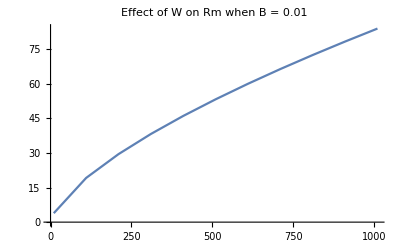
-Graphics-Host massRm

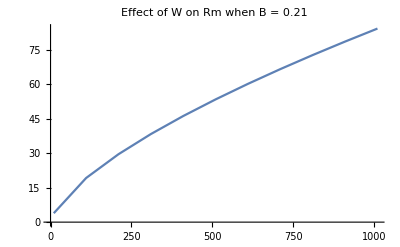
-Graphics-Host massRm

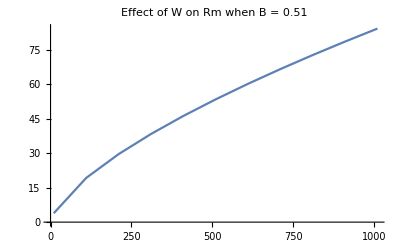
-Graphics-Host massRm

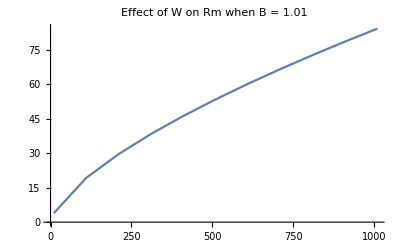
-Graphics-Host massRm

```mathematica
Wvals=Table[W,{W,10,1010,100}];
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[1,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when B = 0.01"],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[3,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when B = 0.21"],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[6,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when B = 0.51"],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[11,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when B = 1.01"],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
```

Varying W and γ:

```mathematica
RmAcrossWg=Table[Table[Rm/.I1rEq2[[1]]/.S1Eq2[[1]]/.P1rEq2[[2]]/.S2->K2/.allom/.allompars/.{β1->0.1,β2->0.1,γ->g,σ2->1,σ1->1,f->0.9,c->0.8,x1->1/2,x2->1/2,W->Wval,T->270},{Wval,10,1010,100}],{g,0.01,1.01,0.1}];
```

Increasing host body size increases invasion fitness, regardless of the value of γ, thereby making it easier for the generalist to invade.

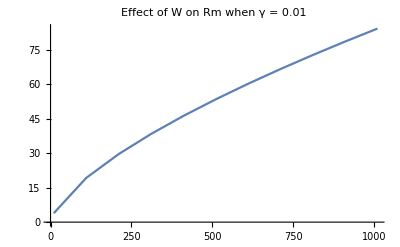
-Graphics-Host massRm

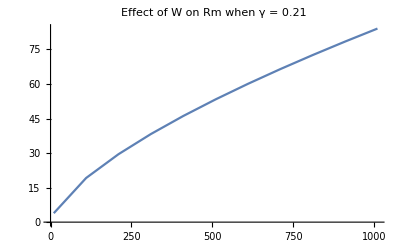
-Graphics-Host massRm

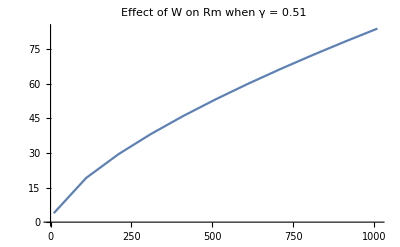
-Graphics-Host massRm

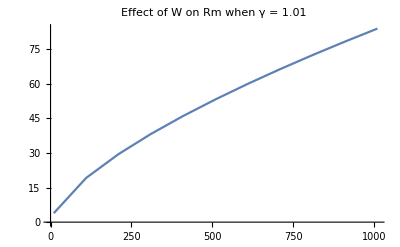
-Graphics-Host massRm

```mathematica
Wvals=Table[W,{W,10,1010,100}];
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[1,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when γ = 0.01"],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[3,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when γ = 0.21"],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[6,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when γ = 0.51"],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[11,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when γ = 1.01"],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
```

The effect of mass and temperature:

```mathematica
RmAcrossWT=Table[Table[Rm/.I1rEq2[[1]]/.S1Eq2[[1]]/.P1rEq2[[2]]/.S2->K2/.allom/.allompars/.{β1->0.1,β2->0.1,γ->0.1,σ2->1,σ1->1,f->0.9,c->0.8,x1->1/2,x2->1/2,W->Wval,T->Tval},{Tval,270,310,5}],{Wval,10,1010,100}];
```

Increasing temperature decreases the invasion fitness, regardless of host mass, thus making it more difficult for the generalist endoparasite to invade.

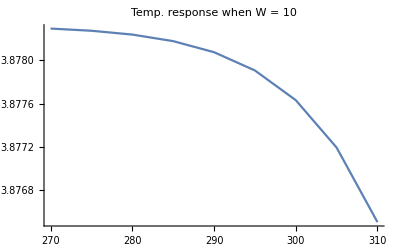
-Graphics-TemperatureRm

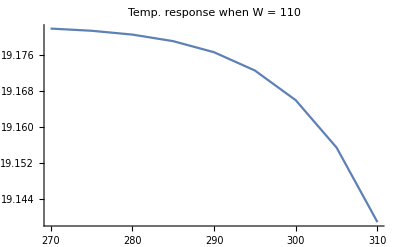
-Graphics-TemperatureRm

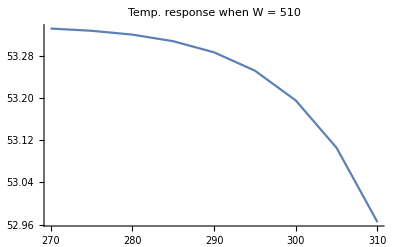
-Graphics-TemperatureRm

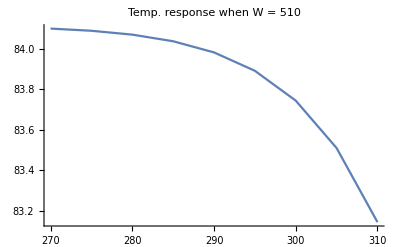
-Graphics-TemperatureRm

```mathematica
Tvals=Table[T,{T,270,310,5}];
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[1,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Temp. response when W = 10"],{"Temperature","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[2,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Temp. response when W = 110"],{"Temperature","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[6,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Temp. response when W = 510"],{"Temperature","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[11,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Temp. response when W = 510"],{"Temperature","Rm"},{Bottom,Left},RotateLabel->True]
```

### Case 2: Two specialist parasites; parasites regulate host population sizes; avoidance of infected hosts

This model extends the previous one by considering that the second host is also parasitized by a specialist parasite. Thus we extend the model to consider the dynamics of S_2, the number of susceptible secondary hosts; I_(2r), the number of secondary hosts singly infected with the resident (specialist) strain; D_(2r r), the number of secondary hosts doubly infected with the resident strain; P_(2r), the number of secondary host specialist parasites in the environment; and D_(2r m), the number of coinfected secondary hosts. The dynamics of the full system are given below.

```mathematica
dS1dt=r1 (S1+I1r+D1rr+I1m+D1rm) (1-(S1+I1r+D1rr+I1m+D1rm)/K1)-β1 S1 (P1r+Pm);
dI1rdt=β1 S1 P1r-σ1 β1 I1r (P1r+Pm)-μ1 I1r;
dD1rrdt=σ1 β1 I1r P1r-μ1 D1rr;
dP1rdt=λ1 (I1r+D1rr+x1 D1rm)-β1 S1 P1r- β1 I1r P1r-β1 I1m P1r-γ P1r;
dS2dt=r2 (S2+I2r+D2rr+I2m+D2rm) (1-(S2+I2r+D2rr+I2m+D2rm)/K2)-β2 S2 (P2r+Pm);
dI2rdt=β2 S2 P2r-σ2 β2 I2r (P2r+Pm)-μ2 I2r;
dD2rrdt=σ2 β2 I2r P2r-μ2 D2rr;
dP2rdt=λ2 (I2r+D2rr+x2 D2rm)-β2 S2 P2r- β2 I2r P2r- β2 I2m P2r-γ P2r;

dI1mdt=β1 S1 Pm-σ1 β1 I1m P1r-μ1 I1m;
dI2mdt=β2 S2 Pm-σ2 β2 I2m P2r-μ2 I2m;
dD1rmdt=σ1 β1 I1r Pm+σ1 β1 I1m P1r-μ1 D1rm;
dD2rmdt=σ2 β2 I2r Pm+σ2 β2 I2m P2r-μ2 D2rm;
dPmdt=c (λ1 I1m+λ2 I2m+(1-x1) λ1 D1rm+(1-x2) λ2 D2rm)-β1 S1 Pm-β2 S2 Pm-β1 I1r Pm-β2 I2r Pm-γ Pm;
```

Whether the mutant can invade will depend on the mutant Jacobian matrix:

```mathematica
MatrixForm[Jmut={{D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,D1rm],D[dI1mdt,D2rm],D[dI1mdt,Pm]},
{D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,D1rm],D[dI2mdt,D2rm],D[dI2mdt,Pm]},{D[dD1rmdt,I1m],D[dD1rmdt,I2m],D[dD1rmdt,D1rm],D[dD1rmdt,D2rm],D[dD1rmdt,Pm]},
{D[dD2rmdt,I1m],D[dD2rmdt,I2m],D[dD2rmdt,D1rm],D[dD2rmdt,D2rm],D[dD2rmdt,Pm]},
{D[dPmdt,I1m],D[dPmdt,I2m],D[dPmdt,D1rm],D[dPmdt,D2rm],D[dPmdt,Pm]}}]
```

(-μ1-P1r β1 σ1 | 0 | 0 | 0 | S1 β1
0 | -μ2-P2r β2 σ2 | 0 | 0 | S2 β2
P1r β1 σ1 | 0 | -μ1 | 0 | I1r β1 σ1
0 | P2r β2 σ2 | 0 | -μ2 | I2r β2 σ2
c λ1 | c λ2 | c (1-x1) λ1 | c (1-x2) λ2 | -I1r β1-S1 β1-I2r β2-S2 β2-γ)

Applying the next generation theorem, there will be a positive eigenvalue of the mutant Jacobian so long as the spectral radius of the matrix F.V^-1>1, where J_mut=F-V.

```mathematica
F={{0,0,0,0,Jmut[[1,5]]},
{0,0,0,0,Jmut[[2,5]]},
{Jmut[[3,1]],0,0,0,Jmut[[3,5]]},
{0,Jmut[[4,2]],0,0,Jmut[[4,5]]},
{0,0,0,0,0}};
V=F-Jmut;
MatrixForm[Dot[F,Inverse[V]]]
Simplify[Eigenvalues[Dot[F,Inverse[V]]]]
```

((S1 β1 (c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2))/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (S1 β1 (c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1))/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c S1 (1-x1) β1 λ1)/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1) | (c S1 (1-x2) β1 λ2)/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ2) | (S1 β1)/(I1r β1+S1 β1+I2r β2+S2 β2+γ)
(S2 β2 (c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2))/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (S2 β2 (c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1))/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c S2 (1-x1) β2 λ1)/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1) | (c S2 (1-x2) β2 λ2)/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ2) | (S2 β2)/(I1r β1+S1 β1+I2r β2+S2 β2+γ)
(P1r β1 σ1 (μ1 μ2^2+P2r β2 μ1 μ2 σ2))/(μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))+(I1r β1 σ1 (c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2))/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (I1r β1 σ1 (c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1))/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c I1r (1-x1) β1 λ1 σ1)/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1) | (c I1r (1-x2) β1 λ2 σ1)/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ2) | (I1r β1 σ1)/(I1r β1+S1 β1+I2r β2+S2 β2+γ)
(I2r β2 σ2 (c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2))/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (P2r β2 (μ1^2 μ2+P1r β1 μ1 μ2 σ1) σ2)/(μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))+(I2r β2 (c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1) σ2)/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c I2r (1-x1) β2 λ1 σ2)/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1) | (c I2r (1-x2) β2 λ2 σ2)/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ2) | (I2r β2 σ2)/(I1r β1+S1 β1+I2r β2+S2 β2+γ)
0 | 0 | 0 | 0 | 0)

{0,0,0,(c S2 β2 λ2 μ1^2 μ2+c S1 β1 λ1 μ1 μ2^2+c P1r S2 β1 β2 λ2 μ1 μ2 σ1+c I1r β1 λ1 μ1 μ2^2 σ1-c I1r x1 β1 λ1 μ1 μ2^2 σ1+c I1r P1r β1^2 λ1 μ2^2 σ1^2-c I1r P1r x1 β1^2 λ1 μ2^2 σ1^2+c P2r S1 β1 β2 λ1 μ1 μ2 σ2+c I2r β2 λ2 μ1^2 μ2 σ2-c I2r x2 β2 λ2 μ1^2 μ2 σ2+c I1r P2r β1 β2 λ1 μ1 μ2 σ1 σ2-c I1r P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2+c I2r P1r β1 β2 λ2 μ1 μ2 σ1 σ2-c I2r P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2+c I1r P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2-c I1r P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2+c I2r P2r β2^2 λ2 μ1^2 σ2^2-c I2r P2r x2 β2^2 λ2 μ1^2 σ2^2+c I2r P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2-c I2r P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2-√(c (-4 (I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) (P2r S2 (-1+x2) β2^2 λ2 μ1^2 σ2+P1r β1 σ1 (P2r S2 (-1+x2) β2^2 λ2 μ1 σ2+S1 (-1+x1) β1 λ1 μ2 (μ2+P2r β2 σ2)))+c (S2 β2 λ2 μ1 μ2 (μ1+P1r β1 σ1)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ1 μ2-(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2)))^2)))/(2 (I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),(c S2 β2 λ2 μ1^2 μ2+c S1 β1 λ1 μ1 μ2^2+c P1r S2 β1 β2 λ2 μ1 μ2 σ1+c I1r β1 λ1 μ1 μ2^2 σ1-c I1r x1 β1 λ1 μ1 μ2^2 σ1+c I1r P1r β1^2 λ1 μ2^2 σ1^2-c I1r P1r x1 β1^2 λ1 μ2^2 σ1^2+c P2r S1 β1 β2 λ1 μ1 μ2 σ2+c I2r β2 λ2 μ1^2 μ2 σ2-c I2r x2 β2 λ2 μ1^2 μ2 σ2+c I1r P2r β1 β2 λ1 μ1 μ2 σ1 σ2-c I1r P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2+c I2r P1r β1 β2 λ2 μ1 μ2 σ1 σ2-c I2r P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2+c I1r P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2-c I1r P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2+c I2r P2r β2^2 λ2 μ1^2 σ2^2-c I2r P2r x2 β2^2 λ2 μ1^2 σ2^2+c I2r P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2-c I2r P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2+√(c (-4 (I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) (P2r S2 (-1+x2) β2^2 λ2 μ1^2 σ2+P1r β1 σ1 (P2r S2 (-1+x2) β2^2 λ2 μ1 σ2+S1 (-1+x1) β1 λ1 μ2 (μ2+P2r β2 σ2)))+c (S2 β2 λ2 μ1 μ2 (μ1+P1r β1 σ1)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ1 μ2-(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2)))^2)))/(2 (I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))}

The mutant can invade if the spectral radius is greater than one. The spectral radius can be reexpressed as the invasion fitness expression:

```mathematica
Rm=(σ1 β1 I1r)/(S1 β1+S2 β2+I1r β1+I2r β2+γ) (c λ1 (1-x1))/μ1+(β1 S1)/(S1 β1+S2 β2+I1r β1+I2r β2+γ) (μ1/(σ1 β1 P1r+μ1) (c λ1)/μ1+(σ1 β1 P1r)/(σ1 β1 P1r+μ1) (c λ1 (1-x1))/μ1)+(σ2 β2 I2r)/(S1 β1+S2 β2+I1r β1+I2r β2+γ) (c λ2 (1-x2))/μ2+(β2 S2)/(S1 β1+S2 β2+I1r β1+I2r β2+γ) (μ2/(σ2 β2 P2r+μ2) (c λ2)/μ2+(σ2 β2 P2r)/(σ2 β2 P2r+μ2) (c λ2 (1-x2))/μ2);
```

The invasion fitness depends on the equilibria of the system when the generalist parasite is absent. These equilibria are found below.

```mathematica
Solve[(dI1rdt/.{Pm->0})==0,S1];
Solve[(dD1rrdt/.{Pm->0})==0,I1r];
D1rrEq2=Solve[(dP1rdt/.{D1rm->0,I1m->0}/.{S1->(I1r μ1+I1r P1r β1 σ1)/(P1r β1)}/.{I1r->(D1rr μ1)/(P1r β1 σ1)})==0,D1rr]
I1rEq2=Solve[(dD1rrdt/.{Pm->0})==0,I1r]/.D1rrEq2[[1]]
S1Eq2=Simplify[Solve[(dI1rdt/.{Pm->0})==0,S1]/.I1rEq2[[1]]]
P1rEq2=Solve[Simplify[dS1dt/.{D1rm->0,I1m->0,Pm->0}/.S1Eq2[[1]]/.I1rEq2[[1]]/.D1rrEq2[[1]]]==0,P1r];

Solve[(dI2rdt/.{Pm->0})==0,S2];
Solve[(dD2rrdt/.{Pm->0})==0,I2r];
D2rrEq2=Solve[(dP2rdt/.{D2rm->0,I2m->0}/.{S2->(I2r μ2+I2r P2r β2 σ2)/(P2r β2)}/.{I2r->(D2rr μ2)/(P2r β2 σ2)})==0,D2rr]
I2rEq2=Solve[(dD2rrdt/.{Pm->0})==0,I2r]/.D2rrEq2[[1]]
S2Eq2=Simplify[Solve[(dI2rdt/.{Pm->0})==0,S2]/.I2rEq2[[1]]]
P2rEq2=Solve[Simplify[dS2dt/.{D2rm->0,I2m->0,Pm->0}/.S2Eq2[[1]]/.I2rEq2[[1]]/.D2rrEq2[[1]]]==0,P2r];
```

{{D1rr→(P1r^2 β1 γ σ1)/(-P1r β1 μ1+λ1 μ1-μ1^2+P1r β1 λ1 σ1-P1r β1 μ1 σ1)}}

{{I1r→(P1r γ μ1)/(-P1r β1 μ1+λ1 μ1-μ1^2+P1r β1 λ1 σ1-P1r β1 μ1 σ1)}}

{{S1→-(γ μ1 (μ1+P1r β1 σ1))/(β1 (μ1 (-λ1+μ1)+P1r β1 (μ1-λ1 σ1+μ1 σ1)))}}

{{D2rr→(P2r^2 β2 γ σ2)/(-P2r β2 μ2+λ2 μ2-μ2^2+P2r β2 λ2 σ2-P2r β2 μ2 σ2)}}

{{I2r→(P2r γ μ2)/(-P2r β2 μ2+λ2 μ2-μ2^2+P2r β2 λ2 σ2-P2r β2 μ2 σ2)}}

{{S2→-(γ μ2 (μ2+P2r β2 σ2))/(β2 (μ2 (-λ2+μ2)+P2r β2 (μ2-λ2 σ2+μ2 σ2)))}}

Before going any further, it is useful to confirm that the equilibrium values found analytically agree with the equilibria found numerically. This requires specifying the allometric relationships underlying the host’s life history parameters and the parasites’ shedding rates, as above.

```mathematica
allom={K1->K0 Exp[0.78/(k T)] W^(-3/4),K2->K0 Exp[0.78/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-0.43/(k T)] W^(-1/4),μ2->μ0 Exp[-0.43/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-0.43/(k T)] W^(3/4),λ2->λ0 Exp[-0.43/(k T)] (f W)^(3/4),r1->r0 Exp[-0.43/(k T)] W^(-1/4),r2->r0 Exp[-0.43/(k T)] (f W)^(-1/4)};
allompars={k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10};
pars={β1->0.1,β2->0.1,γ->0.1,σ2->1,W->1000,T->270,σ1->1,f->0.9,c->0.8,x1->1/2,x2->1/2};
sol=NDSolve[{S1'[t]==(dS1dt/.{D1rm->0,I1m->0,Pm->0}/.{S1->S1[t],I1r->I1r[t],D1rr->D1rr[t],P1r->P1r[t]}/.allom/.allompars/.pars),
I1r'[t]==(dI1rdt/.{D1rm->0,I1m->0,Pm->0}/.{S1->S1[t],I1r->I1r[t],D1rr->D1rr[t],P1r->P1r[t]}/.allom/.allompars/.pars),
D1rr'[t]==(dD1rrdt/.{D1rm->0,I1m->0,Pm->0}/.{S1->S1[t],I1r->I1r[t],D1rr->D1rr[t],P1r->P1r[t]}/.allom/.allompars/.pars),
P1r'[t]==(dP1rdt/.{D1rm->0,I1m->0,Pm->0}/.{S1->S1[t],I1r->I1r[t],D1rr->D1rr[t],P1r->P1r[t]}/.allom/.allompars/.pars),
S1[0]==100,
I1r[0]==1,
D1rr[0]==1,
P1r[0]==1},{S1,I1r,D1rr,P1r},{t,0,1000}];
I1r[1000]/.sol
I1rEq2/.allom/.allompars/.pars/.P1r->(P1r[1000]/.sol)
S1[1000]/.sol
S1Eq2/.allom/.allompars/.pars/.P1r->(P1r[1000]/.sol)
D1rr[1000]/.sol
D1rrEq2/.allom/.allompars/.pars/.P1r->(P1r[1000]/.sol)
P1r[1000]/.sol
P1rEq2/.allom/.allompars/.pars
```

{0.000894096}

{{I1r→{0.000894096}}}

{0.000894096}

{{S1→{0.000894096}}}

{6042.25}

{{D1rr→{6042.25}}}

{2.01757×10^7}

{{P1r→-2.98548},{P1r→2.01757×10^7-8.32667×10^-16 ⅈ},{P1r→-3.62722-1.30385×10^-8 ⅈ},{P1r→-2.37072+1.30385×10^-8 ⅈ}}

Now that we have confirmed that the analytical equilibria agree with the numerical simulation results, we can examine the invasion condition a bit more carefully. Focusing on the case where we fully allow coinfection (σ_1=σ_2=1) and where coinfecting strains equally divide host resources (x_1=x_2=1/2), the invasion condition can be expressed in terms of the equilibrium abundance of specialist parasites in the environment.

```mathematica
FullSimplify[Rm/.D1rrEq2[[1]]/.I1rEq2[[1]]/.S1Eq2[[1]]/.D2rrEq2[[1]]/.I2rEq2[[1]]/.S2Eq2[[1]]/.{σ1->1,σ2->1,x1->1/2,x2->1/2}]
```

(c (-μ1 (μ2 (-2 λ1 λ2+λ2 μ1+λ1 μ2)+P2r β2 (-2 λ1 λ2+λ2 μ1+2 λ1 μ2))+P1r β1 (-μ2 (2 λ2 μ1+λ1 (-2 λ2+μ2))-2 P2r β2 (λ2 μ1+λ1 (-λ2+μ2)))))/(P2r β2 λ1 λ2 (P1r β1+μ1)+(P1r β1 (λ1 λ2-4 P2r β2 μ1)+μ1 (λ1 λ2-2 P2r β2 μ1)) μ2-μ1 (2 P1r β1+μ1) μ2^2)

Notice that if the numerator is smaller than the denominator before accounting for the cost of generalism (c), then the generalist will never be able to invade. This requires the following to be true: (β_1 P_(1r)(λ_1-2 μ_1)+(λ_1-μ_1) μ_1)(β_2 P_(2r)(λ_2-2 μ_2)+(λ_2-μ_2) μ_2)<0. However, in order for the equilibrium abundances of susceptible hosts to be positive, it must be the case that β_1 P_(1r)(λ_1-2 μ_1)+(λ_1-μ_1) μ_1>0 and β_2 P_(2r)(λ_2-2 μ_2)+(λ_2-μ_2) μ_2>0. Thus the numerator is guaranteed to be larger than the denominator, implying that if c = 1, the generalist will be able to invade.

The question at hand is how changing host traits like body size influences the magnitude of the generalist’s fitness. We can assess this by taking the derivative of R_m with respect to host body size (note that we are assuming that the derivatives of host traits with respect to body size are set by the allometric relationships for an endoparasite).

```mathematica
dRmdW=Simplify[D[Simplify[Rm/.D1rrEq2[[1]]/.I1rEq2[[1]]/.S1Eq2[[1]]]/.D2rrEq2[[1]]/.I2rEq2[[1]]/.S2Eq2[[1]]/.{x1->1/2,x2->1/2,σ1->1,σ2->1}/.{λ1->λ1[W],λ2->λ2[W],μ1->μ1[W],μ2->μ2[W],P1r->P1r[W],P2r->P2r[W]},W]/.{μ2'[W]->(-μ2[W])/(4 W),λ2'[W]->(3 λ2[W])/(4 W),μ1'[W]->(-μ1[W])/(4 W),λ1'[W]->(3 λ1[W])/(4 W)}]
```

(c (β1^2 P1r[W]^2 (8 β2^2 P2r[W]^2 (λ1[W]^2 λ2[W] μ2[W]+4 λ2[W] μ1[W]^2 μ2[W]+λ1[W] μ1[W] (λ2[W]^2-8 λ2[W] μ2[W]+4 μ2[W]^2))+β2 P2r[W] μ2[W] (11 λ1[W]^2 λ2[W] μ2[W]+44 λ2[W] μ1[W]^2 μ2[W]+4 λ1[W] μ1[W] (4 λ2[W]^2-23 λ2[W] μ2[W]+8 μ2[W]^2))+4 μ2[W]^2 (λ1[W]^2 λ2[W] (μ2[W]-W β2 P2r'[W])+4 λ2[W] μ1[W]^2 (μ2[W]-W β2 P2r'[W])+2 λ1[W] μ1[W] (λ2[W]^2-4 λ2[W] μ2[W]+μ2[W]^2+2 W β2 λ2[W] P2r'[W])))+β1 P1r[W] μ1[W] (22 β2 P2r[W] μ2[W] (λ1[W]^2 λ2[W] μ2[W]+2 λ2[W] μ1[W]^2 μ2[W]+λ1[W] μ1[W] (λ2[W]^2-6 λ2[W] μ2[W]+2 μ2[W]^2))+β2^2 P2r[W]^2 (16 λ1[W]^2 λ2[W] μ2[W]+32 λ2[W] μ1[W]^2 μ2[W]+λ1[W] μ1[W] (11 λ2[W]^2-92 λ2[W] μ2[W]+44 μ2[W]^2))+μ2[W]^2 (8 λ1[W]^2 λ2[W] (μ2[W]-W β2 P2r'[W])+16 λ2[W] μ1[W]^2 (μ2[W]-W β2 P2r'[W])+λ1[W] μ1[W] (11 λ2[W]^2-46 λ2[W] μ2[W]+11 μ2[W]^2+24 W β2 λ2[W] P2r'[W])))+μ1[W]^2 (4 β2^2 P2r[W]^2 (2 λ1[W]^2 λ2[W] μ2[W]+2 λ2[W] μ1[W]^2 μ2[W]+λ1[W] (λ2[W]^2 (μ1[W]-W β1 P1r'[W])+4 μ2[W]^2 (μ1[W]-W β1 P1r'[W])+4 λ2[W] μ2[W] (-2 μ1[W]+W β1 P1r'[W])))+β2 P2r[W] μ2[W] (11 λ1[W]^2 λ2[W] μ2[W]+11 λ2[W] μ1[W]^2 μ2[W]+2 λ1[W] (4 λ2[W]^2 (μ1[W]-W β1 P1r'[W])+8 μ2[W]^2 (μ1[W]-W β1 P1r'[W])+λ2[W] μ2[W] (-23 μ1[W]+12 W β1 P1r'[W])))+4 μ2[W]^2 (λ1[W]^2 λ2[W] (μ2[W]-W β2 P2r'[W])+λ2[W] μ1[W]^2 (μ2[W]-W β2 P2r'[W])+λ1[W] (λ2[W]^2 (μ1[W]-W β1 P1r'[W])+μ2[W]^2 (μ1[W]-W β1 P1r'[W])+2 λ2[W] (-2 μ1[W] μ2[W]+W β1 μ2[W] P1r'[W]+W β2 μ1[W] P2r'[W]))))))/(4 W (β1 P1r[W] (β2 P2r[W] (λ1[W] λ2[W]-4 μ1[W] μ2[W])+μ2[W] (λ1[W] λ2[W]-2 μ1[W] μ2[W]))+μ1[W] (β2 P2r[W] (λ1[W] λ2[W]-2 μ1[W] μ2[W])+μ2[W] (λ1[W] λ2[W]-μ1[W] μ2[W])))^2)

The denominator of (∂R_m)/(∂W)must be positive (because it involves a square), so we can focus our attention only on the numerator. After much simplification, the numerator can be rewritten in the expression below. The first term must be positive, implying that if increasing host body size decreases .08.08.08the equilibrium abundance of both specialist parasites in the environment (i.e., OverHat[P_(1r)]'(W)<0 and OverHat[P_(2r)'](W)<0), then increasing host body size is guaranteed to make it easier for the generalist parasite to invade (i.e., R_m'(W)>0).

```mathematica
Collect[Expand[Numerator[dRmdW]],{P1r'[W],P2r'[W]}]==c ( 4 λ2[W] μ2[W](2 β2^2 P2r[W]^2+μ2[W]^2)(β1 P1r[W] (λ1[W]-2 μ1[W])+(λ1[W]-μ1[W]) μ1[W])^2 +4 λ1[W] μ1[W] (2 β1^2 P1r[W]^2+μ1[W]^2) (β2 P2r[W] (λ2[W]-2 μ2[W])+(λ2[W]-μ2[W]) μ2[W])^2+11 (β2 P2r[W] λ2[W] μ2[W]^2(μ1[W](λ1[W]-μ1[W])+β1 P1r[W] (λ1[W]-2μ1[W]))^2+β1 P1r[W] λ1[W] μ1[W]^2(μ2[W](λ2[W]-μ2[W])+β2 P2r[W] (λ2[W]-2μ2[W]))^2))-4 c W β1 λ1[W] μ1[W]^2 (β2 P2r[W] (λ2[W]-2 μ2[W])+(λ2[W]-μ2[W]) μ2[W])^2 P1r'[W]-4 c W β2 λ2[W] (β1 P1r[W] (λ1[W]-2 μ1[W])+(λ1[W]-μ1[W]) μ1[W])^2 μ2[W]^2 P2r'[W]//Simplify
```

True

We can try to figure out the sign of OverHat[P_(1r)]'(W) and OverHat[P_(2r)]'(W) by implicit differentiation of the equilibrium conditions dS_1/dt=0 and dS_2/dt=0. Moreover, we can simplify those expressions a bit by taking advantage of the fact that, at equilibrium, the following must hold:

```mathematica
r1Eq=Solve[(dS1dt/.{D1rm->0,I1m->0,Pm->0}/.S1Eq2[[1]]/.I1rEq2[[1]]/.D1rrEq2[[1]]/.{r1->r1[W],λ1->λ1[W],λ2->λ2[W],μ1->μ1[W],μ2->μ2[W],P1r->P1r[W],K1->K1[W]}/.{σ1->1,σ1->1,x1->1/2,x2->1/2})==0,r1[W]]
r2Eq=Solve[(dS2dt/.{D2rm->0,I2m->0,Pm->0}/.S2Eq2[[1]]/.I2rEq2[[1]]/.D2rrEq2[[1]]/.{r2->r2[W],λ2->λ2[W],μ2->μ2[W],P2r->P2r[W],K2->K2[W]}/.{σ1->1,σ2->1,x1->1/2,x2->1/2})==0,r2[W]]
```

{{r1[W]→-((γ P1r[W] μ1[W] (β1 P1r[W]+μ1[W]))/((μ1[W] (-λ1[W]+μ1[W])+β1 P1r[W] (-λ1[W]+2 μ1[W])) ((β1 γ P1r[W]^2)/(β1 P1r[W] λ1[W]-2 β1 P1r[W] μ1[W]+λ1[W] μ1[W]-μ1[W]^2)+(γ P1r[W] μ1[W])/(β1 P1r[W] λ1[W]-2 β1 P1r[W] μ1[W]+λ1[W] μ1[W]-μ1[W]^2)-(γ μ1[W] (β1 P1r[W]+μ1[W]))/(β1 (μ1[W] (-λ1[W]+μ1[W])+β1 P1r[W] (-λ1[W]+2 μ1[W])))) (1-((β1 γ P1r[W]^2)/(β1 P1r[W] λ1[W]-2 β1 P1r[W] μ1[W]+λ1[W] μ1[W]-μ1[W]^2)+(γ P1r[W] μ1[W])/(β1 P1r[W] λ1[W]-2 β1 P1r[W] μ1[W]+λ1[W] μ1[W]-μ1[W]^2)-(γ μ1[W] (β1 P1r[W]+μ1[W]))/(β1 (μ1[W] (-λ1[W]+μ1[W])+β1 P1r[W] (-λ1[W]+2 μ1[W]))))/K1[W])))}}

{{r2[W]→-((γ P2r[W] μ2[W] (β2 P2r[W]+μ2[W]))/((μ2[W] (-λ2[W]+μ2[W])+β2 P2r[W] (-λ2[W]+2 μ2[W])) ((β2 γ P2r[W]^2)/(β2 P2r[W] λ2[W]-2 β2 P2r[W] μ2[W]+λ2[W] μ2[W]-μ2[W]^2)+(γ P2r[W] μ2[W])/(β2 P2r[W] λ2[W]-2 β2 P2r[W] μ2[W]+λ2[W] μ2[W]-μ2[W]^2)-(γ μ2[W] (β2 P2r[W]+μ2[W]))/(β2 (μ2[W] (-λ2[W]+μ2[W])+β2 P2r[W] (-λ2[W]+2 μ2[W])))) (1-((β2 γ P2r[W]^2)/(β2 P2r[W] λ2[W]-2 β2 P2r[W] μ2[W]+λ2[W] μ2[W]-μ2[W]^2)+(γ P2r[W] μ2[W])/(β2 P2r[W] λ2[W]-2 β2 P2r[W] μ2[W]+λ2[W] μ2[W]-μ2[W]^2)-(γ μ2[W] (β2 P2r[W]+μ2[W]))/(β2 (μ2[W] (-λ2[W]+μ2[W])+β2 P2r[W] (-λ2[W]+2 μ2[W]))))/K2[W])))}}

Plugging these equilibrium values of r_1 and r_2 after implicit differentiation we can solve for OverHat[P_(1r)]'(W)  andOverHat[P_(2r)]'(W):

```mathematica
Simplify[Solve[(D[(dS1dt/.{D1rm->0,I1m->0,Pm->0}/.S1Eq2[[1]]/.I1rEq2[[1]]/.D1rrEq2[[1]]/.{r1->r1[W],λ1->λ1[W],λ2->λ2[W],μ1->μ1[W],μ2->μ2[W],P1r->P1r[W],K1->K1[W]}/.{σ1->1,σ1->1,x1->1/2,x2->1/2}),W]/.{μ1'[W]->(-μ1[W])/(4 W),λ1'[W]->(3 λ1[W])/(4 W),K1'[W]->(-3 K1[W])/(4 W),r1'[W]->(-r1[W])/(4 W)}/.r1Eq[[1]])==0,P1r'[W]]]
Simplify[Solve[(D[(dS2dt/.{D2rm->0,I2m->0,Pm->0}/.S2Eq2[[1]]/.I2rEq2[[1]]/.D2rrEq2[[1]]/.{r2->r2[W],λ2->λ2[W],μ2->μ2[W],P2r->P2r[W],K2->K2[W]}/.{σ1->1,σ2->1,x1->1/2,x2->1/2}),W]/.{μ2'[W]->(-μ2[W])/(4 W),λ2'[W]->(3 λ2[W])/(4 W),K2'[W]->(-3 K2[W])/(4 W),r2'[W]->(-r2[W])/(4 W)}/.r2Eq[[1]])==0,P2r'[W]]]
```

{{P1r'[W]→(P1r[W] μ1[W] (8 β1^4 γ P1r[W]^4+β1^3 γ P1r[W]^3 (2 λ1[W]+23 μ1[W])+μ1[W]^2 (-β1 K1[W] (λ1[W]-μ1[W])^2+2 γ μ1[W] (λ1[W]+μ1[W]))+β1^2 P1r[W]^2 (-β1 K1[W] (λ1[W]-2 μ1[W])^2+6 γ μ1[W] (λ1[W]+4 μ1[W]))+β1 P1r[W] μ1[W] (γ μ1[W] (6 λ1[W]+11 μ1[W])-2 β1 K1[W] (λ1[W]^2-3 λ1[W] μ1[W]+2 μ1[W]^2))))/(4 W (β1^4 γ P1r[W]^4 (λ1[W]-2 μ1[W])+2 β1^3 γ P1r[W]^3 (λ1[W]-μ1[W]) μ1[W]+2 β1 P1r[W] (λ1[W]-2 μ1[W]) μ1[W]^2 (β1 K1[W] (λ1[W]-μ1[W])-γ μ1[W])+(λ1[W]-μ1[W]) μ1[W]^3 (β1 K1[W] (λ1[W]-μ1[W])-γ μ1[W])+β1^2 P1r[W]^2 μ1[W] (β1 K1[W] (λ1[W]-2 μ1[W])^2+3 γ μ1[W]^2)))}}

{{P2r'[W]→(P2r[W] μ2[W] (8 β2^4 γ P2r[W]^4+β2^3 γ P2r[W]^3 (2 λ2[W]+23 μ2[W])+μ2[W]^2 (-β2 K2[W] (λ2[W]-μ2[W])^2+2 γ μ2[W] (λ2[W]+μ2[W]))+β2^2 P2r[W]^2 (-β2 K2[W] (λ2[W]-2 μ2[W])^2+6 γ μ2[W] (λ2[W]+4 μ2[W]))+β2 P2r[W] μ2[W] (γ μ2[W] (6 λ2[W]+11 μ2[W])-2 β2 K2[W] (λ2[W]^2-3 λ2[W] μ2[W]+2 μ2[W]^2))))/(4 W (β2^4 γ P2r[W]^4 (λ2[W]-2 μ2[W])+2 β2^3 γ P2r[W]^3 (λ2[W]-μ2[W]) μ2[W]+2 β2 P2r[W] (λ2[W]-2 μ2[W]) μ2[W]^2 (β2 K2[W] (λ2[W]-μ2[W])-γ μ2[W])+(λ2[W]-μ2[W]) μ2[W]^3 (β2 K2[W] (λ2[W]-μ2[W])-γ μ2[W])+β2^2 P2r[W]^2 μ2[W] (β2 K2[W] (λ2[W]-2 μ2[W])^2+3 γ μ2[W]^2)))}}

These expressions are analytically intractable. However, at least two lines of evidence suggest that OverHat[P_(1r)]'(W)  andOverHat[P_(2r)]'(W) are likely both positive, rather than negative. First, shedding rate is strongly positively correlated with host body size, implying that increasing host body mass should likely increase the abundance of parasites in the environment. Second, in the models without coinfection, increasing host body mass increased the abundance of parasites in the environment. Given that, it is impossible to predict whether increasing host mass will increase R_m or not. Thus we must again rely primarily on numerical simulation to investigate this question.

#### Endoparasites:

Many of the parameters of the model are set by the allometric relationships (Gillooly et al. 2001, Allen et al. 2002, Savage et al. 2004, Poulin & George-Nascimento 2007), and thus can be set to biologically reasonable values.

```mathematica
allom={K1->K0 Exp[0.78/(k T)] W^(-3/4),K2->K0 Exp[0.78/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-0.43/(k T)] W^(-1/4),μ2->μ0 Exp[-0.43/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-0.43/(k T)] W^(3/4),λ2->λ0 Exp[-0.43/(k T)] (f W)^(3/4),r1->r0 Exp[-0.43/(k T)] W^(-1/4),r2->r0 Exp[-0.43/(k T)] (f W)^(-1/4)};
allompars={k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10};
```

That leaves a much smaller subset of parameters that can be varied. For simplicity, we focus on parameters whose effects on invasion fitness are indeterminate. This excludes parameters related to the costs associated with generalism, including c (the reduction in shedding rate for generalists), σ_1 (the probability of coinfection, which hold constant at 1), and x_1 (the fraction of host resources captured by the resident strains in coinfection). None of these parameters affect the equilibrium abundances of susceptible and singly infected hosts, so their effect on R_m are predictable and obvious - reducing c, reducing σ_1, or increasing x_1 will all reduce R_m, making invasion more difficult. Thus the only parameters to explore (other than host mass W and temperature T), are β (the contact rate between hosts and parasites, which is assumed to be dependent on the parasite and thus equal for both hosts) and γ (the loss rate of parasites from the environment).

Varying W and β:

```mathematica
RmAcrossWB=Table[Table[Rm/.S1Eq2[[1]]/.I1rEq2[[1]]/.P1rEq2[[2]]/.S2Eq2[[1]]/.I2rEq2[[1]]/.P2rEq2[[2]]/.allom/.allompars/.{β1->B,β2->B,γ->0.1,σ2->1,σ1->1,f->0.9,c->0.8,x1->1/2,x2->1/2,W->Wval,T->270},{Wval,10,1010,100}],{B,0.01,1.01,0.1}];
```

Increasing host body size increases invasion fitness, regardless of the value of β, thereby making it easier for the generalist to invade.

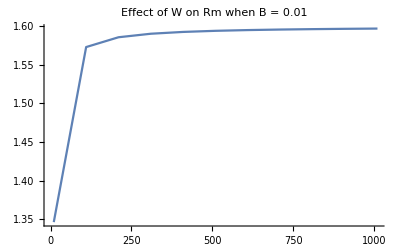
-Graphics-Host massRm

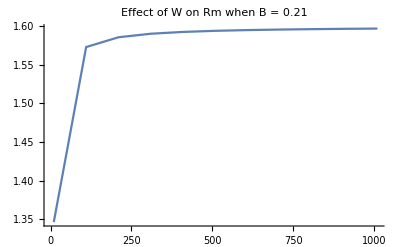
-Graphics-Host massRm

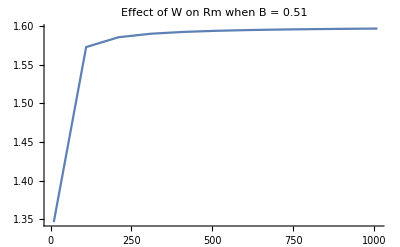
-Graphics-Host massRm

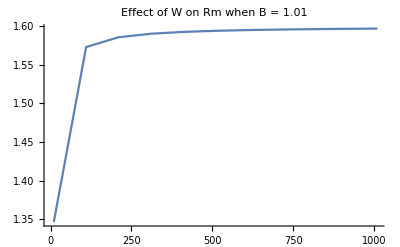
-Graphics-Host massRm

```mathematica
Wvals=Table[W,{W,10,1010,100}];
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[1,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when B = 0.01",PlotRange->All],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[3,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when B = 0.21",PlotRange->All],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[6,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when B = 0.51",PlotRange->All],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[11,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when B = 1.01",PlotRange->All],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
```

Varying W and γ:

```mathematica
RmAcrossWg=Table[Table[Rm/.S1Eq2[[1]]/.I1rEq2[[1]]/.P1rEq2[[2]]/.S2Eq2[[1]]/.I2rEq2[[1]]/.P2rEq2[[2]]/.allom/.allompars/.{β1->0.1,β2->0.1,γ->g,σ2->1,σ1->1,f->0.9,c->0.8,x1->1/2,x2->1/2,W->Wval,T->270},{Wval,10,1010,100}],{g,0.01,1.01,0.1}];
```

Increasing host body size increases invasion fitness, regardless of the value of γ, thereby making it easier for the generalist to invade.

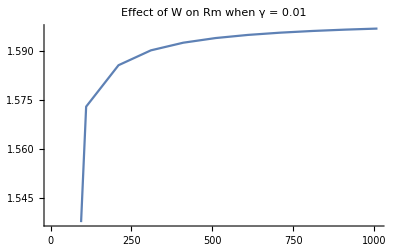
-Graphics-Host massRm

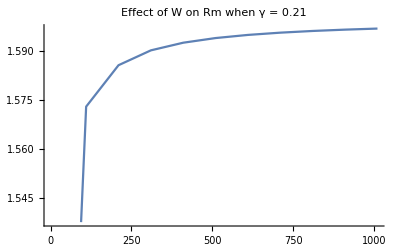
-Graphics-Host massRm

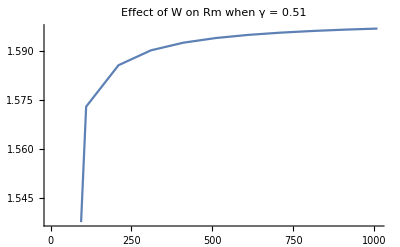
-Graphics-Host massRm

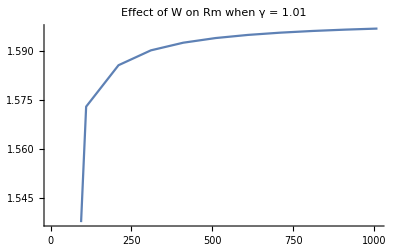
-Graphics-Host massRm

```mathematica
Wvals=Table[W,{W,10,1010,100}];
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[1,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when γ = 0.01"],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[3,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when γ = 0.21"],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[6,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when γ = 0.51"],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[11,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when γ = 1.01"],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
```

The effect of mass and temperature:

```mathematica
RmAcrossWT=Table[Table[Rm/.S1Eq2[[1]]/.I1rEq2[[1]]/.P1rEq2[[2]]/.S2Eq2[[1]]/.I2rEq2[[1]]/.P2rEq2[[2]]/.allom/.allompars/.{β1->0.1,β2->0.1,γ->0.1,σ2->1,σ1->1,f->0.9,c->0.8,x1->1/2,x2->1/2,W->Wval,T->Tval},{Tval,270,310,5}],{Wval,10,1010,100}];
```

Increasing temperature has no effect on the invasion fitness.

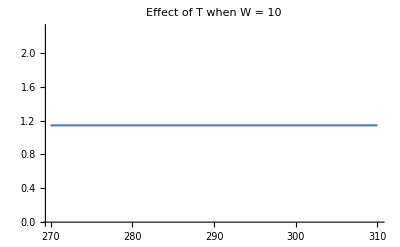
-Graphics-TemperatureRm

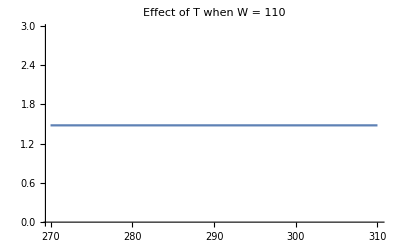
-Graphics-TemperatureRm

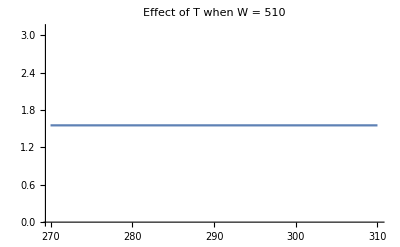
-Graphics-TemperatureRm

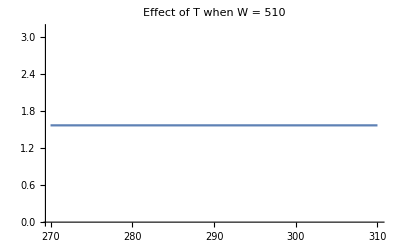
-Graphics-TemperatureRm

```mathematica
Tvals=Table[T,{T,270,310,5}];
Labeled[ListLinePlot[Table[{Tvals[[i]],Round[Re[RmAcrossWT[[1,i]]],0.0001]},{i,1,Length[Tvals]}],PlotLabel->"Effect of T when W = 10"],{"Temperature","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Round[Re[RmAcrossWT[[2,i]]],0.0001]},{i,1,Length[Tvals]}],PlotLabel->"Effect of T when W = 110"],{"Temperature","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Round[Re[RmAcrossWT[[6,i]]],0.0001]},{i,1,Length[Tvals]}],PlotLabel->"Effect of T when W = 510"],{"Temperature","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Round[Re[RmAcrossWT[[11,i]]],0.0001]},{i,1,Length[Tvals]}],PlotLabel->"Effect of T when W = 510"],{"Temperature","Rm"},{Bottom,Left},RotateLabel->True]
```

#### Ectoparasites:

Many of the parameters of the model are set by the allometric relationships (Gillooly et al. 2001, Allen et al. 2002, Savage et al. 2004, Poulin & George-Nascimento 2007), and thus can be set to biologically reasonable values.

```mathematica
allom={K1->K0 Exp[0.78/(k T)] W^(-3/4),K2->K0 Exp[0.78/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-0.43/(k T)] W^(-1/4),μ2->μ0 Exp[-0.43/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-0.43/(k T)] W^(5/12),λ2->λ0 Exp[-0.43/(k T)] (f W)^(5/12),r1->r0 Exp[-0.43/(k T)] W^(-1/4),r2->r0 Exp[-0.43/(k T)] (f W)^(-1/4)};
allompars={k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10};
```

That leaves a much smaller subset of parameters that can be varied. For simplicity, we focus on parameters whose effects on invasion fitness are indeterminate. This excludes parameters related to the costs associated with generalism, including c (the reduction in shedding rate for generalists), σ_1 (the probability of coinfection, which hold constant at 1), and x_1 (the fraction of host resources captured by the resident strains in coinfection). None of these parameters affect the equilibrium abundances of susceptible and singly infected hosts, so their effect on R_m are predictable and obvious - reducing c, reducing σ_1, or increasing x_1 will all reduce R_m, making invasion more difficult. Thus the only parameters to explore (other than host mass W and temperature T), are β (the contact rate between hosts and parasites, which is assumed to be dependent on the parasite and thus equal for both hosts) and γ (the loss rate of parasites from the environment).

Varying W and β:

```mathematica
RmAcrossWB=Table[Table[Rm/.S1Eq2[[1]]/.I1rEq2[[1]]/.P1rEq2[[2]]/.S2Eq2[[1]]/.I2rEq2[[1]]/.P2rEq2[[2]]/.allom/.allompars/.{β1->B,β2->B,γ->0.1,σ2->1,σ1->1,f->0.9,c->0.8,x1->1/2,x2->1/2,W->Wval,T->270},{Wval,10,1010,100}],{B,0.01,1.01,0.1}];
```

Increasing host body size increases invasion fitness, regardless of the value of β, thereby making it easier for the generalist to invade.

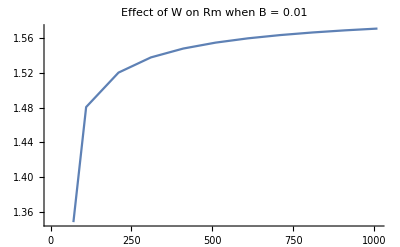
-Graphics-Host massRm

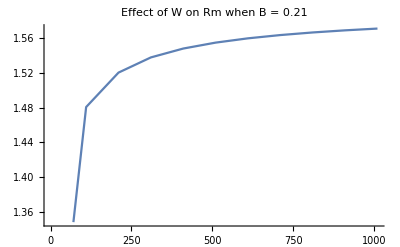
-Graphics-Host massRm

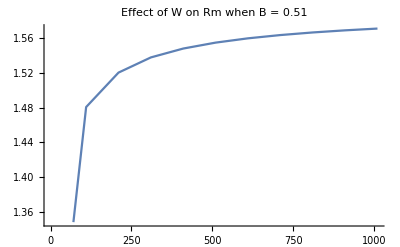
-Graphics-Host massRm

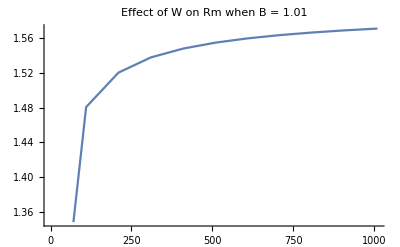
-Graphics-Host massRm

```mathematica
Wvals=Table[W,{W,10,1010,100}];
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[1,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when B = 0.01"],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[3,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when B = 0.21"],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[6,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when B = 0.51"],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[11,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when B = 1.01"],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
```

Varying W and γ:

```mathematica
RmAcrossWg=Table[Table[Rm/.S1Eq2[[1]]/.I1rEq2[[1]]/.P1rEq2[[2]]/.S2Eq2[[1]]/.I2rEq2[[1]]/.P2rEq2[[2]]/.allom/.allompars/.{β1->0.1,β2->0.1,γ->g,σ2->1,σ1->1,f->0.9,c->0.8,x1->1/2,x2->1/2,W->Wval,T->270},{Wval,10,1010,100}],{g,0.01,1.01,0.1}];
```

Increasing host body size increases invasion fitness, regardless of the value of γ, thereby making it easier for the generalist to invade.

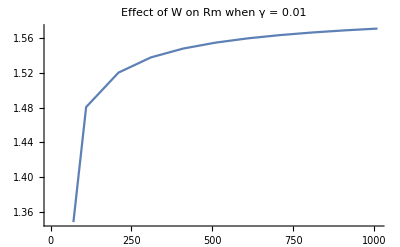
-Graphics-Host massRm

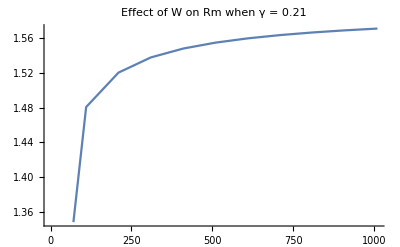
-Graphics-Host massRm

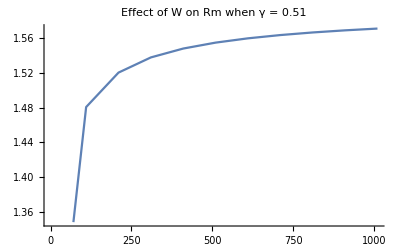
-Graphics-Host massRm

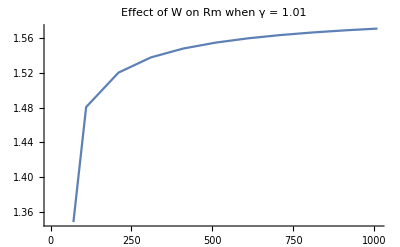
-Graphics-Host massRm

```mathematica
Wvals=Table[W,{W,10,1010,100}];
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[1,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when γ = 0.01"],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[3,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when γ = 0.21"],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[6,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when γ = 0.51"],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[11,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when γ = 1.01"],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
```

The effect of mass and temperature:

```mathematica
RmAcrossWT=Table[Table[Rm/.S1Eq2[[1]]/.I1rEq2[[1]]/.P1rEq2[[2]]/.S2Eq2[[1]]/.I2rEq2[[1]]/.P2rEq2[[2]]/.allom/.allompars/.{β1->0.1,β2->0.1,γ->0.1,σ2->1,σ1->1,f->0.9,c->0.8,x1->1/2,x2->1/2,W->Wval,T->Tval},{Tval,270,310,5}],{Wval,10,1010,100}];
```

Increasing temperature has no effect on the invasion fitness.

```mathematica
Tvals=Table[T,{T,270,310,5}];
Labeled[ListLinePlot[Table[{Tvals[[i]],Round[Re[RmAcrossWT[[1,i]]],0.0001]},{i,1,Length[Tvals]}],PlotLabel->"Effect of T when W = 10"],{"Temperature","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Round[Re[RmAcrossWT[[2,i]]],0.0001]},{i,1,Length[Tvals]}],PlotLabel->"Effect of T when W = 110"],{"Temperature","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Round[Re[RmAcrossWT[[6,i]]],0.0001]},{i,1,Length[Tvals]}],PlotLabel->"Effect of T when W = 510"],{"Temperature","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Round[Re[RmAcrossWT[[11,i]]],0.0001]},{i,1,Length[Tvals]}],PlotLabel->"Effect of T when W = 510"],{"Temperature","Rm"},{Bottom,Left},RotateLabel->True]
```

-Graphics-TemperatureRm

-Graphics-TemperatureRm

-Graphics-TemperatureRm

-Graphics-TemperatureRm

### Case 3: Two specialist parasites, parasites regulate host population sizes; no avoidance of infected hosts

In this model, we assume that the parasite attempts to infect all hosts (because we are assuming that the parasite controls the contact process), but any attempt to infect a doubly infected host result in the removal of the parasite from the environment without any infection.

```mathematica
dS1dt=r1 (S1+I1r+D1rr+I1m+D1rm) (1-(S1+I1r+D1rr+I1m+D1rm)/K1)-β1 S1 (P1r+Pm);
dI1rdt=β1 S1 P1r-σ1 β1 I1r (P1r+Pm)-μ1 I1r;
dD1rrdt=σ1 β1 I1r P1r-μ1 D1rr;
dP1rdt=λ1 (I1r+D1rr+x1 D1rm)-β1 (S1+I1r+D1rr+I1m) P1r-γ P1r;
dS2dt=r2 (S2+I2r+D2rr+I2m+D2rm) (1-(S2+I2r+D2rr+I2m+D2rm)/K2)-β2 S2 (P2r+Pm);
dI2rdt=β2 S2 P2r-σ2 β2 I2r (P2r+Pm)-μ2 I2r;
dD2rrdt=σ2 β2 I2r P2r-μ2 D2rr;
dP2rdt=λ2 (I2r+D2rr+x2 D2rm)- β2 (S2+I2r+D2rr+I2m) P2r-γ P2r;

dI1mdt=β1 S1 Pm-σ1 β1 I1m P1r-μ1 I1m;
dI2mdt=β2 S2 Pm-σ2 β2 I2m P2r-μ2 I2m;
dD1rmdt=σ1 β1 I1r Pm+σ1 β1 I1m P1r-μ1 D1rm;
dD2rmdt=σ2 β2 I2r Pm+σ2 β2 I2m P2r-μ2 D2rm;
dPmdt=c (λ1 I1m+λ2 I2m+(1-x1) λ1 D1rm+(1-x2) λ2 D2rm)-β1 (S1+I1r+D1rr) Pm-β2 (S2+I2r+D2rr) Pm-γ Pm;
```

Whether the mutant can invade will depend on the mutant Jacobian matrix:

```mathematica
MatrixForm[Jmut={{D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,D1rm],D[dI1mdt,D2rm],D[dI1mdt,Pm]},
{D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,D1rm],D[dI2mdt,D2rm],D[dI2mdt,Pm]},{D[dD1rmdt,I1m],D[dD1rmdt,I2m],D[dD1rmdt,D1rm],D[dD1rmdt,D2rm],D[dD1rmdt,Pm]},
{D[dD2rmdt,I1m],D[dD2rmdt,I2m],D[dD2rmdt,D1rm],D[dD2rmdt,D2rm],D[dD2rmdt,Pm]},
{D[dPmdt,I1m],D[dPmdt,I2m],D[dPmdt,D1rm],D[dPmdt,D2rm],D[dPmdt,Pm]}}]
```

(-μ1-P1r β1 σ1 | 0 | 0 | 0 | S1 β1
0 | -μ2-P2r β2 σ2 | 0 | 0 | S2 β2
P1r β1 σ1 | 0 | -μ1 | 0 | I1r β1 σ1
0 | P2r β2 σ2 | 0 | -μ2 | I2r β2 σ2
c λ1 | c λ2 | c (1-x1) λ1 | c (1-x2) λ2 | -(D1rr+I1r+S1) β1-(D2rr+I2r+S2) β2-γ)

Using the next generation theorem, the invasion fitness is equal to the spectral radius of the matrix F.V^-1, where J_mut=F-V.

```mathematica
MatrixForm[V]
```

(μ1+P1 βI1 σC1 | 0 | 0 | 0 | 0
0 | 0 | μ1 | 0 | 0
0 | μ2+P2 βI2 σC2 | 0 | 0 | 0
0 | 0 | 0 | μ2 | 0
-a λ1 | -a λ1 | -a (1-x1) λ1 | -a (1-x2) λ1 | D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ)

{{(μ1 μ2^2+P2r β2 μ1 μ2 σ2)/(μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),0,0,0,0},{0,(μ1^2 μ2+P1r β1 μ1 μ2 σ1)/(μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),0,0,0},{0,0,1/μ1,0,0},{0,0,0,1/μ2,0},{(c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2)/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),(c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1)/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),(c (1-x1) λ1)/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ1),(c (1-x2) λ2)/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ2),1/((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ)}}

{-(D1rr+I1r+S1) β1-(D2rr+I2r+S2) β2-γ,-μ1,-μ2,-μ1-P1r β1 σ1,-μ2-P2r β2 σ2}

```mathematica
MatrixForm[V]
```

(μ1+P1r β1 σ1 | 0 | 0 | 0 | 0
0 | μ2+P2r β2 σ2 | 0 | 0 | 0
0 | 0 | μ1 | 0 | 0
0 | 0 | 0 | μ2 | 0
-c λ1 | -c λ2 | -c (1-x1) λ1 | -c (1-x2) λ2 | (D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ)

```mathematica
F={{0,0,0,0,Jmut[[1,5]]},
{0,0,0,0,Jmut[[2,5]]},
{Jmut[[3,1]],0,0,0,Jmut[[3,5]]},
{0,Jmut[[4,2]],0,0,Jmut[[4,5]]},
{0,0,0,0,0}};
V=F-Jmut;
Inverse[V]//Simplify
Eigenvalues[-V]
```

{{1/(μ1+P1r β1 σ1),0,0,0,0},{0,1/(μ2+P2r β2 σ2),0,0,0},{0,0,1/μ1,0,0},{0,0,0,1/μ2,0},{(c λ1)/((D1rr β1+I1r β1+S1 β1+D2rr β2+I2r β2+S2 β2+γ) (μ1+P1r β1 σ1)),(c λ2)/((D1rr β1+I1r β1+S1 β1+D2rr β2+I2r β2+S2 β2+γ) (μ2+P2r β2 σ2)),(c (1-x1) λ1)/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ1),(c (1-x2) λ2)/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ2),1/((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ)}}

{-(D1rr+I1r+S1) β1-(D2rr+I2r+S2) β2-γ,-μ1,-μ2,-μ1-P1r β1 σ1,-μ2-P2r β2 σ2}

```mathematica
MatrixForm[Dot[F,Inverse[V]]]
Simplify[Eigenvalues[Dot[F,Inverse[V]]]]
```

((S1 β1 (c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2))/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (S1 β1 (c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1))/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c S1 (1-x1) β1 λ1)/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ1) | (c S1 (1-x2) β1 λ2)/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ2) | (S1 β1)/((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ)
(S2 β2 (c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2))/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (S2 β2 (c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1))/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c S2 (1-x1) β2 λ1)/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ1) | (c S2 (1-x2) β2 λ2)/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ2) | (S2 β2)/((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ)
(P1r β1 σ1 (μ1 μ2^2+P2r β2 μ1 μ2 σ2))/(μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))+(I1r β1 σ1 (c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2))/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (I1r β1 σ1 (c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1))/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c I1r (1-x1) β1 λ1 σ1)/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ1) | (c I1r (1-x2) β1 λ2 σ1)/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ2) | (I1r β1 σ1)/((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ)
(I2r β2 σ2 (c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2))/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (P2r β2 (μ1^2 μ2+P1r β1 μ1 μ2 σ1) σ2)/(μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))+(I2r β2 (c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1) σ2)/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c I2r (1-x1) β2 λ1 σ2)/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ1) | (c I2r (1-x2) β2 λ2 σ2)/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ2) | (I2r β2 σ2)/((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ)
0 | 0 | 0 | 0 | 0)

{0,0,0,(c S2 β2 λ2 μ1^2 μ2+c S1 β1 λ1 μ1 μ2^2+c P1r S2 β1 β2 λ2 μ1 μ2 σ1+c I1r β1 λ1 μ1 μ2^2 σ1-c I1r x1 β1 λ1 μ1 μ2^2 σ1+c I1r P1r β1^2 λ1 μ2^2 σ1^2-c I1r P1r x1 β1^2 λ1 μ2^2 σ1^2+c P2r S1 β1 β2 λ1 μ1 μ2 σ2+c I2r β2 λ2 μ1^2 μ2 σ2-c I2r x2 β2 λ2 μ1^2 μ2 σ2+c I1r P2r β1 β2 λ1 μ1 μ2 σ1 σ2-c I1r P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2+c I2r P1r β1 β2 λ2 μ1 μ2 σ1 σ2-c I2r P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2+c I1r P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2-c I1r P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2+c I2r P2r β2^2 λ2 μ1^2 σ2^2-c I2r P2r x2 β2^2 λ2 μ1^2 σ2^2+c I2r P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2-c I2r P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2-√(c (-4 (D1rr β1+I1r β1+S1 β1+D2rr β2+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) (P2r S2 (-1+x2) β2^2 λ2 μ1^2 σ2+P1r β1 σ1 (P2r S2 (-1+x2) β2^2 λ2 μ1 σ2+S1 (-1+x1) β1 λ1 μ2 (μ2+P2r β2 σ2)))+c (S2 β2 λ2 μ1 μ2 (μ1+P1r β1 σ1)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ1 μ2-(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2)))^2)))/(2 (D1rr β1+I1r β1+S1 β1+D2rr β2+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),(c S2 β2 λ2 μ1^2 μ2+c S1 β1 λ1 μ1 μ2^2+c P1r S2 β1 β2 λ2 μ1 μ2 σ1+c I1r β1 λ1 μ1 μ2^2 σ1-c I1r x1 β1 λ1 μ1 μ2^2 σ1+c I1r P1r β1^2 λ1 μ2^2 σ1^2-c I1r P1r x1 β1^2 λ1 μ2^2 σ1^2+c P2r S1 β1 β2 λ1 μ1 μ2 σ2+c I2r β2 λ2 μ1^2 μ2 σ2-c I2r x2 β2 λ2 μ1^2 μ2 σ2+c I1r P2r β1 β2 λ1 μ1 μ2 σ1 σ2-c I1r P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2+c I2r P1r β1 β2 λ2 μ1 μ2 σ1 σ2-c I2r P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2+c I1r P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2-c I1r P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2+c I2r P2r β2^2 λ2 μ1^2 σ2^2-c I2r P2r x2 β2^2 λ2 μ1^2 σ2^2+c I2r P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2-c I2r P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2+√(c (-4 (D1rr β1+I1r β1+S1 β1+D2rr β2+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) (P2r S2 (-1+x2) β2^2 λ2 μ1^2 σ2+P1r β1 σ1 (P2r S2 (-1+x2) β2^2 λ2 μ1 σ2+S1 (-1+x1) β1 λ1 μ2 (μ2+P2r β2 σ2)))+c (S2 β2 λ2 μ1 μ2 (μ1+P1r β1 σ1)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ1 μ2-(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2)))^2)))/(2 (D1rr β1+I1r β1+S1 β1+D2rr β2+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))}

The mutant can invade if the spectral radius is greater than one. The spectral radius can be reexpressed as:

```mathematica
Rm=(σ1 β1 I1r)/(D1rr β1+I1r β1+S1 β1+D2rr β2+I2r β2+S2 β2+γ) (c λ1 (1-x1))/μ1+(β1 S1)/(D1rr β1+I1r β1+S1 β1+D2rr β2+I2r β2+S2 β2+γ) (μ1/(σ1 β1 P1r+μ1) (c λ1)/μ1+(σ1 β1 P1r)/(σ1 β1 P1r+μ1) (c λ1 (1-x1))/μ1)+(σ2 β2 I2r)/(D1rr β1+I1r β1+S1 β1+D2rr β2+I2r β2+S2 β2+γ) (c λ2 (1-x2))/μ2+(β2 S2)/(D1rr β1+I1r β1+S1 β1+D2rr β2+I2r β2+S2 β2+γ) (μ2/(σ2 β2 P2r+μ2) (c λ2)/μ2+(σ2 β2 P2r)/(σ2 β2 P2r+μ2) (c λ2 (1-x2))/μ2);
```

```mathematica
Simplify[Expand[P1r β1 (λ1-2 μ1)+(λ1-μ1) μ1==(P1r β1-λ1+μ1) (μ1+P1r β1)]]
```

P1r^2 β1^2+2 μ1 (-λ1+μ1)==2 P1r β1 (λ1-2 μ1)

The relevant equilibria (for the system without the generalist parasite) are found below.

```mathematica
S1Eq=Solve[(dI1rdt/.{Pm->0})==0,S1]
I1rEq=Solve[(dD1rrdt/.{Pm->0})==0,I1r]
D1rrEq=Solve[(dP1rdt/.{D1rm->0,I1m->0}/.S1Eq[[1]]/.I1rEq[[1]])==0,D1rr]
I1rEq=Simplify[I1rEq/.D1rrEq[[1]]]
S1Eq=Simplify[S1Eq/.I1rEq[[1]]]
P1rEq=Solve[Simplify[dS1dt/.{D1rm->0,I1m->0,Pm->0}/.S1Eq[[1]]/.I1rEq[[1]]/.D1rrEq[[1]]]==0,P1r]

S2Eq=Solve[(dI2rdt/.{Pm->0})==0,S2];
I2rEq=Solve[(dD2rrdt/.{Pm->0})==0,I2r];
D2rrEq=Solve[(dP2rdt/.{D2rm->0,I2m->0}/.S2Eq[[1]]/.I2rEq[[1]])==0,D2rr]
I2rEq=Simplify[I2rEq/.D2rrEq[[1]]]
S2Eq=Simplify[S2Eq/.I2rEq[[1]]]
P2rEq=Solve[Simplify[dS2dt/.{D2rm->0,I2m->0,Pm->0}/.S2Eq[[1]]/.I2rEq[[1]]/.D2rrEq[[1]]]==0,P2r]
```

{{S1→(I1r μ1+I1r P1r β1 σ1)/(P1r β1)}}

{{I1r→(D1rr μ1)/(P1r β1 σ1)}}

{{D1rr→-(P1r^2 β1 γ σ1)/((P1r β1-λ1+μ1) (μ1+P1r β1 σ1))}}

{{I1r→-(P1r γ μ1)/((P1r β1-λ1+μ1) (μ1+P1r β1 σ1))}}

{{S1→-(γ μ1)/(β1 (P1r β1-λ1+μ1))}}

{{P1r→1/(2 (K1 r1 β1^3+r1 β1^2 γ-K1 β1^3 μ1))(K1 r1 β1^2 λ1-2 K1 r1 β1^2 μ1-2 r1 β1 γ μ1-K1 β1^2 λ1 μ1+K1 β1^2 μ1^2-√K1 β1^(3/2) √(K1 r1^2 β1 λ1^2-2 K1 r1 β1 λ1^2 μ1+2 K1 r1 β1 λ1 μ1^2+4 r1 γ λ1 μ1^2+K1 β1 λ1^2 μ1^2-2 K1 β1 λ1 μ1^3+K1 β1 μ1^4))},{P1r→1/(2 (K1 r1 β1^3+r1 β1^2 γ-K1 β1^3 μ1))(K1 r1 β1^2 λ1-2 K1 r1 β1^2 μ1-2 r1 β1 γ μ1-K1 β1^2 λ1 μ1+K1 β1^2 μ1^2+√K1 β1^(3/2) √(K1 r1^2 β1 λ1^2-2 K1 r1 β1 λ1^2 μ1+2 K1 r1 β1 λ1 μ1^2+4 r1 γ λ1 μ1^2+K1 β1 λ1^2 μ1^2-2 K1 β1 λ1 μ1^3+K1 β1 μ1^4))}}

{{D2rr→-(P2r^2 β2 γ σ2)/((P2r β2-λ2+μ2) (μ2+P2r β2 σ2))}}

{{I2r→-(P2r γ μ2)/((P2r β2-λ2+μ2) (μ2+P2r β2 σ2))}}

{{S2→-(γ μ2)/(β2 (P2r β2-λ2+μ2))}}

{{P2r→1/(2 (K2 r2 β2^3+r2 β2^2 γ-K2 β2^3 μ2))(K2 r2 β2^2 λ2-2 K2 r2 β2^2 μ2-2 r2 β2 γ μ2-K2 β2^2 λ2 μ2+K2 β2^2 μ2^2-√K2 β2^(3/2) √(K2 r2^2 β2 λ2^2-2 K2 r2 β2 λ2^2 μ2+2 K2 r2 β2 λ2 μ2^2+4 r2 γ λ2 μ2^2+K2 β2 λ2^2 μ2^2-2 K2 β2 λ2 μ2^3+K2 β2 μ2^4))},{P2r→1/(2 (K2 r2 β2^3+r2 β2^2 γ-K2 β2^3 μ2))(K2 r2 β2^2 λ2-2 K2 r2 β2^2 μ2-2 r2 β2 γ μ2-K2 β2^2 λ2 μ2+K2 β2^2 μ2^2+√K2 β2^(3/2) √(K2 r2^2 β2 λ2^2-2 K2 r2 β2 λ2^2 μ2+2 K2 r2 β2 λ2 μ2^2+4 r2 γ λ2 μ2^2+K2 β2 λ2^2 μ2^2-2 K2 β2 λ2 μ2^3+K2 β2 μ2^4))}}

We can plug those equilibria into the invasion condition, and derive a condition that depends only on the equilibrium abundances of resident parasites in the environment.

```mathematica
RmSimp=FullSimplify[Rm/.I1rEq[[1]]/.S1Eq[[1]]/.D1rrEq[[1]]/.I2rEq[[1]]/.S2Eq[[1]]/.D2rrEq[[1]]/.{σ2->1,σ1->1,x1->1/2,x2->1/2}]
```

(c (P2r β2 λ1+λ2 (P1r β1-2 λ1+μ1)+λ1 μ2))/(-λ1 λ2+(P1r β1+μ1) (P2r β2+μ2))

Note that the mutant can only invade if the numerator is greater than the denominator. Since 0<c<1, then this requires that the following inequality hold:

```mathematica
P2r β2 λ1+λ2 (P1r β1-2 λ1+μ1)+λ1 μ2>-λ1 λ2+(P1r β1+μ1) (P2r β2+μ2)//Simplify
```

(P1r β1-λ1+μ1) (P2r β2-λ2+μ2)<0

However, if you look at the equilibrium expressions for OverHat[S_1] and OverHat[S_2], you see that β_1 OverHat[P_(1r)]-λ_1+μ_1<0 and β_2 OverHat[P_(2r)]-λ_2+μ_2<0. Thus (β_1 OverHat[P_(1r)]-λ_1+μ_1)(β_2 OverHat[P_(2r)]-λ_2+μ_2)>0, meaning that the inequality can never be satisfied; thus, when  there is coinfection and doubly-infected hosts remove parasites from the environment without producing any parasites, the generalist will never be able to invade. This parallels the result seen in the single-infection model.

### Case 4: Two specialist parasites; constant host population size; avoidance of infected hosts

For this model, we assume that

```mathematica
dI1rdt=β1 (1-I1r-D1rr-I1m-D1rm) P1r-σ1 β1 I1r (P1r+Pm)-μ1 I1r;
dD1rrdt=σ1 β1 I1r P1r-μ1 D1rr;
dP1rdt=λ1 K1(I1r+D1rr+x1 D1rm)-β1 (1-D1rr-D1rm) K1 P1r-γ P1r;

dI2rdt=β2 (1-I2r-D2rr-I2m-D2rm) P2r-σ2 β2 I2r (P2r+Pm)-μ2 I2r;
dD2rrdt=σ2 β2 I2r P2r-μ2 D2rr;
dP2rdt=λ2 (I2r+D2rr+x2 D2rm)K2-β2 (1-D2rr-D2rm) K2 P2r-γ P2r;

dI1mdt=β1 (1-I1r-D1rr-I1m-D1rm) Pm-σ1 β1 I1m P1r-μ1 I1m;
dI2mdt=β2 (1-I2r-D2rr-I2m-D2rm) Pm-σ2 β2 I2m P2r-μ2 I2m;
dD1rmdt=σ1 β1 I1r Pm+σ1 β1 I1m P1r-μ1 D1rm;
dD2rmdt=σ2 β2 I2r Pm+σ2 β2 I2m P2r-μ2 D2rm;
dPmdt=c (λ1 I1m K1+λ2 I2m K2+(1-x1) λ1 D1rm K1+(1-x2) λ2 D2rm K2)-β1 (1-D1rr-D1rm) K1 Pm-β2 (1-D2rr-D2rm) K2 Pm-γ Pm;
```

Whether the mutant can invade will depend on the mutant Jacobian matrix:

```mathematica
MatrixForm[Jmut={{D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,D1rm],D[dI1mdt,D2rm],D[dI1mdt,Pm]},
{D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,D1rm],D[dI2mdt,D2rm],D[dI2mdt,Pm]},{D[dD1rmdt,I1m],D[dD1rmdt,I2m],D[dD1rmdt,D1rm],D[dD1rmdt,D2rm],D[dD1rmdt,Pm]},
{D[dD2rmdt,I1m],D[dD2rmdt,I2m],D[dD2rmdt,D1rm],D[dD2rmdt,D2rm],D[dD2rmdt,Pm]},
{D[dPmdt,I1m],D[dPmdt,I2m],D[dPmdt,D1rm],D[dPmdt,D2rm],D[dPmdt,Pm]}}/.{Pm->0,D1rm->0,I1m->0,I2m->0,D2rm->0}]
```

(-μ1-P1r β1 σ1 | 0 | 0 | 0 | (1-D1rr-I1r) β1
0 | -μ2-P2r β2 σ2 | 0 | 0 | (1-D2rr-I2r) β2
P1r β1 σ1 | 0 | -μ1 | 0 | I1r β1 σ1
0 | P2r β2 σ2 | 0 | -μ2 | I2r β2 σ2
c K1 λ1 | c K2 λ2 | c K1 (1-x1) λ1 | c K2 (1-x2) λ2 | -(1-D1rr) K1 β1-(1-D2rr) K2 β2-γ)

Applying the next generation theorem, the mutant can invade if the spectral radius of F.V^-1>1:

```mathematica
F={{0,0,0,0,Jmut[[1,5]]},
{0,0,0,0,Jmut[[2,5]]},
{Jmut[[3,1]],0,0,0,Jmut[[3,5]]},
{0,Jmut[[4,2]],0,0,Jmut[[4,5]]},
{0,0,0,0,0}};
V=F-Jmut;
MatrixForm[Dot[F,Inverse[V]]]
Simplify[Eigenvalues[Dot[F,Inverse[V]]]]
```

(((1-D1rr-I1r) β1 (c K1 λ1 μ1 μ2^2+c K1 P2r β2 λ1 μ1 μ2 σ2))/(((1-D1rr) K1 β1+(1-D2rr) K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | ((1-D1rr-I1r) β1 (c K2 λ2 μ1^2 μ2+c K2 P1r β1 λ2 μ1 μ2 σ1))/(((1-D1rr) K1 β1+(1-D2rr) K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c (1-D1rr-I1r) K1 (1-x1) β1 λ1)/(((1-D1rr) K1 β1+(1-D2rr) K2 β2+γ) μ1) | (c (1-D1rr-I1r) K2 (1-x2) β1 λ2)/(((1-D1rr) K1 β1+(1-D2rr) K2 β2+γ) μ2) | ((1-D1rr-I1r) β1)/((1-D1rr) K1 β1+(1-D2rr) K2 β2+γ)
((1-D2rr-I2r) β2 (c K1 λ1 μ1 μ2^2+c K1 P2r β2 λ1 μ1 μ2 σ2))/(((1-D1rr) K1 β1+(1-D2rr) K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | ((1-D2rr-I2r) β2 (c K2 λ2 μ1^2 μ2+c K2 P1r β1 λ2 μ1 μ2 σ1))/(((1-D1rr) K1 β1+(1-D2rr) K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c (1-D2rr-I2r) K1 (1-x1) β2 λ1)/(((1-D1rr) K1 β1+(1-D2rr) K2 β2+γ) μ1) | (c (1-D2rr-I2r) K2 (1-x2) β2 λ2)/(((1-D1rr) K1 β1+(1-D2rr) K2 β2+γ) μ2) | ((1-D2rr-I2r) β2)/((1-D1rr) K1 β1+(1-D2rr) K2 β2+γ)
(P1r β1 σ1 (μ1 μ2^2+P2r β2 μ1 μ2 σ2))/(μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))+(I1r β1 σ1 (c K1 λ1 μ1 μ2^2+c K1 P2r β2 λ1 μ1 μ2 σ2))/(((1-D1rr) K1 β1+(1-D2rr) K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (I1r β1 σ1 (c K2 λ2 μ1^2 μ2+c K2 P1r β1 λ2 μ1 μ2 σ1))/(((1-D1rr) K1 β1+(1-D2rr) K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c I1r K1 (1-x1) β1 λ1 σ1)/(((1-D1rr) K1 β1+(1-D2rr) K2 β2+γ) μ1) | (c I1r K2 (1-x2) β1 λ2 σ1)/(((1-D1rr) K1 β1+(1-D2rr) K2 β2+γ) μ2) | (I1r β1 σ1)/((1-D1rr) K1 β1+(1-D2rr) K2 β2+γ)
(I2r β2 σ2 (c K1 λ1 μ1 μ2^2+c K1 P2r β2 λ1 μ1 μ2 σ2))/(((1-D1rr) K1 β1+(1-D2rr) K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (P2r β2 (μ1^2 μ2+P1r β1 μ1 μ2 σ1) σ2)/(μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))+(I2r β2 (c K2 λ2 μ1^2 μ2+c K2 P1r β1 λ2 μ1 μ2 σ1) σ2)/(((1-D1rr) K1 β1+(1-D2rr) K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c I2r K1 (1-x1) β2 λ1 σ2)/(((1-D1rr) K1 β1+(1-D2rr) K2 β2+γ) μ1) | (c I2r K2 (1-x2) β2 λ2 σ2)/(((1-D1rr) K1 β1+(1-D2rr) K2 β2+γ) μ2) | (I2r β2 σ2)/((1-D1rr) K1 β1+(1-D2rr) K2 β2+γ)
0 | 0 | 0 | 0 | 0)

{0,0,0,(-c K2 β2 λ2 μ1^2 μ2+c D2rr K2 β2 λ2 μ1^2 μ2+c I2r K2 β2 λ2 μ1^2 μ2-c K1 β1 λ1 μ1 μ2^2+c D1rr K1 β1 λ1 μ1 μ2^2+c I1r K1 β1 λ1 μ1 μ2^2-c K2 P1r β1 β2 λ2 μ1 μ2 σ1+c D2rr K2 P1r β1 β2 λ2 μ1 μ2 σ1+c I2r K2 P1r β1 β2 λ2 μ1 μ2 σ1-c I1r K1 β1 λ1 μ1 μ2^2 σ1+c I1r K1 x1 β1 λ1 μ1 μ2^2 σ1-c I1r K1 P1r β1^2 λ1 μ2^2 σ1^2+c I1r K1 P1r x1 β1^2 λ1 μ2^2 σ1^2-c K1 P2r β1 β2 λ1 μ1 μ2 σ2+c D1rr K1 P2r β1 β2 λ1 μ1 μ2 σ2+c I1r K1 P2r β1 β2 λ1 μ1 μ2 σ2-c I2r K2 β2 λ2 μ1^2 μ2 σ2+c I2r K2 x2 β2 λ2 μ1^2 μ2 σ2-c I1r K1 P2r β1 β2 λ1 μ1 μ2 σ1 σ2+c I1r K1 P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2-c I2r K2 P1r β1 β2 λ2 μ1 μ2 σ1 σ2+c I2r K2 P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2-c I1r K1 P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2+c I1r K1 P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2-c I2r K2 P2r β2^2 λ2 μ1^2 σ2^2+c I2r K2 P2r x2 β2^2 λ2 μ1^2 σ2^2-c I2r K2 P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2+c I2r K2 P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2-√(c (-4 ((-1+D1rr) K1 β1+(-1+D2rr) K2 β2-γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) ((-1+D2rr+I2r) K2 P2r (-1+x2) β2^2 λ2 μ1 (μ1+P1r β1 σ1) σ2+(-1+D1rr+I1r) K1 P1r (-1+x1) β1^2 λ1 μ2 σ1 (μ2+P2r β2 σ2))+c (K1 β1 λ1 μ2 (I1r P1r (-1+x1) β1 σ1^2+μ1 (-1+D1rr+I1r-I1r σ1+I1r x1 σ1)) (μ2+P2r β2 σ2)+K2 β2 λ2 μ1 (μ1+P1r β1 σ1) (I2r P2r (-1+x2) β2 σ2^2+μ2 (-1+D2rr+I2r-I2r σ2+I2r x2 σ2)))^2)))/(2 ((-1+D1rr) K1 β1+(-1+D2rr) K2 β2-γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),(-c K2 β2 λ2 μ1^2 μ2+c D2rr K2 β2 λ2 μ1^2 μ2+c I2r K2 β2 λ2 μ1^2 μ2-c K1 β1 λ1 μ1 μ2^2+c D1rr K1 β1 λ1 μ1 μ2^2+c I1r K1 β1 λ1 μ1 μ2^2-c K2 P1r β1 β2 λ2 μ1 μ2 σ1+c D2rr K2 P1r β1 β2 λ2 μ1 μ2 σ1+c I2r K2 P1r β1 β2 λ2 μ1 μ2 σ1-c I1r K1 β1 λ1 μ1 μ2^2 σ1+c I1r K1 x1 β1 λ1 μ1 μ2^2 σ1-c I1r K1 P1r β1^2 λ1 μ2^2 σ1^2+c I1r K1 P1r x1 β1^2 λ1 μ2^2 σ1^2-c K1 P2r β1 β2 λ1 μ1 μ2 σ2+c D1rr K1 P2r β1 β2 λ1 μ1 μ2 σ2+c I1r K1 P2r β1 β2 λ1 μ1 μ2 σ2-c I2r K2 β2 λ2 μ1^2 μ2 σ2+c I2r K2 x2 β2 λ2 μ1^2 μ2 σ2-c I1r K1 P2r β1 β2 λ1 μ1 μ2 σ1 σ2+c I1r K1 P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2-c I2r K2 P1r β1 β2 λ2 μ1 μ2 σ1 σ2+c I2r K2 P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2-c I1r K1 P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2+c I1r K1 P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2-c I2r K2 P2r β2^2 λ2 μ1^2 σ2^2+c I2r K2 P2r x2 β2^2 λ2 μ1^2 σ2^2-c I2r K2 P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2+c I2r K2 P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2+√(c (-4 ((-1+D1rr) K1 β1+(-1+D2rr) K2 β2-γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) ((-1+D2rr+I2r) K2 P2r (-1+x2) β2^2 λ2 μ1 (μ1+P1r β1 σ1) σ2+(-1+D1rr+I1r) K1 P1r (-1+x1) β1^2 λ1 μ2 σ1 (μ2+P2r β2 σ2))+c (K1 β1 λ1 μ2 (I1r P1r (-1+x1) β1 σ1^2+μ1 (-1+D1rr+I1r-I1r σ1+I1r x1 σ1)) (μ2+P2r β2 σ2)+K2 β2 λ2 μ1 (μ1+P1r β1 σ1) (I2r P2r (-1+x2) β2 σ2^2+μ2 (-1+D2rr+I2r-I2r σ2+I2r x2 σ2)))^2)))/(2 ((-1+D1rr) K1 β1+(-1+D2rr) K2 β2-γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))}

The condition for instability of the generalist-free equilibrium can be rearranged into the following expression:

```mathematica
1/(((1-D1rr) K1 β1+(1-D2rr) K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))(c (K1 β1 λ1 μ2 (P1r (1-x1) β1 σ1 (1-D1rr-I1r+I1r σ1)+μ1 (1-D1rr-I1r+I1r σ1-I1r x1 σ1)) (μ2+P2r β2 σ2)+K2 β2 λ2 μ1 (μ1+P1r β1 σ1) (P2r (1-x2) β2 σ2 (1-D2rr-I2r+I2r σ2)+μ2 (1-D2rr-I2r+I2r σ2-I2r x2 σ2))))>1;
```

The left-hand side of this condition is the invasion fitness; this expression can be expressed in a more biologically meaningful was as:

```mathematica
Rm=(σ1 β1 I1r)/((1-D1rr) K1 β1+(1-D2rr) K2 β2+γ) (c λ1 (1-x1) K1)/μ1+(β1 (1-I1r-D1rr))/((1-D1rr) K1 β1+(1-D2rr) K2 β2+γ) (μ1/(σ1 β1 P1r+μ1) (c λ1 K1)/μ1+(σ1 β1 P1r)/(σ1 β1 P1r+μ1) (c λ1 (1-x1) K1)/μ1)+(σ2 β2 I2r)/((1-D1rr) K1 β1+(1-D2rr) K2 β2+γ) (c λ2 (1-x2) K2)/μ2+(β2 (1-I2r-D2rr))/((1-D1rr) K1 β1+(1-D2rr) K2 β2+γ) (μ2/(σ2 β2 P2r+μ2) (c λ2 K2)/μ2+(σ2 β2 P2r)/(σ2 β2 P2r+μ2) (c λ2 (1-x2) K2)/μ2);
Simplify[Rm==1/(((1-D1rr) K1 β1+(1-D2rr) K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))(c (K1 β1 λ1 μ2 (P1r (1-x1) β1 σ1 (1-D1rr-I1r+I1r σ1)+μ1 (1-D1rr-I1r+I1r σ1-I1r x1 σ1)) (μ2+P2r β2 σ2)+K2 β2 λ2 μ1 (μ1+P1r β1 σ1) (P2r (1-x2) β2 σ2 (1-D2rr-I2r+I2r σ2)+μ2 (1-D2rr-I2r+I2r σ2-I2r x2 σ2))))]
```

True

This R_m expression is not analytically intractable, but we can explore the effects of host and environment parameters on its value numerically. The equilibrium values of I_(1r),D_(1r r), I_(2r), and D_(2r r) can be expressed in terms of the equilibrium abundances of parasites in the environment, P_(1r) and P_(2r):

```mathematica
D1rrEq=Solve[(dI1rdt/.{I1m->0,D1rm->0,Pm->0})==0,D1rr];
I1rEq=Solve[(dD1rrdt/.D1rrEq[[1]])==0,I1r]
D1rrEq=Simplify[D1rrEq/.I1rEq[[1]]]
P1rEq=Solve[(dP1rdt/.{D1rm->0}/.I1rEq[[1]]/.D1rrEq[[1]])==0,P1r];
D2rrEq=Solve[(dI2rdt/.{I2m->0,D2rm->0,Pm->0})==0,D2rr];
I2rEq=Solve[(dD2rrdt/.D2rrEq[[1]])==0,I2r]
D2rrEq=Simplify[D2rrEq/.I2rEq[[1]]]
P2rEq=Solve[(dP2rdt/.{D2rm->0}/.I2rEq[[1]]/.D2rrEq[[1]])==0,P2r];
```

{{I1r→(P1r β1 μ1)/((P1r β1+μ1) (μ1+P1r β1 σ1))}}

{{D1rr→(P1r^2 β1^2 σ1)/((P1r β1+μ1) (μ1+P1r β1 σ1))}}

{{I2r→(P2r β2 μ2)/((P2r β2+μ2) (μ2+P2r β2 σ2))}}

{{D2rr→(P2r^2 β2^2 σ2)/((P2r β2+μ2) (μ2+P2r β2 σ2))}}

#### Endoparasites:

Many of the parameters of the model are set by the allometric relationships (Gillooly et al. 2001, Allen et al. 2002, Savage et al. 2004, Poulin & George-Nascimento 2007), and thus can be set to biologically reasonable values.

```mathematica
allom={K1->K0 Exp[0.78/(k T)] W^(-3/4),K2->K0 Exp[0.78/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-0.43/(k T)] W^(-1/4),μ2->μ0 Exp[-0.43/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-0.43/(k T)] W^(3/4),λ2->λ0 Exp[-0.43/(k T)] (f W)^(3/4),r1->r0 Exp[-0.43/(k T)] W^(-1/4),r2->r0 Exp[-0.43/(k T)] (f W)^(-1/4)};
allompars={k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10};
```

That leaves a much smaller subset of parameters that can be varied. For simplicity, we focus on parameters whose effects on invasion fitness are indeterminate. This excludes parameters related to the costs associated with generalism, including c (the reduction in shedding rate for generalists), σ_1 (the probability of coinfection, which hold constant at 1), and x_1 (the fraction of host resources captured by the resident strains in coinfection). None of these parameters affect the equilibrium abundances of susceptible and singly infected hosts, so their effect on R_m are predictable and obvious - reducing c, reducing σ_1, or increasing x_1 will all reduce R_m, making invasion more difficult. Thus the only parameters to explore (other than host mass W and temperature T), are β (the contact rate between hosts and parasites, which is assumed to be dependent on the parasite and thus equal for both hosts) and γ (the loss rate of parasites from the environment).

Varying W and β:

```mathematica
RmSimp=Rm/.I1rEq[[1]]/.I2rEq[[1]]/.D1rrEq[[1]]/.D2rrEq[[1]]/.P1rEq[[2]]/.P2rEq[[2]]/.allom/.allompars;
```

```mathematica
RmAcrossWB=Table[Table[RmSimp/.{β1->B,β2->B,γ->1000,σ2->1,W->Wval,T->270,σ1->1,f->0.9,c->0.8,x1->1/2,x2->1/2},{Wval,10,1010,100}],{B,0.004,0.1,0.008}];
```

Increasing host body size increases invasion fitness, regardless of the value of β, thereby making it easier for the generalist to invade.

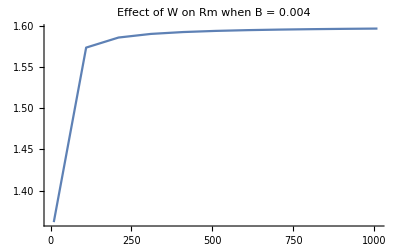
-Graphics-Host massRm

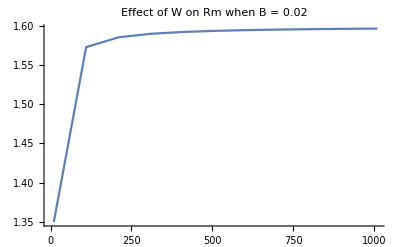
-Graphics-Host massRm

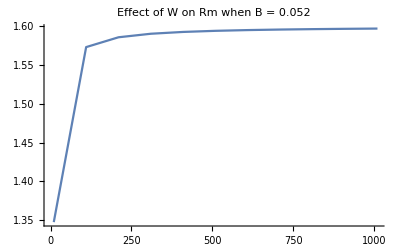
-Graphics-Host massRm

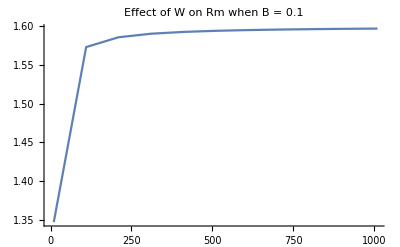
-Graphics-Host massRm

```mathematica
Wvals=Table[W,{W,10,1010,100}];
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[1,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when B = 0.004",PlotRange->All],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[3,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when B = 0.02",PlotRange->All],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[7,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when B = 0.052",PlotRange->All],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[13,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when B = 0.1",PlotRange->All],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
```

Varying W and γ:

```mathematica
RmAcrossWg=Table[Table[RmSimp/.{β1->0.01,β2->0.01,γ->g,σ2->1,W->Wval,T->270,σ1->1,f->0.9,c->0.8,x1->1/2,x2->1/2},{Wval,10,1010,100}],{g,1,1001,100}];
```

Increasing host body size increases invasion fitness, regardless of the value of γ, thereby making it easier for the generalist to invade.

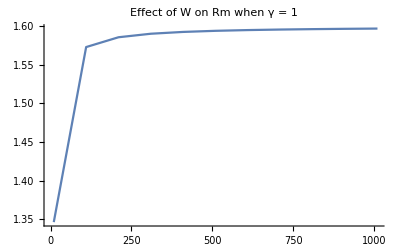
-Graphics-Host massRm

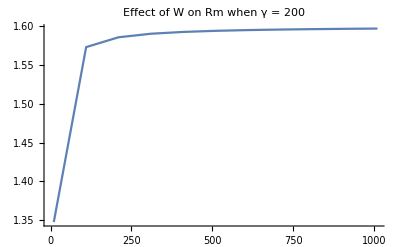
-Graphics-Host massRm

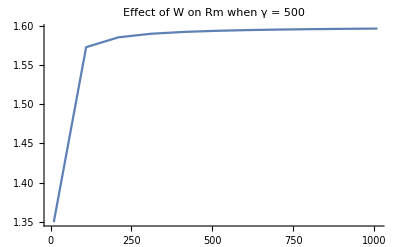
-Graphics-Host massRm

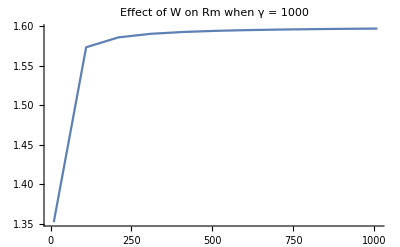
-Graphics-Host massRm

```mathematica
Wvals=Table[W,{W,10,1010,100}];
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[1,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when γ = 1",PlotRange->All],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[3,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when γ = 200",PlotRange->All],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[6,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when γ = 500",PlotRange->All],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[11,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when γ = 1000",PlotRange->All],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
```

The effect of mass and temperature:

```mathematica
Rm
```

(c I1r K1 (1-x1) β1 λ1 σ1)/(((1-D1rr) K1 β1+(1-D2rr) K2 β2+γ) μ1)+((1-D1rr-I1r) β1 ((c K1 λ1)/(μ1+P1r β1 σ1)+(c K1 P1r (1-x1) β1 λ1 σ1)/(μ1 (μ1+P1r β1 σ1))))/((1-D1rr) K1 β1+(1-D2rr) K2 β2+γ)+(c I2r K2 (1-x2) β2 λ2 σ2)/(((1-D1rr) K1 β1+(1-D2rr) K2 β2+γ) μ2)+((1-D2rr-I2r) β2 ((c K2 λ2)/(μ2+P2r β2 σ2)+(c K2 P2r (1-x2) β2 λ2 σ2)/(μ2 (μ2+P2r β2 σ2))))/((1-D1rr) K1 β1+(1-D2rr) K2 β2+γ)

```mathematica
RmAcrossWT=Table[Table[RmSimp/.{β1->0.01,β2->0.01,γ->100,σ2->1,W->Wval,T->Tval,σ1->1,f->0.9,c->0.8,x1->1/2,x2->1/2},{Tval,270,310,2}],{Wval,10,1010,100}];
```

Increasing temperature has a very small positive effect on the invasion fitness - the magnitude of this effect depends on body size - as body size of the host gets larger, the invasion fitness becomes less sensitive to changes in temperature.

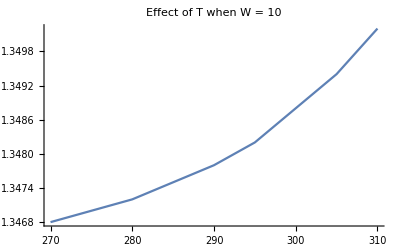
-Graphics-TemperatureRm

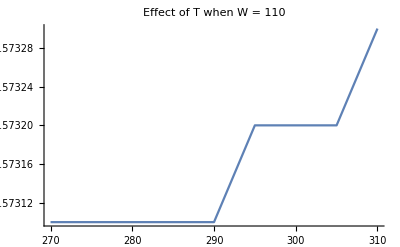
-Graphics-TemperatureRm

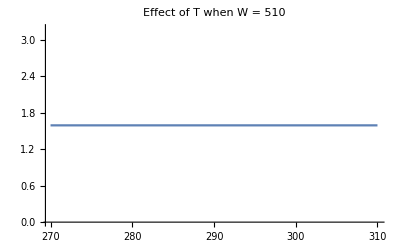
-Graphics-TemperatureRm

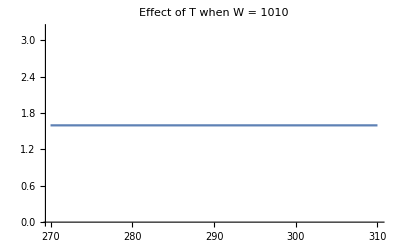
-Graphics-TemperatureRm

```mathematica
Tvals=Table[T,{T,270,310,5}];
Labeled[ListLinePlot[Table[{Tvals[[i]],Round[Re[RmAcrossWT[[1,i]]],0.0001]},{i,1,Length[Tvals]}],PlotLabel->"Effect of T when W = 10"],{"Temperature","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Round[Re[RmAcrossWT[[2,i]]],0.0001]},{i,1,Length[Tvals]}],PlotLabel->"Effect of T when W = 110"],{"Temperature","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Round[Re[RmAcrossWT[[6,i]]],0.0001]},{i,1,Length[Tvals]}],PlotLabel->"Effect of T when W = 510"],{"Temperature","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Round[Re[RmAcrossWT[[11,i]]],0.0001]},{i,1,Length[Tvals]}],PlotLabel->"Effect of T when W = 1010"],{"Temperature","Rm"},{Bottom,Left},RotateLabel->True]
```

#### Ectoparasites:

Many of the parameters of the model are set by the allometric relationships (Gillooly et al. 2001, Allen et al. 2002, Savage et al. 2004, Poulin & George-Nascimento 2007), and thus can be set to biologically reasonable values.

```mathematica
allom={K1->K0 Exp[0.78/(k T)] W^(-3/4),K2->K0 Exp[0.78/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-0.43/(k T)] W^(-1/4),μ2->μ0 Exp[-0.43/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-0.43/(k T)] W^(5/12),λ2->λ0 Exp[-0.43/(k T)] (f W)^(5/12),r1->r0 Exp[-0.43/(k T)] W^(-1/4),r2->r0 Exp[-0.43/(k T)] (f W)^(-1/4)};
allompars={k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10};
```

That leaves a much smaller subset of parameters that can be varied. For simplicity, we focus on parameters whose effects on invasion fitness are indeterminate. This excludes parameters related to the costs associated with generalism, including c (the reduction in shedding rate for generalists), σ_1 (the probability of coinfection, which hold constant at 1), and x_1 (the fraction of host resources captured by the resident strains in coinfection). None of these parameters affect the equilibrium abundances of susceptible and singly infected hosts, so their effect on R_m are predictable and obvious - reducing c, reducing σ_1, or increasing x_1 will all reduce R_m, making invasion more difficult. Thus the only parameters to explore (other than host mass W and temperature T), are β (the contact rate between hosts and parasites, which is assumed to be dependent on the parasite and thus equal for both hosts) and γ (the loss rate of parasites from the environment).

Varying W and β:

```mathematica
RmSimp=Rm/.I1rEq[[1]]/.I2rEq[[1]]/.D1rrEq[[1]]/.D2rrEq[[1]]/.P1rEq[[2]]/.P2rEq[[2]]/.allom/.allompars;
```

```mathematica
RmAcrossWB=Table[Table[RmSimp/.{β1->B,β2->B,γ->1000,σ2->1,W->Wval,T->270,σ1->1,f->0.9,c->0.8,x1->1/2,x2->1/2},{Wval,10,1010,100}],{B,0.004,0.1,0.008}];
```

Increasing host body size increases invasion fitness, regardless of the value of β, thereby making it easier for the generalist to invade.

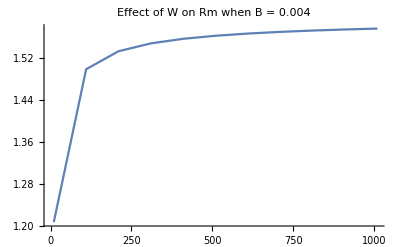
-Graphics-Host massRm

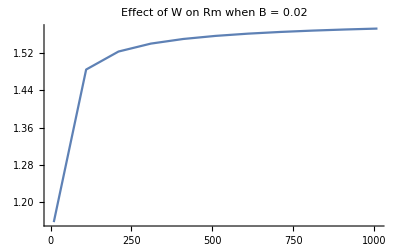
-Graphics-Host massRm

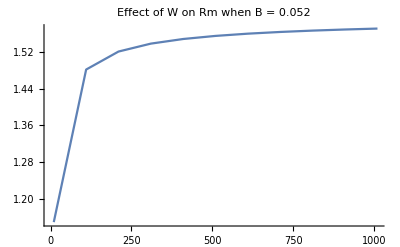
-Graphics-Host massRm

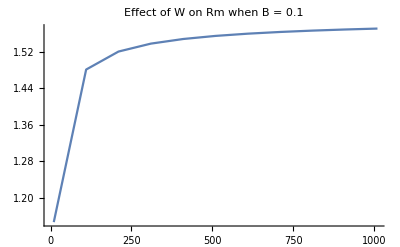
-Graphics-Host massRm

```mathematica
Wvals=Table[W,{W,10,1010,100}];
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[1,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when B = 0.004",PlotRange->All],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[3,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when B = 0.02",PlotRange->All],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[7,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when B = 0.052",PlotRange->All],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[13,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when B = 0.1",PlotRange->All],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
```

Varying W and γ:

```mathematica
RmAcrossWg=Table[Table[RmSimp/.{β1->0.01,β2->0.01,γ->g,σ2->1,W->Wval,T->270,σ1->1,f->0.9,c->0.8,x1->1/2,x2->1/2},{Wval,10,1010,100}],{g,1,1001,100}];
```

Increasing host body size increases invasion fitness, regardless of the value of γ, thereby making it easier for the generalist to invade.

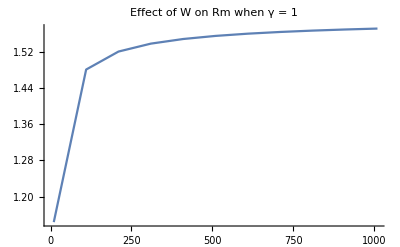
-Graphics-Host massRm

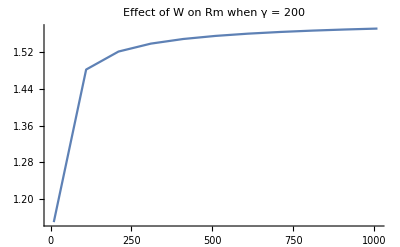
-Graphics-Host massRm

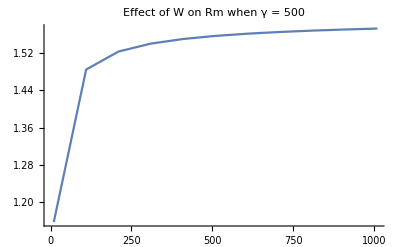
-Graphics-Host massRm

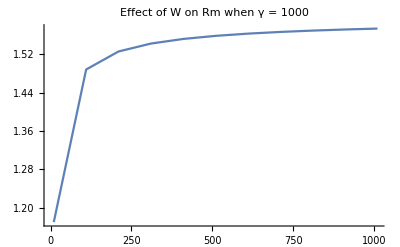
-Graphics-Host massRm

```mathematica
Wvals=Table[W,{W,10,1010,100}];
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[1,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when γ = 1",PlotRange->All],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[3,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when γ = 200",PlotRange->All],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[6,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when γ = 500",PlotRange->All],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[11,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Effect of W on Rm when γ = 1000",PlotRange->All],{"Host mass","Rm"},{Bottom,Left},RotateLabel->True]
```

The effect of mass and temperature:

```mathematica
RmAcrossWT=Table[Table[RmSimp/.{β1->0.01,β2->0.01,γ->100,σ2->1,W->Wval,T->Tval,σ1->1,f->0.9,c->0.8,x1->1/2,x2->1/2},{Tval,270,310,2}],{Wval,10,1010,100}];
```

Increasing temperature has a very small positive effect on the invasion fitness.

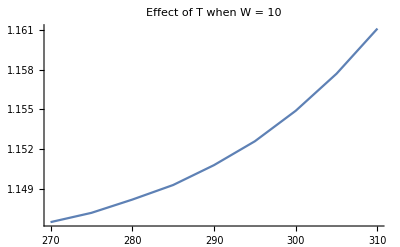
-Graphics-TemperatureRm

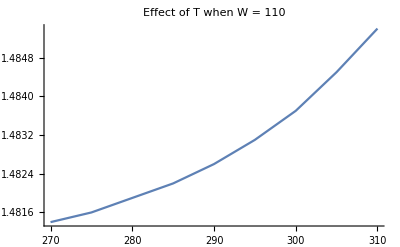
-Graphics-TemperatureRm

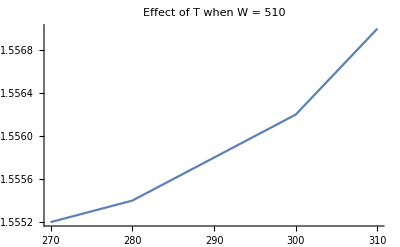
-Graphics-TemperatureRm

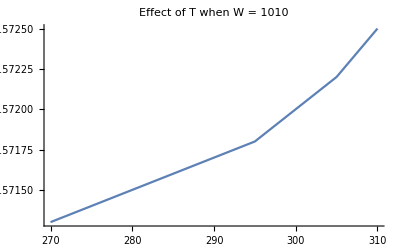
-Graphics-TemperatureRm

```mathematica
Tvals=Table[T,{T,270,310,5}];
Labeled[ListLinePlot[Table[{Tvals[[i]],Round[Re[RmAcrossWT[[1,i]]],0.0001]},{i,1,Length[Tvals]}],PlotLabel->"Effect of T when W = 10"],{"Temperature","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Round[Re[RmAcrossWT[[2,i]]],0.0001]},{i,1,Length[Tvals]}],PlotLabel->"Effect of T when W = 110"],{"Temperature","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Round[Re[RmAcrossWT[[6,i]]],0.0001]},{i,1,Length[Tvals]}],PlotLabel->"Effect of T when W = 510"],{"Temperature","Rm"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Round[Re[RmAcrossWT[[11,i]]],0.0001]},{i,1,Length[Tvals]}],PlotLabel->"Effect of T when W = 1010"],{"Temperature","Rm"},{Bottom,Left},RotateLabel->True]
```

### Case 5: Two specialist parasites; constant host population size; no avoidance of infected hosts

For this model, we assume that

```mathematica
dI1rdt=β1 (1-I1r-D1rr-I1m-D1rm) P1r-σ1 β1 I1r (P1r+Pm)-μ1 I1r;
dD1rrdt=σ1 β1 I1r P1r-μ1 D1rr;
dP1rdt=λ1 K1(I1r+D1rr+x1 D1rm)-β1 K1 P1r-γ P1r;

dI2rdt=β2 (1-I2r-D2rr-I2m-D2rm) P2r-σ2 β2 I2r (P2r+Pm)-μ2 I2r;
dD2rrdt=σ2 β2 I2r P2r-μ2 D2rr;
dP2rdt=λ2 (I2r+D2rr+x2 D2rm)K2-β2 K2 P2r-γ P2r;

dI1mdt=β1 (1-I1r-D1rr-I1m-D1rm) Pm-σ1 β1 I1m P1r-μ1 I1m;
dI2mdt=β2 (1-I2r-D2rr-I2m-D2rm) Pm-σ2 β2 I2m P2r-μ2 I2m;
dD1rmdt=σ1 β1 I1r Pm+σ1 β1 I1m P1r-μ1 D1rm;
dD2rmdt=σ2 β2 I2r Pm+σ2 β2 I2m P2r-μ2 D2rm;
dPmdt=c (λ1 I1m K1+λ2 I2m K2+(1-x1) λ1 D1rm K1+(1-x2) λ2 D2rm K2)-β1 K1 Pm-β2 K2 Pm-γ Pm;
```

Whether the mutant can invade will depend on the mutant Jacobian matrix:

```mathematica
MatrixForm[Jmut={{D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,D1rm],D[dI1mdt,D2rm],D[dI1mdt,Pm]},
{D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,D1rm],D[dI2mdt,D2rm],D[dI2mdt,Pm]},{D[dD1rmdt,I1m],D[dD1rmdt,I2m],D[dD1rmdt,D1rm],D[dD1rmdt,D2rm],D[dD1rmdt,Pm]},
{D[dD2rmdt,I1m],D[dD2rmdt,I2m],D[dD2rmdt,D1rm],D[dD2rmdt,D2rm],D[dD2rmdt,Pm]},
{D[dPmdt,I1m],D[dPmdt,I2m],D[dPmdt,D1rm],D[dPmdt,D2rm],D[dPmdt,Pm]}}/.{Pm->0,D1rm->0,I1m->0,I2m->0,D2rm->0}]
```

(-μ1-P1r β1 σ1 | 0 | 0 | 0 | (1-D1rr-I1r) β1
0 | -μ2-P2r β2 σ2 | 0 | 0 | (1-D2rr-I2r) β2
P1r β1 σ1 | 0 | -μ1 | 0 | I1r β1 σ1
0 | P2r β2 σ2 | 0 | -μ2 | I2r β2 σ2
c K1 λ1 | c K2 λ2 | c K1 (1-x1) λ1 | c K2 (1-x2) λ2 | -K1 β1-K2 β2-γ)

Applying the next generation theorem, the mutant can invade if the spectral radius of F.V^-1>1:

```mathematica
F={{0,0,0,0,Jmut[[1,5]]},
{0,0,0,0,Jmut[[2,5]]},
{Jmut[[3,1]],0,0,0,Jmut[[3,5]]},
{0,Jmut[[4,2]],0,0,Jmut[[4,5]]},
{0,0,0,0,0}};
V=F-Jmut;
MatrixForm[Dot[F,Inverse[V]]]
Simplify[Eigenvalues[Dot[F,Inverse[V]]]]
```

(((1-D1rr-I1r) β1 (c K1 λ1 μ1 μ2^2+c K1 P2r β2 λ1 μ1 μ2 σ2))/((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | ((1-D1rr-I1r) β1 (c K2 λ2 μ1^2 μ2+c K2 P1r β1 λ2 μ1 μ2 σ1))/((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c (1-D1rr-I1r) K1 (1-x1) β1 λ1)/((K1 β1+K2 β2+γ) μ1) | (c (1-D1rr-I1r) K2 (1-x2) β1 λ2)/((K1 β1+K2 β2+γ) μ2) | ((1-D1rr-I1r) β1)/(K1 β1+K2 β2+γ)
((1-D2rr-I2r) β2 (c K1 λ1 μ1 μ2^2+c K1 P2r β2 λ1 μ1 μ2 σ2))/((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | ((1-D2rr-I2r) β2 (c K2 λ2 μ1^2 μ2+c K2 P1r β1 λ2 μ1 μ2 σ1))/((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c (1-D2rr-I2r) K1 (1-x1) β2 λ1)/((K1 β1+K2 β2+γ) μ1) | (c (1-D2rr-I2r) K2 (1-x2) β2 λ2)/((K1 β1+K2 β2+γ) μ2) | ((1-D2rr-I2r) β2)/(K1 β1+K2 β2+γ)
(P1r β1 σ1 (μ1 μ2^2+P2r β2 μ1 μ2 σ2))/(μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))+(I1r β1 σ1 (c K1 λ1 μ1 μ2^2+c K1 P2r β2 λ1 μ1 μ2 σ2))/((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (I1r β1 σ1 (c K2 λ2 μ1^2 μ2+c K2 P1r β1 λ2 μ1 μ2 σ1))/((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c I1r K1 (1-x1) β1 λ1 σ1)/((K1 β1+K2 β2+γ) μ1) | (c I1r K2 (1-x2) β1 λ2 σ1)/((K1 β1+K2 β2+γ) μ2) | (I1r β1 σ1)/(K1 β1+K2 β2+γ)
(I2r β2 σ2 (c K1 λ1 μ1 μ2^2+c K1 P2r β2 λ1 μ1 μ2 σ2))/((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (P2r β2 (μ1^2 μ2+P1r β1 μ1 μ2 σ1) σ2)/(μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))+(I2r β2 (c K2 λ2 μ1^2 μ2+c K2 P1r β1 λ2 μ1 μ2 σ1) σ2)/((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c I2r K1 (1-x1) β2 λ1 σ2)/((K1 β1+K2 β2+γ) μ1) | (c I2r K2 (1-x2) β2 λ2 σ2)/((K1 β1+K2 β2+γ) μ2) | (I2r β2 σ2)/(K1 β1+K2 β2+γ)
0 | 0 | 0 | 0 | 0)

{0,0,0,-((-c K2 β2 λ2 μ1^2 μ2+c D2rr K2 β2 λ2 μ1^2 μ2+c I2r K2 β2 λ2 μ1^2 μ2-c K1 β1 λ1 μ1 μ2^2+c D1rr K1 β1 λ1 μ1 μ2^2+c I1r K1 β1 λ1 μ1 μ2^2-c K2 P1r β1 β2 λ2 μ1 μ2 σ1+c D2rr K2 P1r β1 β2 λ2 μ1 μ2 σ1+c I2r K2 P1r β1 β2 λ2 μ1 μ2 σ1-c I1r K1 β1 λ1 μ1 μ2^2 σ1+c I1r K1 x1 β1 λ1 μ1 μ2^2 σ1-c I1r K1 P1r β1^2 λ1 μ2^2 σ1^2+c I1r K1 P1r x1 β1^2 λ1 μ2^2 σ1^2-c K1 P2r β1 β2 λ1 μ1 μ2 σ2+c D1rr K1 P2r β1 β2 λ1 μ1 μ2 σ2+c I1r K1 P2r β1 β2 λ1 μ1 μ2 σ2-c I2r K2 β2 λ2 μ1^2 μ2 σ2+c I2r K2 x2 β2 λ2 μ1^2 μ2 σ2-c I1r K1 P2r β1 β2 λ1 μ1 μ2 σ1 σ2+c I1r K1 P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2-c I2r K2 P1r β1 β2 λ2 μ1 μ2 σ1 σ2+c I2r K2 P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2-c I1r K1 P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2+c I1r K1 P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2-c I2r K2 P2r β2^2 λ2 μ1^2 σ2^2+c I2r K2 P2r x2 β2^2 λ2 μ1^2 σ2^2-c I2r K2 P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2+c I2r K2 P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2+√(c (4 (K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) ((-1+D2rr+I2r) K2 P2r (-1+x2) β2^2 λ2 μ1 (μ1+P1r β1 σ1) σ2+(-1+D1rr+I1r) K1 P1r (-1+x1) β1^2 λ1 μ2 σ1 (μ2+P2r β2 σ2))+c (K1 β1 λ1 μ2 (I1r P1r (-1+x1) β1 σ1^2+μ1 (-1+D1rr+I1r-I1r σ1+I1r x1 σ1)) (μ2+P2r β2 σ2)+K2 β2 λ2 μ1 (μ1+P1r β1 σ1) (I2r P2r (-1+x2) β2 σ2^2+μ2 (-1+D2rr+I2r-I2r σ2+I2r x2 σ2)))^2)))/(2 (K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))),-((-c K2 β2 λ2 μ1^2 μ2+c D2rr K2 β2 λ2 μ1^2 μ2+c I2r K2 β2 λ2 μ1^2 μ2-c K1 β1 λ1 μ1 μ2^2+c D1rr K1 β1 λ1 μ1 μ2^2+c I1r K1 β1 λ1 μ1 μ2^2-c K2 P1r β1 β2 λ2 μ1 μ2 σ1+c D2rr K2 P1r β1 β2 λ2 μ1 μ2 σ1+c I2r K2 P1r β1 β2 λ2 μ1 μ2 σ1-c I1r K1 β1 λ1 μ1 μ2^2 σ1+c I1r K1 x1 β1 λ1 μ1 μ2^2 σ1-c I1r K1 P1r β1^2 λ1 μ2^2 σ1^2+c I1r K1 P1r x1 β1^2 λ1 μ2^2 σ1^2-c K1 P2r β1 β2 λ1 μ1 μ2 σ2+c D1rr K1 P2r β1 β2 λ1 μ1 μ2 σ2+c I1r K1 P2r β1 β2 λ1 μ1 μ2 σ2-c I2r K2 β2 λ2 μ1^2 μ2 σ2+c I2r K2 x2 β2 λ2 μ1^2 μ2 σ2-c I1r K1 P2r β1 β2 λ1 μ1 μ2 σ1 σ2+c I1r K1 P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2-c I2r K2 P1r β1 β2 λ2 μ1 μ2 σ1 σ2+c I2r K2 P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2-c I1r K1 P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2+c I1r K1 P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2-c I2r K2 P2r β2^2 λ2 μ1^2 σ2^2+c I2r K2 P2r x2 β2^2 λ2 μ1^2 σ2^2-c I2r K2 P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2+c I2r K2 P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2-√(c (4 (K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) ((-1+D2rr+I2r) K2 P2r (-1+x2) β2^2 λ2 μ1 (μ1+P1r β1 σ1) σ2+(-1+D1rr+I1r) K1 P1r (-1+x1) β1^2 λ1 μ2 σ1 (μ2+P2r β2 σ2))+c (K1 β1 λ1 μ2 (I1r P1r (-1+x1) β1 σ1^2+μ1 (-1+D1rr+I1r-I1r σ1+I1r x1 σ1)) (μ2+P2r β2 σ2)+K2 β2 λ2 μ1 (μ1+P1r β1 σ1) (I2r P2r (-1+x2) β2 σ2^2+μ2 (-1+D2rr+I2r-I2r σ2+I2r x2 σ2)))^2)))/(2 (K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)))}

The invasion fitness can be simplified to the following expression:

```mathematica
Rm=(σ1 β1 I1r)/(β1 K1+β2 K2+γ) (c λ1 (1-x1) K1)/μ1+(β1 (1-I1r-D1rr))/(β1 K1+β2 K2+γ) (μ1/(σ1 β1 P1r+μ1) (c λ1 K1)/μ1+(σ1 β1 P1r)/(σ1 β1 P1r+μ1) (c λ1 (1-x1) K1)/μ1)+(σ2 β2 I2r)/(β1 K1+β2 K2+γ) (c λ2 (1-x2) K2)/μ2+(β2 (1-I2r-D2rr))/(β1 K1+β2 K2+γ) (μ2/(σ2 β2 P2r+μ2) (c λ2 K2)/μ2+(σ2 β2 P2r)/(σ2 β2 P2r+μ2) (c λ2 (1-x2) K2)/μ2);
```

The equilibria of the system are given below:

```mathematica
Eq1=Solve[({dI1rdt==0,dD1rrdt==0,dP1rdt==0}/.{Pm->0,D1rm->0,I1m->0}),{I1r,D1rr,P1r}]//Simplify
Eq2=Solve[({dI2rdt==0,dD2rrdt==0,dP2rdt==0}/.{Pm->0,D2rm->0,I2m->0}),{I2r,D2rr,P2r}]//Simplify
```

{{I1r→0,D1rr→0,P1r→0},{I1r→-((K1 β1+γ) μ1 (γ μ1+K1 β1 (-λ1+μ1)))/(K1 β1 λ1 (-γ μ1 (-1+σ1)+K1 β1 (μ1+λ1 σ1-μ1 σ1))),D1rr→((K1 β1 (λ1-μ1)-γ μ1)^2 σ1)/(K1 β1 λ1 (-γ μ1 (-1+σ1)+K1 β1 (μ1+λ1 σ1-μ1 σ1))),P1r→(K1 β1 (λ1-μ1)-γ μ1)/(β1 (K1 β1+γ))}}

{{I2r→0,D2rr→0,P2r→0},{I2r→-((K2 β2+γ) μ2 (γ μ2+K2 β2 (-λ2+μ2)))/(K2 β2 λ2 (-γ μ2 (-1+σ2)+K2 β2 (μ2+λ2 σ2-μ2 σ2))),D2rr→((K2 β2 (λ2-μ2)-γ μ2)^2 σ2)/(K2 β2 λ2 (-γ μ2 (-1+σ2)+K2 β2 (μ2+λ2 σ2-μ2 σ2))),P2r→(K2 β2 (λ2-μ2)-γ μ2)/(β2 (K2 β2+γ))}}

If we allow coinfection (σ_1=σ_2=1) and assume that coinfecting strains equally partition host resources (x_1=x_2=1/2), we can simplify the R_m expression considerably, to c (1+γ/(β_1 K_1+β_2 K_2+γ)):

```mathematica
Simplify[Rm/.Eq1[[2]]/.Eq2[[2]]/.{σ1->1,σ2->1,x1->1/2,x2->1/2}]==c(1+γ/(K1 β1+K2 β2+γ))//Simplify
```

True

#### Endoparasites & Ectoparasites:

For endoparasites and ectoparasites, the effect of body mass and temperature are identical, because whether the generalist can invade does not depend on shedding from infected hosts. Increasing body mass will increase R_m because it decreases the abundance of each host, thereby making it more likely that a parasite “washes out” of the environment without infecting either host. Thereby, generalism benefits the parasite because it increases the total number of hosts available to it. Increasing temperature has a similar affect.

```mathematica
D[c(1+γ/(K1 β1+K2 β2+γ))/.{K1->K1[W],K2->K2[W]},W]/.{K1'[W]->(-3 K1[W])/(4 W),K2'[W]->(-3 K2[W])/(4 W)}//Simplify
D[c(1+γ/(K1 β1+K2 β2+γ))/.{K1->K1[T],K2->K2[T]},T]/.{K1'[T]->-(K1[T] Ε)/(k T^2),K2'[T]->-(K2[T] Ε)/(k T^2)}//Simplify
```

(3 c γ (β1 K1[W]+β2 K2[W]))/(4 W (γ+β1 K1[W]+β2 K2[W])^2)

(c γ Ε (β1 K1[T]+β2 K2[T]))/(k T^2 (γ+β1 K1[T]+β2 K2[T])^2)

## Trophically transmitted parasites

### Case 1: Trophic transmission; one specialist parasite; parasites regulate definitive host population sizes; avoidance of infected intermediate hosts

Let D_1 and D_2 be two definitive hosts and N be prey of both and the intermediate host. One touchy bit is how to deal with the effect of ingestion on both the dynamics of predator (the definitive host) and prey (the intermediate host). One possibility is that infection is embedded within a classic predator-prey model, where both predator and prey growth are impacted by one another. Such a model is quite different from the direct life cycle model studied in the main text, and is also very difficult to analyze. A second possibility is that prey density is constant; in this model you cannot assume that predator growth is entirely determined by prey ingestion (as in a classic predator-prey model) because the predator population will either grow or decay exponentially. We consider two possibilities: that the predator population is growing logistically or that it is constant. 

Here we assume that the intermediate host (the prey) has a constant population size. We let N_T be the total population size, and N_(I,r) and N_(I,m) be the abundance of intermedate host infected with the resident (specialist) and mutant (generalist) parasites, respectively. We don’t need to track the number of susceptible intermediate hosts. The two definitive hosts both grow logistically in the absence of infection, with no direct effect of prey ingestion on their growth rate. One way to justify this assumption is to assume that the predators are eating lots of different prey items, so that their dynamics are largely independent of this particular prey item. However, infection is assumed to have an effect on the growth of the definitive host. We let D_(1,S) and D_(2,S) to be the number of primary and secondary definitive hosts that are susceptible to infection; D_(1,I,r) is the number of primary definitive hosts infected by the specialist (resident) parasite; we assume that the secondary definitive host is not infected by its own specialist parasite. D_(1,I,m) and D_(2,I,m) are the numbers of primary and secondary definitive hosts infected by the generalist (mutant) parasite. Definitive hosts shed parasite back into the environment, with P_r and P_m the abundance of specialist and generalist in the environment. These parasites are consumed by the intermediate host, which can then transmit the parasite to the definitive host upon ingestion.

Note that there is no need to consider active vs. passive host seeking here, as there is only a single intermediate host that is assumed to contact parasites in the environment. 

The full system is given below.

```mathematica
dNirdt=β (NT-Nir-Nim) Pr-a1 (D1s+D1ir+D1im)Nir-a2(D2s+D2im) Nir;
dNimdt=β (NT-Nir-Nim) Pm-a1 (D1s+D1ir+D1im)Nim-a2 (D2s+D2im) Nim;
dD1sdt=r1 (D1s+D1ir+D1im) (1-(D1s+D1ir+D1im)/K1)-a1 D1s (Nir+Nim);
dD2sdt=r2 (D2s+D2im) (1-(D2s+D2im)/K2)-a2 D2s Nim;
dD1irdt=a1 D1s Nir-μ1 D1ir;
dD1imdt=a1 D1s Nim-μ1 D1im;
dD2imdt=a2 D2s Nim-μ2 D2im;
dPrdt=λ1 D1ir-β (NT-Nir-Nim) Pr-γ Pr;
dPmdt=c λ1 D1im+c λ2 D2im-β (NT-Nir-Nim) Pm-γ Pm;
```

The Jacobian matrix for this system is quite large, but has the same block triangular structure that we have observed previously.

```mathematica
J={{D[dD1sdt,D1s], D[dD1sdt,D2s],D[dD1sdt,Nir],D[dD1sdt,D1ir],D[dD1sdt,Pr],D[dD1sdt,Nim],D[dD1sdt,D1im],D[dD1sdt,D2im],D[dD1sdt,Pm]},
{D[dD2sdt,D1s], D[dD2sdt,D2s],D[dD2sdt,Nir],D[dD2sdt,D1ir],D[dD2sdt,Pr],D[dD2sdt,Nim],D[dD2sdt,D1im],D[dD2sdt,D2im],D[dD2sdt,Pm]},
{D[dNirdt,D1s], D[dNirdt,D2s],D[dNirdt,Nir],D[dNirdt,D1ir],D[dNirdt,Pr],D[dNirdt,Nim],D[dNirdt,D1im],D[dNirdt,D2im],D[dNirdt,Pm]},
{D[dD1irdt,D1s], D[dD1irdt,D2s],D[dD1irdt,Nir],D[dD1irdt,D1ir],D[dD1irdt,Pr],D[dD1irdt,Nim],D[dD1irdt,D1im],D[dD1irdt,D2im],D[dD1irdt,Pm]},
{D[dPrdt,D1s], D[dPrdt,D2s],D[dPrdt,Nir],D[dPrdt,D1ir],D[dPrdt,Pr],D[dPrdt,Nim],D[dPrdt,D1im],D[dPrdt,D2im],D[dPrdt,Pm]},
{D[dNimdt,D1s], D[dNimdt,D2s],D[dNimdt,Nir],D[dNimdt,D1ir],D[dNimdt,Pr],D[dNimdt,Nim],D[dNimdt,D1im],D[dNimdt,D2im],D[dNimdt,Pm]},
{D[dD1imdt,D1s], D[dD1imdt,D2s],D[dD1imdt,Nir],D[dD1imdt,D1ir],D[dD1imdt,Pr],D[dD1imdt,Nim],D[dD1imdt,D1im],D[dD1imdt,D2im],D[dD1imdt,Pm]},
{D[dD2imdt,D1s], D[dD2imdt,D2s],D[dD2imdt,Nir],D[dD2imdt,D1ir],D[dD2imdt,Pr],D[dD2imdt,Nim],D[dD2imdt,D1im],D[dD2imdt,D2im],D[dD2imdt,Pm]},
{D[dPmdt,D1s], D[dPmdt,D2s],D[dPmdt,Nir],D[dPmdt,D1ir],D[dPmdt,Pr],D[dPmdt,Nim],D[dPmdt,D1im],D[dPmdt,D2im],D[dPmdt,Pm]}
};
MatrixForm[J/.{Nim->0,D1im->0,D2im->0,Pm->0}]
```

(-a1 Nir+(1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | -a1 D1s | (1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | -a1 D1s | (1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | 0
0 | (1-D2s/K2) r2-(D2s r2)/K2 | 0 | 0 | 0 | -a2 D2s | 0 | (1-D2s/K2) r2-(D2s r2)/K2 | 0
-a1 Nir | -a2 Nir | -a1 (D1ir+D1s)-a2 D2s-Pr β | -a1 Nir | (-Nir+NT) β | -Pr β | -a1 Nir | -a2 Nir | 0
a1 Nir | 0 | a1 D1s | -μ1 | 0 | 0 | 0 | 0 | 0
0 | 0 | Pr β | λ1 | -(-Nir+NT) β-γ | Pr β | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -a1 (D1ir+D1s)-a2 D2s | 0 | 0 | (-Nir+NT) β
0 | 0 | 0 | 0 | 0 | a1 D1s | -μ1 | 0 | 0
0 | 0 | 0 | 0 | 0 | a2 D2s | 0 | -μ2 | 0
0 | 0 | 0 | 0 | 0 | 0 | c λ1 | c λ2 | -(-Nir+NT) β-γ)

Because J is upper triangular, the eigenvalues are given by the eigenvalues of the submatrices that fall on the diagonal of J. Whether invasion can happen or not depends entirely on the eigenvalues of the lower triangular matrix, given below.

```mathematica
MatrixForm[J[[6;;9,6;;9]]/.{Nim->0,D1im->0,D2im->0,Pm->0}]
```

(-a1 (D1ir+D1s)-a2 D2s | 0 | 0 | (-Nir+NT) β
a1 D1s | -μ1 | 0 | 0
a2 D2s | 0 | -μ2 | 0
0 | c λ1 | c λ2 | -(-Nir+NT) β-γ)

We can apply the next generation matrix theorem to determine the stability.

```mathematica
F={{0,0,0, β (NT-Nir)},{a1 D1s,0,0,0},{a2 D2s,0,0,0},{0,c λ1, c λ2,0}};
V={{a1 (D1ir+D1s)+a2 D2s,0,0,0},{0,μ1,0,0},{0,0,μ2,0},{0,0,0,β (NT-Nir)+γ}};
(J[[6;;9,6;;9]]/.{Nim->0,D1im->0,D2im->0,Pm->0})==F-V//Simplify
Eigenvalues[Dot[F,Inverse[V]]]
```

True

{0,(c^(1/3) (Nir-NT)^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2s)^(1/3) (Nir β-NT β-γ)^(1/3) μ1^(1/3) μ2^(1/3)),-((-1)^(1/3) c^(1/3) (Nir-NT)^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2s)^(1/3) (Nir β-NT β-γ)^(1/3) μ1^(1/3) μ2^(1/3)),((-1)^(2/3) c^(1/3) (Nir-NT)^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2s)^(1/3) (Nir β-NT β-γ)^(1/3) μ1^(1/3) μ2^(1/3))}

Note that -(-1)^(1/3)=-0.5-0.866025 ⅈ and (-1)^(2/3)=-0.5+0.866025 ⅈ, so whether the parasite-free equilibrium is stable or not depends entirely on the second eigenvalue, which can be rewritten as R_0=(β N_s N_T)/(β N_s N_T+γ)((a_1 D_(1,S))/(a_1 D_(1,S)+a_1 D_(1,I,r)+a_2 D_(2,S))(c λ_1)/μ_1+(a_2 D_(2,S))/(a_1 D_(1,S)+a_1 D_(1,I,r)+a_2 D_(2,S))(c λ_2)/μ_2), which has a nice intuitive meaning: (β (N_T-N_(I r)))/(β (N_T-N_(I r))+γ) is the probability that a parasite in the environment is ingested by a susceptible intermediate host; (a_1 D_(1,S))/(a_1 D_(1,S)+a_1 D_(1,I,r)+a_2 D_(2,S)) is the probability that an infected intermediate host is ingested by a susceptible primary definitive host; (a_2 D_(2,S))/(a_1 D_(1,S)+a_1 D_(1,I,r)+a_2 D_(2,S)) is the probability that an infected intermediate host is ingested by a suceptible secondary definitive host; (c λ_1)/μ_1 and (c λ_2)/μ_2 are the expected number of parasites shed from infected primary and secondary definitive hosts, respectively.

```mathematica
(Eigenvalues[Dot[F,Inverse[V]]][[2]])^3==(β (NT-Nir))/(β (NT-Nir)+γ) ((a1 D1s)/(a1 (D1s+D1ir)+a2 D2s) (c λ1)/μ1+(a2 D2s)/(a1 (D1s+D1ir)+a2 D2s) (c λ2)/μ2)//Simplify
```

True

To determine how changing parameters affects R_0 for this model, we need to know the equilibrium values of N_s, D_(1,S), D_(1,I,r), and D_(2,S) when the generalist parasite is not present. We know that D_(2,S)=K_2, the carrying capacity for the secondary host, but the other values are more difficult to determine.

```mathematica
PrEq=Simplify[Solve[(dNirdt/.{Nim->0,D1im->0,D2im->0})==0,Pr]][[1]]
```

{Pr→-((a1 (D1ir+D1s)+a2 D2s) Nir)/((Nir-NT) β)}

```mathematica
NirEq=Simplify[Solve[(dD1sdt/.{Nim->0,D1im->0})==0,Nir]][[1]]
```

{Nir→-((D1ir+D1s) (D1ir+D1s-K1) r1)/(a1 D1s K1)}

```mathematica
D1sEq=Assuming[K1>0,Simplify[Solve[(dD1irdt/.NirEq)==0,D1s][[2]]]]
```

{D1s→(-2 D1ir r1+K1 r1+√(K1 r1 (K1 r1-4 D1ir μ1)))/(2 r1)}

```mathematica
D1irEq=Solve[Numerator[Simplify[dPrdt/.PrEq/.NirEq/.D1sEq]]==0,D1ir]
```

{{D1ir→0},{D1ir→1},1,{D1ir→-(47+a1^2 K1 r1 β^2 μ1^5)/(3 (a1^4 NT^2 r1^2 β^2 λ1^2+2 a1^3 NT r1^2 β^2 λ1^2 μ1+a1^2 r1^2 β^2 λ1^2 μ1^2))+1/1-((1+ⅈ √3) 1^1)/(6 2^1 (1))}}
 |  |  |  |

Because of the complexity of these expressions for the equilibria, we cannot explore the question of how changing parameters affects R_0 analytically. Instead, we will use numerical exploration to see whether changing mass/temperature have any effect on invasion fitness. As before, we use simple allometric scaling relationships to relate key processes to host body size and temperature. Additionally, we assume that the growth rate of the definitive host (r) depends on body size as well.
r=r_0 e^(E/k T)W^-0.25
K=K_0 e^(E/k T)W^-0.75
μ = μ_0 e^(-E/k T)W^-0.25
λ = λ_0 e^(-E/k T)W^0.75 (for endoparasites)
λ = λ_0 e^(-E/k T)W^(5/12) (for ectoparasites).

Values for .08.08E, k, r_0,K_0, and μ_0 that are appropriate for fish come from Savage et al. 2004. The estimate of λ_0 is modified from Poulin & George-Nascimento 2007. 

The function below uses numerical simulation to determine the equilibrium values of N_s, D_(1,S), D_(1,I,r), and D_(2,S) for the specified parameters. These values are then plugged into the R_0 expression to calculate the invasion fitness.

```mathematica
NumSolInvFit=Function[{W,T,c,f,NTot,B,g,a},allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4),r1->r0 Exp[-Ε/(k T)] W^(-1/4)};pars={Ε->0.45,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10,β->B,γ->g,a1->a,a2->a,NT->NTot};DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];Soln=NDSolve[({
Nir'[t]==β (NT-Nir[t]) Pr[t]-a1 (D1s[t]+D1ir[t]) Nir[t]-a2 K2 Nir[t],
D1s'[t]==r1 (D1s[t]+D1ir[t]) (1-(D1s[t]+D1ir[t])/K1)-a1 D1s[t] Nir[t],
D1ir'[t]==a1 D1s[t] Nir[t]-μ1 D1ir[t],
Pr'[t]==λ1 D1ir[t]-β (NT-Nir[t]) Pr[t]-γ Pr[t],
Nir[0]==0,
D1s[0]==0.1,
D1ir[0]==0,
Pr[0]==1}/.allom/.pars),
{Ns,Nir,D1s,D1ir,Pr},{t,0,1000},
Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
(* Print[{Ns->(Ns[1000]/.Soln)[[1]],Nir->(Nir[1000]/.Soln)[[1]],D1s->(D1s[1000]/.Soln)[[1]],D1ir->(D1ir[1000]/.Soln)[[1]],Pr->(Pr[1000]/.Soln)[[1]]}];*)
(β (NT-Nir))/(β (NT-Nir)+γ) ((a1 D1s)/(a1 (D1s+D1ir)+a2 D2s) (c λ1)/μ1+(a2 D2s)/(a1 (D1s+D1ir)+a2 D2s) (c λ2)/μ2)/.{Nir->(Nir[1000]/.Soln)[[1]],D1s->(D1s[1000]/.Soln)[[1]],D1ir->(D1ir[1000]/.Soln)[[1]]}/.D2s->K2/.allom/.pars
];
```

For these parameters, increasing body mass increases R_0:

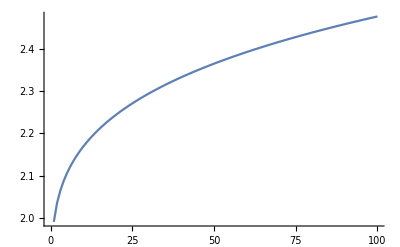

```mathematica
InvFitAcrossW=Table[NumSolInvFit[W,270,0.9,0.9,1,0.1,0.01,0.1],{W,10,1000,10}];
ListLinePlot[InvFitAcrossW]
```

This is true if you increase the temperature (here increasing temperature from 270 to 310). Notice, however, that R_0 is lower for higher temperatures, indicating that increasing temperature negatively affects R_0.

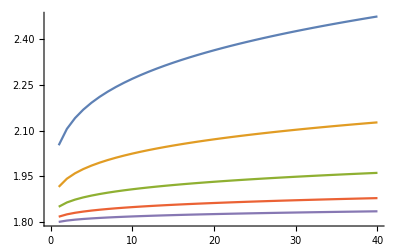

```mathematica
InvFitAcrossWT=Table[Table[NumSolInvFit[W,T,0.9,0.9,1,0.1,0.01,0.1],{W,25,1000,25}],{T,270,310,10}];
ListLinePlot[InvFitAcrossWT]
```

It also holds if you increase the cost of generalism (here decreasing c from 0.9 to 0.5):

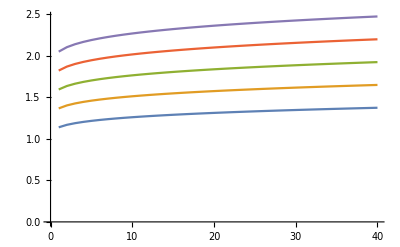

```mathematica
InvFitAcrossWc=Table[Table[NumSolInvFit[W,270,c,0.9,1,0.1,0.01,0.1],{W,25,1000,25}],{c,0.5,0.9,0.1}];ListLinePlot[InvFitAcrossWc]
```

It also holds if you reduce the size of the secondary host (here decreasing f from 0.9 to 0.5):

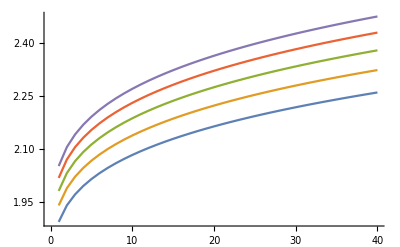

```mathematica
InvFitAcrossWf=Table[Table[NumSolInvFit[W,270,0.9,f,1,0.1,0.01,0.1],{W,25,1000,25}],{f,0.5,0.9,0.1}];
ListLinePlot[InvFitAcrossWf]
```

It also holds if you reduce the number of intermediate hosts (here N_T ranges from 0.25 to 2):

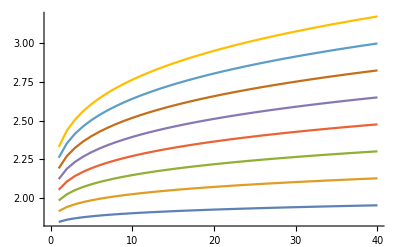

```mathematica
InvFitAcrossWNT=Table[Table[NumSolInvFit[W,270,0.9,0.9,NT,0.1,0.01,0.1],{W,25,1000,25}],{NT,0.25,2,0.25}];
ListLinePlot[InvFitAcrossWNT]
```

It also holds if you change the transmission rate to intermediate hosts (here β ranges from 0.05 to 0.55):

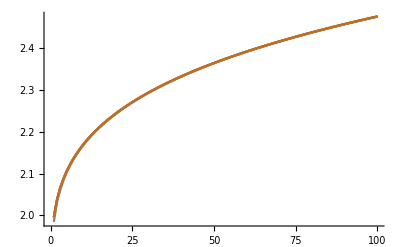

```mathematica
InvFitAcrossWB=Table[Table[NumSolInvFit[W,270,0.9,0.9,1,B,0.01,0.1],{W,10,1000,10}],{B,0.05,0.55,0.1}];
ListLinePlot[InvFitAcrossWB]
```

It also holds if you change the rate parasites are lost from the environment (here γ ranges from 0.01 to 0.1):

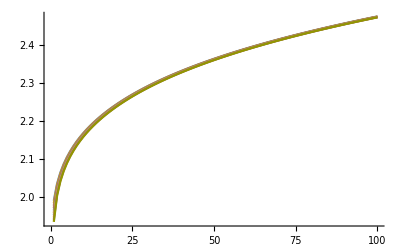

```mathematica
InvFitAcrossWg=Table[Table[NumSolInvFit[W,270,0.9,0.9,1,0.1,g,0.1],{W,10,1000,10}],{g,0.01,0.1,0.01}];
ListLinePlot[InvFitAcrossWg]
```

It also holds if you change the ingestion rate of the definitive hosts:

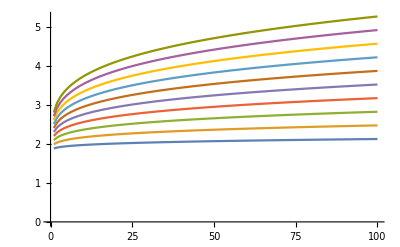

```mathematica
InvFitAcrossWa=Table[Table[NumSolInvFit[W,270,0.9,0.9,1,0.1,0.01,a],{W,10,1000,10}],{a,0.05,0.5,0.05}];
ListLinePlot[InvFitAcrossWa]
```

Increasing temperature decreases R_0:

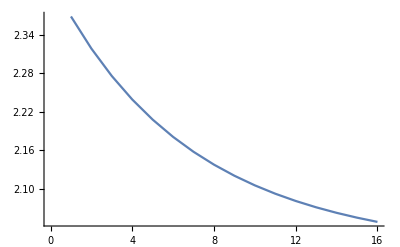

```mathematica
InvFitAcrossT=Table[NumSolInvFit[100,T,0.9,0.9,1],{T,270,300,2}];
ListLinePlot[InvFitAcrossT]
```

### Case 2: Trophic transmission; two specialist parasites; parasites regulate definitive host population sizes; avoidance of infected intermediate hosts

Now we assume that there are two specialist parasites exploiting the same intermediate host, but infecting different definitive hosts. We let N_(2I r) track the number of intermediate hosts infected with the second specialist parasite and D_(2I r) track the number of secondary definitive hosts infected by the second specialist parasite.

```mathematica
dN1irdt=β (NT-N1ir-N2ir-Nim) P1r-a1(D1s+D1ir+D1im) N1ir-a2(D2s+D2ir+D2im) N1ir;
dN2irdt=β (NT-N1ir-N2ir-Nim) P2r-a1(D1s+D1ir+D1im)N2ir-a2 (D2s+D2ir+D2im) N2ir;
dNimdt=β (NT-N1ir-N2ir-Nim) Pm-a1(D1s+D1ir+D1im) Nim-a2 (D2s+D2ir+D2im) Nim;

dD1sdt=r1 (D1s+D1ir+D1im)(1-(D1s+D1ir+D1im)/K1)-a1 D1s (N1ir+Nim);
dD2sdt=r2 (D2s+D2ir+D2im)(1-(D2s+D2ir+D2im)/K2)-a2 D2s (N2ir+Nim);
dD1irdt=a1 D1s N1ir-μ1 D1ir;
dD2irdt=a2 D2s N2ir-μ2 D2ir;
dD1imdt=a1 D1s Nim-μ1 D1im;
dD2imdt=a2 D2s Nim-μ2 D2im;

dP1rdt=λ1 D1ir-β (NT-N1ir-N2ir-Nim) P1r-γ P1r;
dP2rdt=λ2 D2ir-β (NT-N1ir-N2ir-Nim) P2r-γ P2r;
dPmdt=c λ1 D1im+c λ2 D2im-β (NT-N1ir-N2ir-Nim) Pm-γ Pm;
```

To determine whether the generalist can invade this system, we again look at the Jacobian.

```mathematica
J={{D[dN1irdt,N1ir],D[dN1irdt,D1s],D[dN1irdt,D1ir],D[dN1irdt,P1r],
D[dN1irdt,N2ir],D[dN1irdt,D2s],D[dN1irdt,D2ir],D[dN1irdt,P2r],
D[dN1irdt,Nim],D[dN1irdt,D1im],D[dN1irdt,D2im],D[dN1irdt,Pm]},
{D[dD1sdt,N1ir],D[dD1sdt,D1s],D[dD1sdt,D1ir],D[dD1sdt,P1r],
D[dD1sdt,N2ir],D[dD1sdt,D2s],D[dD1sdt,D2ir],D[dD1sdt,P2r],
D[dD1sdt,Nim],D[dD1sdt,D1im],D[dD1sdt,D2im],D[dD1sdt,Pm]},
{D[dD1irdt,N1ir],D[dD1irdt,D1s],D[dD1irdt,D1ir],D[dD1irdt,P1r],
D[dD1irdt,N2ir],D[dD1irdt,D2s],D[dD1irdt,D2ir],D[dD1irdt,P2r],
D[dD1irdt,Nim],D[dD1irdt,D1im],D[dD1irdt,D2im],D[dD1irdt,Pm]},
{D[dP1rdt,N1ir],D[dP1rdt,D1s],D[dP1rdt,D1ir],D[dP1rdt,P1r],
D[dP1rdt,N2ir],D[dP1rdt,D2s],D[dP1rdt,D2ir],D[dP1rdt,P2r],
D[dP1rdt,Nim],D[dP1rdt,D1im],D[dP1rdt,D2im],D[dP1rdt,Pm]},
{D[dN2irdt,N1ir],D[dN2irdt,D1s],D[dN2irdt,D1ir],D[dN2irdt,P1r],
D[dN2irdt,N2ir],D[dN2irdt,D2s],D[dN2irdt,D2ir],D[dN2irdt,P2r],
D[dN2irdt,Nim],D[dN2irdt,D1im],D[dN2irdt,D2im],D[dN2irdt,Pm]},
{D[dD2sdt,N1ir],D[dD2sdt,D1s],D[dD2sdt,D1ir],D[dD2sdt,P1r],
D[dD2sdt,N2ir],D[dD2sdt,D2s],D[dD2sdt,D2ir],D[dD2sdt,P2r],
D[dD2sdt,Nim],D[dD2sdt,D1im],D[dD2sdt,D2im],D[dD2sdt,Pm]},
{D[dD2irdt,N1ir],D[dD2irdt,D1s],D[dD2irdt,D1ir],D[dD2irdt,P1r],
D[dD2irdt,N2ir],D[dD2irdt,D2s],D[dD2irdt,D2ir],D[dD2irdt,P2r],
D[dD2irdt,Nim],D[dD2irdt,D1im],D[dD2irdt,D2im],D[dD2irdt,Pm]},
{D[dP2rdt,N1ir],D[dP2rdt,D1s],D[dP2rdt,D1ir],D[dP2rdt,P1r],
D[dP2rdt,N2ir],D[dP2rdt,D2s],D[dP2rdt,D2ir],D[dP2rdt,P2r],
D[dP2rdt,Nim],D[dP2rdt,D1im],D[dP2rdt,D2im],D[dP2rdt,Pm]},
{D[dNimdt,N1ir],D[dNimdt,D1s],D[dNimdt,D1ir],D[dNimdt,P1r],
D[dNimdt,N2ir],D[dNimdt,D2s],D[dNimdt,D2ir],D[dNimdt,P2r],
D[dNimdt,Nim],D[dNimdt,D1im],D[dNimdt,D2im],D[dNimdt,Pm]},
{D[dD1imdt,N1ir],D[dD1imdt,D1s],D[dD1imdt,D1ir],D[dD1imdt,P1r],
D[dD1imdt,N2ir],D[dD1imdt,D2s],D[dD1imdt,D2ir],D[dD1imdt,P2r],
D[dD1imdt,Nim],D[dD1imdt,D1im],D[dD1imdt,D2im],D[dD1imdt,Pm]},
{D[dD2imdt,N1ir],D[dD2imdt,D1s],D[dD2imdt,D1ir],D[dD2imdt,P1r],
D[dD2imdt,N2ir],D[dD2imdt,D2s],D[dD2imdt,D2ir],D[dD2imdt,P2r],
D[dD2imdt,Nim],D[dD2imdt,D1im],D[dD2imdt,D2im],D[dD2imdt,Pm]},
{D[dPmdt,N1ir],D[dPmdt,D1s],D[dPmdt,D1ir],D[dPmdt,P1r],
D[dPmdt,N2ir],D[dPmdt,D2s],D[dPmdt,D2ir],D[dPmdt,P2r],
D[dPmdt,Nim],D[dPmdt,D1im],D[dPmdt,D2im],D[dPmdt,Pm]}}/.{Nim->0,D1im->0,D2im->0,Pm->0};
```

As before, this matrix is upper block triangular. The upper left submatrix determines the stability of the system that doesn’t include the generalist parasite. It will be helpful to look at the eigenvalues of this submatrix at the parasite-free equilibrium when both specialist parasites are absent (N_(1I r)=0, N_(2I r)=0, D_(1S)=K_1, D_(1 I r)=0, D_(2 S)=K_2, D_(2 I r)=0, P_1=0, P_2=0). In particular, we want all of these eigenvalues to be positive to guarantee that the specialist parasites can both persist in the system. Notice that this matrix is block diagonal, so we can simply look at the eigenvalues of each submatrix to determine the eigenvalues of the full matrix.

```mathematica
J[[1;;8,1;;8]]/.{N1ir->0,N2ir->0,D1s->K1,D1ir->0,D2s->K2,D2ir->0,P1r->0,P2r->0}//MatrixForm
```

(-a1 K1-a2 K2 | 0 | 0 | NT β | 0 | 0 | 0 | 0
-a1 K1 | -r1 | -r1 | 0 | 0 | 0 | 0 | 0
a1 K1 | 0 | -μ1 | 0 | 0 | 0 | 0 | 0
0 | 0 | λ1 | -NT β-γ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -a1 K1-a2 K2 | 0 | 0 | NT β
0 | 0 | 0 | 0 | -a2 K2 | -r2 | -r2 | 0
0 | 0 | 0 | 0 | a2 K2 | 0 | -μ2 | 0
0 | 0 | 0 | 0 | 0 | 0 | λ2 | -NT β-γ)

Applying the next generation matrix, we find that for the specialist-absent system to be unstable, we require that
(β N_T)/(β N_T+γ) ((a_1 K_1)/(a_1 K_1+a_2 K_2)λ_1/μ_1)>1 and (β N_T)/(β N_T+γ) ((a_2 K_2)/(a_1 K_1+a_2 K_2)λ_2/μ_2)>1

```mathematica
F1={{0,0,0,NT β},{0,0,0,0},{a1 K1,0,0,0},{0,0,λ1,0}};
V1={{a1 K1+a2 K2,0,0,0},{a1 K1,r1,r1,0},{0,0,μ1,0},{0,0,0,NT β+γ}};
(J[[1;;4,1;;4]]/.{N1ir->0,N2ir->0,D1s->K1,D1ir->0,D2s->K2,D2ir->0,P1r->0,P2r->0})==F1-V1
Eigenvalues[Dot[F1,Inverse[V1]]]
(Eigenvalues[Dot[F1,Inverse[V1]]][[2]])^3==(β NT)/(β NT+γ)((a1 K1)/(a1 K1+a2 K2) λ1/μ1)
F2={{0,0,0,NT β},{0,0,0,0},{a2 K2,0,0,0},{0,0,λ2,0}};
V2={{a1 K1+a2 K2,0,0,0},{a2 K2,r2,r2,0},{0,0,μ2,0},{0,0,0,NT β+γ}};
(J[[5;;8,5;;8]]/.{N1ir->0,N2ir->0,D1s->K1,D1ir->0,D2s->K2,D2ir->0,P1r->0,P2r->0})==F2-V2
Eigenvalues[Dot[F2,Inverse[V2]]]
(Eigenvalues[Dot[F2,Inverse[V2]]][[2]])^3==(β NT)/(β NT+γ)((a2 K2)/(a1 K1+a2 K2) λ2/μ2)
```

True

{0,(a1^(1/3) K1^(1/3) NT^(1/3) β^(1/3) λ1^(1/3))/((a1 K1+a2 K2)^(1/3) (NT β+γ)^(1/3) μ1^(1/3)),-((-1)^(1/3) a1^(1/3) K1^(1/3) NT^(1/3) β^(1/3) λ1^(1/3))/((a1 K1+a2 K2)^(1/3) (NT β+γ)^(1/3) μ1^(1/3)),((-1)^(2/3) a1^(1/3) K1^(1/3) NT^(1/3) β^(1/3) λ1^(1/3))/((a1 K1+a2 K2)^(1/3) (NT β+γ)^(1/3) μ1^(1/3))}

True

True

{0,(a2^(1/3) K2^(1/3) NT^(1/3) β^(1/3) λ2^(1/3))/((a1 K1+a2 K2)^(1/3) (NT β+γ)^(1/3) μ2^(1/3)),-((-1)^(1/3) a2^(1/3) K2^(1/3) NT^(1/3) β^(1/3) λ2^(1/3))/((a1 K1+a2 K2)^(1/3) (NT β+γ)^(1/3) μ2^(1/3)),((-1)^(2/3) a2^(1/3) K2^(1/3) NT^(1/3) β^(1/3) λ2^(1/3))/((a1 K1+a2 K2)^(1/3) (NT β+γ)^(1/3) μ2^(1/3))}

True

We assume that both of those inequalities are satisfied. Whether the generalist can invade the system depends on the eigenvalues of the lower right submatrix of J:

```mathematica
MatrixForm[J[[9;;12,9;;12]]]
```

(-a1 (D1ir+D1s)-a2 (D2ir+D2s) | 0 | 0 | (-N1ir-N2ir+NT) β
a1 D1s | -μ1 | 0 | 0
a2 D2s | 0 | -μ2 | 0
0 | c λ1 | c λ2 | -(-N1ir-N2ir+NT) β-γ)

Using the next generation matrix theorem, the Jacobian will have a positive eigenvalue whenever the second value is greater than 1.

```mathematica
F={{0,0,0,(NT-N1ir-N2ir) β},{a1 D1s,0,0,0},{a2 D2s,0,0,0},{0,c λ1,c λ2,0}};
V={{a1 (D1ir+D1s)+a2(D2ir+D2s),0,0,0},{0,μ1,0,0},{0,0,μ2,0},{0,0,0,(NT-N1ir-N2ir) β+γ}};
J[[9;;12,9;;12]]==F-V//Simplify
Eigenvalues[Dot[F,Inverse[V]]]
```

True

{0,(c^(1/3) (N1ir+N2ir-NT)^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2ir+a2 D2s)^(1/3) (N1ir β+N2ir β-NT β-γ)^(1/3) μ1^(1/3) μ2^(1/3)),-((-1)^(1/3) c^(1/3) (N1ir+N2ir-NT)^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2ir+a2 D2s)^(1/3) (N1ir β+N2ir β-NT β-γ)^(1/3) μ1^(1/3) μ2^(1/3)),((-1)^(2/3) c^(1/3) (N1ir+N2ir-NT)^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2ir+a2 D2s)^(1/3) (N1ir β+N2ir β-NT β-γ)^(1/3) μ1^(1/3) μ2^(1/3))}

This eigenvalue is equivalent to the expression given below:

```mathematica
((c^(1/3) (N1ir+N2ir-NT)^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2ir+a2 D2s)^(1/3) (N1ir β+N2ir β-NT β-γ)^(1/3) μ1^(1/3) μ2^(1/3)))^3==((NT-N1ir-N2ir) β)/((NT-N1ir-N2ir) β+γ) ((a1 D1s)/(a1 (D1ir+D1s)+a2 (D2ir+D2s)) (c λ1)/μ1+(a2 D2s)/(a1 (D1ir+D1s)+a2 (D2ir+D2s)) (c λ2)/μ2)//Simplify
```

True

As before, it is impossible to make headway analytically, so we must resort to numerical solutions.

```mathematica
NumSolInvFit=Function[{W,T,c,f,NTot,B,g,a},allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4),r1->r0 Exp[-Ε/(k T)] W^(-1/4),r2->r0 Exp[-Ε/(k T)] (f W)^(-1/4)};pars={Ε->0.45,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10,β->B,γ->g,a1->a,a2->a,NT->NTot};
(*Print[(β NT)/(β NT+γ)((a1 K1)/(a1 K1+a2 K2) λ1/μ1)/.allom/.pars];*)
(*Print[(β NT)/(β NT+γ)((a2 K2)/(a1 K1+a2 K2) λ2/μ2)/.allom/.pars];*)
DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];Soln=NDSolve[({
N1ir'[t]==β (NT-N1ir[t]-N2ir[t]) P1r[t]-a1(D1s[t]+D1ir[t]) N1ir[t]-a2(D2s[t]+D2ir[t]) N1ir[t],
N2ir'[t]==β (NT-N1ir[t]-N2ir[t]) P2r[t]-a1(D1s[t]+D1ir[t]) N2ir[t]-a2(D2s[t]+D2ir[t]) N2ir[t],
D1s'[t]==r1 (D1s[t]+D1ir[t]) (1-(D1s[t]+D1ir[t])/K1)-a1 D1s[t] N1ir[t],
D2s'[t]==r2 (D2s[t]+D2ir[t]) (1-(D2s[t]+D2ir[t])/K2)-a2 D2s[t] N2ir[t],
D1ir'[t]==a1 D1s[t] N1ir[t]-μ1 D1ir[t],
D2ir'[t]==a2 D2s[t] N2ir[t]-μ1 D2ir[t],
P1r'[t]==λ1 D1ir[t]-β (NT-N1ir[t]-N2ir[t]) P1r[t]-γ P1r[t],
P2r'[t]==λ1 D1ir[t]-β (NT-N1ir[t]-N2ir[t]) P2r[t]-γ P2r[t],
N1ir[0]==0,N2ir[0]==0,
D1s[0]==0.1,D2s[0]==0.1,
D1ir[0]==0,D2ir[0]==0,
P1r[0]==1,P2r[0]==1}/.allom/.pars),
{N1ir,N2ir,D1s,D1ir,D2s,D2ir,P1r,P2r},{t,0,1000},
Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
(* Print[{N1ir->(N1ir[1000]/.Soln)[[1]],N2ir->(N2ir[1000]/.Soln)[[1]],D1s->(D1s[1000]/.Soln)[[1]],D1ir->(D1ir[1000]/.Soln)[[1]],D2s->(D2s[1000]/.Soln)[[1]],D2ir->(D2ir[1000]/.Soln)[[1]]}] *);
((NT-N1ir-N2ir) β)/((NT-N1ir-N2ir) β+γ) ((a1 D1s)/(a1 (D1ir+D1s)+a2 (D2ir+D2s)) (c λ1)/μ1+(a2 D2s)/(a1 (D1ir+D1s)+a2 (D2ir+D2s)) (c λ2)/μ2)/.{N1ir->(N1ir[1000]/.Soln)[[1]],N2ir->(N2ir[1000]/.Soln)[[1]],D1s->(D1s[1000]/.Soln)[[1]],D1ir->(D1ir[1000]/.Soln)[[1]],D2s->(D2s[1000]/.Soln)[[1]],D2ir->(D2ir[1000]/.Soln)[[1]]}/.allom/.pars
];
```

One case is sufficient to demonstrate that the response of the generalist’s R_0 to changes in host body size is much more complex here. Consider the effect of changing the definitive host body sizes across a gradient of intermediate host abundance. You can see very clearly that the responses depend on the value of N_T: when N_T is small, increasing host mass increases R_0; when N_T is large, increasing host mass first increases, then decreases R_0. 

In reality, the abundance of the definitive host’s prey is likely to be related to the size of the definitive host: in general, larger-bodied hosts are more likely to consume larger-bodied prey, whose carrying capacities would decrease commensurately. That is, as definitive host body size goes up, you would expect intermediate host carrying capacity to go down.

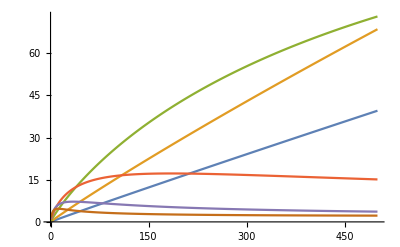

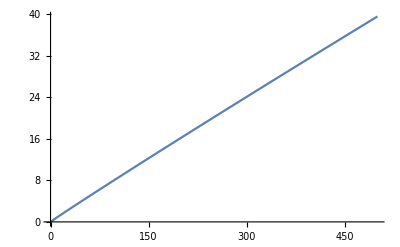

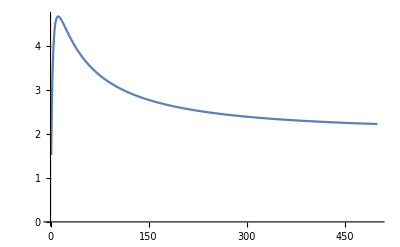

```mathematica
InvFitAcrossWNT=Table[Table[NumSolInvFit[W,270,0.9,0.9,NT,0.01,0.1,0.01],{W,10,5000,10}],{NT,{0.1,0.2,0.5,1,1.5,2}}];
ListLinePlot[InvFitAcrossWNT]
ListLinePlot[InvFitAcrossWNT[[1]]]
ListLinePlot[InvFitAcrossWNT[[6]]]
```

Increasing temperature also has a much more complex effect on R_0: when N_T is large, increasing temperature increases R_0, but when N_T is small, increasing temperature decreases R_0.

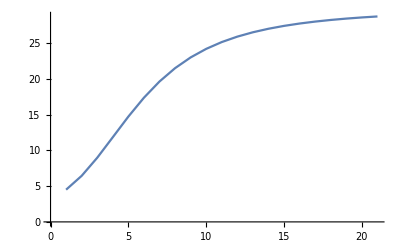

```mathematica
InvFitAcrossWT=Table[NumSolInvFit[200,T,0.9,0.9,2,0.01,0.1,0.01],{T,270,310,2}];
ListLinePlot[InvFitAcrossWT]
```

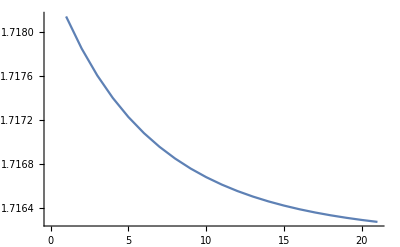

```mathematica
InvFitAcrossWT=Table[NumSolInvFit[200,T,0.9,0.9,0.1,0.01,0.1,0.01],{T,270,310,2}];
ListLinePlot[InvFitAcrossWT]
```

### Case 3: Trophic transmission; two specialist parasites; parasites regulate definitive host population sizes; no avoidance of infected intermediate hosts

This case assumes that the parasite cannot determine whether an intermediate host is infected or not. Thus both susceptible and infected intermediate hosts remove parasites from the environment, but only consumption by a susceptible host can produce a new infection.

```mathematica
dN1irdt=β (NT-N1ir-N2ir-Nim) P1r-a1(D1s+D1ir+D1im) N1ir-a2(D2s+D2ir+D2im) N1ir;
dN2irdt=β (NT-N1ir-N2ir-Nim) P2r-a1(D1s+D1ir+D1im)N2ir-a2 (D2s+D2ir+D2im) N2ir;
dNimdt=β (NT-N1ir-N2ir-Nim) Pm-a1(D1s+D1ir+D1im) Nim-a2 (D2s+D2ir+D2im) Nim;

dD1sdt=r1 (D1s+D1ir+D1im)(1-(D1s+D1ir+D1im)/K1)-a1 D1s (N1ir+Nim);
dD2sdt=r2 (D2s+D2ir+D2im)(1-(D2s+D2ir+D2im)/K2)-a2 D2s (N2ir+Nim);
dD1irdt=a1 D1s N1ir-μ1 D1ir;
dD2irdt=a2 D2s N2ir-μ2 D2ir;
dD1imdt=a1 D1s Nim-μ1 D1im;
dD2imdt=a2 D2s Nim-μ2 D2im;

dP1rdt=λ1 D1ir-β NT P1r-γ P1r;
dP2rdt=λ2 D2ir-β NT P2r-γ P2r;
dPmdt=c λ1 D1im+c λ2 D2im-β NT Pm-γ Pm;
```

To determine whether the generalist can invade this system, we again look at the Jacobian.

```mathematica
J={{D[dN1irdt,N1ir],D[dN1irdt,D1s],D[dN1irdt,D1ir],D[dN1irdt,P1r],
D[dN1irdt,N2ir],D[dN1irdt,D2s],D[dN1irdt,D2ir],D[dN1irdt,P2r],
D[dN1irdt,Nim],D[dN1irdt,D1im],D[dN1irdt,D2im],D[dN1irdt,Pm]},
{D[dD1sdt,N1ir],D[dD1sdt,D1s],D[dD1sdt,D1ir],D[dD1sdt,P1r],
D[dD1sdt,N2ir],D[dD1sdt,D2s],D[dD1sdt,D2ir],D[dD1sdt,P2r],
D[dD1sdt,Nim],D[dD1sdt,D1im],D[dD1sdt,D2im],D[dD1sdt,Pm]},
{D[dD1irdt,N1ir],D[dD1irdt,D1s],D[dD1irdt,D1ir],D[dD1irdt,P1r],
D[dD1irdt,N2ir],D[dD1irdt,D2s],D[dD1irdt,D2ir],D[dD1irdt,P2r],
D[dD1irdt,Nim],D[dD1irdt,D1im],D[dD1irdt,D2im],D[dD1irdt,Pm]},
{D[dP1rdt,N1ir],D[dP1rdt,D1s],D[dP1rdt,D1ir],D[dP1rdt,P1r],
D[dP1rdt,N2ir],D[dP1rdt,D2s],D[dP1rdt,D2ir],D[dP1rdt,P2r],
D[dP1rdt,Nim],D[dP1rdt,D1im],D[dP1rdt,D2im],D[dP1rdt,Pm]},
{D[dN2irdt,N1ir],D[dN2irdt,D1s],D[dN2irdt,D1ir],D[dN2irdt,P1r],
D[dN2irdt,N2ir],D[dN2irdt,D2s],D[dN2irdt,D2ir],D[dN2irdt,P2r],
D[dN2irdt,Nim],D[dN2irdt,D1im],D[dN2irdt,D2im],D[dN2irdt,Pm]},
{D[dD2sdt,N1ir],D[dD2sdt,D1s],D[dD2sdt,D1ir],D[dD2sdt,P1r],
D[dD2sdt,N2ir],D[dD2sdt,D2s],D[dD2sdt,D2ir],D[dD2sdt,P2r],
D[dD2sdt,Nim],D[dD2sdt,D1im],D[dD2sdt,D2im],D[dD2sdt,Pm]},
{D[dD2irdt,N1ir],D[dD2irdt,D1s],D[dD2irdt,D1ir],D[dD2irdt,P1r],
D[dD2irdt,N2ir],D[dD2irdt,D2s],D[dD2irdt,D2ir],D[dD2irdt,P2r],
D[dD2irdt,Nim],D[dD2irdt,D1im],D[dD2irdt,D2im],D[dD2irdt,Pm]},
{D[dP2rdt,N1ir],D[dP2rdt,D1s],D[dP2rdt,D1ir],D[dP2rdt,P1r],
D[dP2rdt,N2ir],D[dP2rdt,D2s],D[dP2rdt,D2ir],D[dP2rdt,P2r],
D[dP2rdt,Nim],D[dP2rdt,D1im],D[dP2rdt,D2im],D[dP2rdt,Pm]},
{D[dNimdt,N1ir],D[dNimdt,D1s],D[dNimdt,D1ir],D[dNimdt,P1r],
D[dNimdt,N2ir],D[dNimdt,D2s],D[dNimdt,D2ir],D[dNimdt,P2r],
D[dNimdt,Nim],D[dNimdt,D1im],D[dNimdt,D2im],D[dNimdt,Pm]},
{D[dD1imdt,N1ir],D[dD1imdt,D1s],D[dD1imdt,D1ir],D[dD1imdt,P1r],
D[dD1imdt,N2ir],D[dD1imdt,D2s],D[dD1imdt,D2ir],D[dD1imdt,P2r],
D[dD1imdt,Nim],D[dD1imdt,D1im],D[dD1imdt,D2im],D[dD1imdt,Pm]},
{D[dD2imdt,N1ir],D[dD2imdt,D1s],D[dD2imdt,D1ir],D[dD2imdt,P1r],
D[dD2imdt,N2ir],D[dD2imdt,D2s],D[dD2imdt,D2ir],D[dD2imdt,P2r],
D[dD2imdt,Nim],D[dD2imdt,D1im],D[dD2imdt,D2im],D[dD2imdt,Pm]},
{D[dPmdt,N1ir],D[dPmdt,D1s],D[dPmdt,D1ir],D[dPmdt,P1r],
D[dPmdt,N2ir],D[dPmdt,D2s],D[dPmdt,D2ir],D[dPmdt,P2r],
D[dPmdt,Nim],D[dPmdt,D1im],D[dPmdt,D2im],D[dPmdt,Pm]}}/.{Nim->0,D1im->0,D2im->0,Pm->0};
```

As before, this matrix is upper block triangular. The upper left submatrix determines the stability of the system that doesn’t include the generalist parasite. It will be helpful to look at the eigenvalues of this submatrix at the parasite-free equilibrium when both specialist parasites are absent (N_(1I r)=0, N_(2I r)=0, D_(1S)=K_1, D_(1 I r)=0, D_(2 S)=K_2, D_(2 I r)=0, P_1=0, P_2=0)? In particular, we want all of these eigenvalues to be positive to guarantee that the specialist parasites can both persist in the system. Notice that this matrix is block diagonal, so we can simply look at the eigenvalues of each submatrix to determine the eigenvalues of the full matrix.

```mathematica
J[[1;;8,1;;8]]/.{N1ir->0,N2ir->0,D1s->K1,D1ir->0,D2s->K2,D2ir->0,P1r->0,P2r->0}//MatrixForm
```

(-a1 K1-a2 K2 | 0 | 0 | NT β | 0 | 0 | 0 | 0
-a1 K1 | -r1 | -r1 | 0 | 0 | 0 | 0 | 0
a1 K1 | 0 | -μ1 | 0 | 0 | 0 | 0 | 0
0 | 0 | λ1 | -NT β-γ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -a1 K1-a2 K2 | 0 | 0 | NT β
0 | 0 | 0 | 0 | -a2 K2 | -r2 | -r2 | 0
0 | 0 | 0 | 0 | a2 K2 | 0 | -μ2 | 0
0 | 0 | 0 | 0 | 0 | 0 | λ2 | -NT β-γ)

Applying the next generation matrix, we find that for the specialist-absent system to be unstable, we require that
(β N_T)/(β N_T+γ) ((a_1 K_1)/(a_1 K_1+a_2 K_2)λ_1/μ_1)>1 and (β N_T)/(β N_T+γ) ((a_2 K_2)/(a_1 K_1+a_2 K_2)λ_2/μ_2)>1

```mathematica
F1={{0,0,0,NT β},{0,0,0,0},{a1 K1,0,0,0},{0,0,λ1,0}};
V1={{a1 K1+a2 K2,0,0,0},{a1 K1,r1,r1,0},{0,0,μ1,0},{0,0,0,NT β+γ}};
(J[[1;;4,1;;4]]/.{N1ir->0,N2ir->0,D1s->K1,D1ir->0,D2s->K2,D2ir->0,P1r->0,P2r->0})==F1-V1
Eigenvalues[Dot[F1,Inverse[V1]]]
(Eigenvalues[Dot[F1,Inverse[V1]]][[2]])^3==(β NT)/(β NT+γ)((a1 K1)/(a1 K1+a2 K2) λ1/μ1)
F2={{0,0,0,NT β},{0,0,0,0},{a2 K2,0,0,0},{0,0,λ2,0}};
V2={{a1 K1+a2 K2,0,0,0},{a2 K2,r2,r2,0},{0,0,μ2,0},{0,0,0,NT β+γ}};
(J[[5;;8,5;;8]]/.{N1ir->0,N2ir->0,D1s->K1,D1ir->0,D2s->K2,D2ir->0,P1r->0,P2r->0})==F2-V2
Eigenvalues[Dot[F2,Inverse[V2]]]
(Eigenvalues[Dot[F2,Inverse[V2]]][[2]])^3==(β NT)/(β NT+γ)((a2 K2)/(a1 K1+a2 K2) λ2/μ2)
```

True

{0,(a1^(1/3) K1^(1/3) NT^(1/3) β^(1/3) λ1^(1/3))/((a1 K1+a2 K2)^(1/3) (NT β+γ)^(1/3) μ1^(1/3)),-((-1)^(1/3) a1^(1/3) K1^(1/3) NT^(1/3) β^(1/3) λ1^(1/3))/((a1 K1+a2 K2)^(1/3) (NT β+γ)^(1/3) μ1^(1/3)),((-1)^(2/3) a1^(1/3) K1^(1/3) NT^(1/3) β^(1/3) λ1^(1/3))/((a1 K1+a2 K2)^(1/3) (NT β+γ)^(1/3) μ1^(1/3))}

True

True

{0,(a2^(1/3) K2^(1/3) NT^(1/3) β^(1/3) λ2^(1/3))/((a1 K1+a2 K2)^(1/3) (NT β+γ)^(1/3) μ2^(1/3)),-((-1)^(1/3) a2^(1/3) K2^(1/3) NT^(1/3) β^(1/3) λ2^(1/3))/((a1 K1+a2 K2)^(1/3) (NT β+γ)^(1/3) μ2^(1/3)),((-1)^(2/3) a2^(1/3) K2^(1/3) NT^(1/3) β^(1/3) λ2^(1/3))/((a1 K1+a2 K2)^(1/3) (NT β+γ)^(1/3) μ2^(1/3))}

True

We assume that both of those inequalities are satisfied. Whether the generalist can invade the system depends on the eigenvalues of the lower right submatrix of J:

```mathematica
MatrixForm[J[[9;;12,9;;12]]]
```

(-a1 (D1ir+D1s)-a2 (D2ir+D2s) | 0 | 0 | (-N1ir-N2ir+NT) β
a1 D1s | -μ1 | 0 | 0
a2 D2s | 0 | -μ2 | 0
0 | c λ1 | c λ2 | -NT β-γ)

Using the next generation matrix theorem, the invasion of the generalist requires that one of the following eigenvalues be larger than 1 in magnitude.

```mathematica
F={{0,0,0,(NT-N1ir-N2ir) β},{a1 D1s,0,0,0},{a2 D2s,0,0,0},{0,c λ1,c λ2,0}};
V={{a1 (D1ir+D1s)+a2(D2ir+D2s),0,0,0},{0,μ1,0,0},{0,0,μ2,0},{0,0,0,β NT+γ}};
J[[9;;12,9;;12]]==F-V//Simplify
Eigenvalues[Dot[F,Inverse[V]]]
```

True

{0,-(c^(1/3) (N1ir+N2ir-NT)^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2ir+a2 D2s)^(1/3) (NT β+γ)^(1/3) μ1^(1/3) μ2^(1/3)),((-1)^(1/3) c^(1/3) (N1ir+N2ir-NT)^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2ir+a2 D2s)^(1/3) (NT β+γ)^(1/3) μ1^(1/3) μ2^(1/3)),-((-1)^(2/3) c^(1/3) (N1ir+N2ir-NT)^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2ir+a2 D2s)^(1/3) (NT β+γ)^(1/3) μ1^(1/3) μ2^(1/3))}

```mathematica
(-(c^(1/3) (N1ir+N2ir-NT)^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2ir+a2 D2s)^(1/3) (NT β+γ)^(1/3) μ1^(1/3) μ2^(1/3)))^3==(c (NT-N1ir-N2ir) β (a2 D2s λ2 μ1+a1 D1s λ1 μ2))/((a1 D1ir+a1 D1s+a2 D2ir+a2 D2s) (NT β+γ) μ1 μ2)//Simplify
```

True

The invasion condition can be rewritten as:

```mathematica
(c (NT-N1ir-N2ir) β (a2 D2s λ2 μ1+a1 D1s λ1 μ2))/((a1 D1ir+a1 D1s+a2 D2ir+a2 D2s) (NT β+γ) μ1 μ2)==(β (NT-N1ir-N2ir))/(β NT+γ)((a1 D1s)/(a1 (D1ir+D1s)+a2 (D2ir+D2s)) (c λ1)/μ1+(a2 D2s)/(a1 (D1ir+D1s)+a2 (D2ir+D2s)) (c λ2)/μ2)//Simplify
```

True

As before, it is impossible to make headway analytically, so we must resort to numerical solutions.

```mathematica
NumSolInvFit=Function[{W,T,c,f,NTot,B,g,a},allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4),r1->r0 Exp[-Ε/(k T)] W^(-1/4),r2->r0 Exp[-Ε/(k T)] (f W)^(-1/4)};pars={Ε->0.45,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10,β->B,γ->g,a1->a,a2->a,NT->NTot};
(*Print[(β NT)/(β NT+γ)((a1 K1)/(a1 K1+a2 K2) λ1/μ1)/.allom/.pars];*)
(*Print[(β NT)/(β NT+γ)((a2 K2)/(a1 K1+a2 K2) λ2/μ2)/.allom/.pars];*)
DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];Soln=NDSolve[({
N1ir'[t]==β (NT-N1ir[t]-N2ir[t]) P1r[t]-a1(D1s[t]+D1ir[t]) N1ir[t]-a2(D2s[t]+D2ir[t]) N1ir[t],
N2ir'[t]==β (NT-N1ir[t]-N2ir[t]) P2r[t]-a1(D1s[t]+D1ir[t]) N2ir[t]-a2(D2s[t]+D2ir[t]) N2ir[t],
D1s'[t]==r1 (D1s[t]+D1ir[t]) (1-(D1s[t]+D1ir[t])/K1)-a1 D1s[t] N1ir[t],
D2s'[t]==r2 (D2s[t]+D2ir[t]) (1-(D2s[t]+D2ir[t])/K2)-a2 D2s[t] N2ir[t],
D1ir'[t]==a1 D1s[t] N1ir[t]-μ1 D1ir[t],
D2ir'[t]==a2 D2s[t] N2ir[t]-μ1 D2ir[t],
P1r'[t]==λ1 D1ir[t]-β NT P1r[t]-γ P1r[t],
P2r'[t]==λ1 D1ir[t]-β NT P2r[t]-γ P2r[t],
N1ir[0]==0,N2ir[0]==0,
D1s[0]==0.1,D2s[0]==0.1,
D1ir[0]==0,D2ir[0]==0,
P1r[0]==1,P2r[0]==1}/.allom/.pars),
{N1ir,N2ir,D1s,D1ir,D2s,D2ir,P1r,P2r},{t,0,1000},
Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
(* Print[{N1ir->(N1ir[1000]/.Soln)[[1]],N2ir->(N2ir[1000]/.Soln)[[1]],D1s->(D1s[1000]/.Soln)[[1]],D1ir->(D1ir[1000]/.Soln)[[1]],D2s->(D2s[1000]/.Soln)[[1]],D2ir->(D2ir[1000]/.Soln)[[1]]}] *);
(β (NT-N1ir-N2ir))/(β NT+γ)((a1 D1s)/(a1 (D1ir+D1s)+a2 (D2ir+D2s)) (c λ1)/μ1+(a2 D2s)/(a1 (D1ir+D1s)+a2 (D2ir+D2s)) (c λ2)/μ2)/.{N1ir->(N1ir[1000]/.Soln)[[1]],N2ir->(N2ir[1000]/.Soln)[[1]],D1s->(D1s[1000]/.Soln)[[1]],D1ir->(D1ir[1000]/.Soln)[[1]],D2s->(D2s[1000]/.Soln)[[1]],D2ir->(D2ir[1000]/.Soln)[[1]]}/.allom/.pars
];
```

One case is sufficient to demonstrate that the response of the generalist’s R_0 to changes in host body size is much more complex here. Consider the effect of changing the definitive host body sizes across a gradient of intermediate host abundance. You can see very clearly that the responses depend on the value of N_T: when N_T is small, increasing host mass increases R_0; when N_T is large, increasing host mass first increases, then decreases R_0. 

In reality, the abundance of the definitive host’s prey is likely to be related to the size of the definitive host: in general, larger-bodied hosts are more likely to consume larger-bodied prey, whose carrying capacities would decrease commensurately. That is, as definitive host body size goes up, you would expect intermediate host carrying capacity to go down.

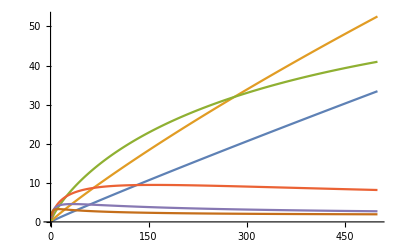

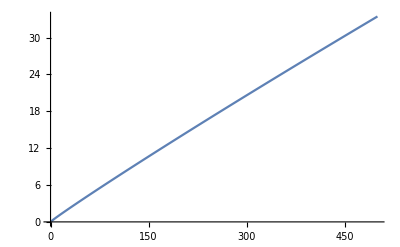

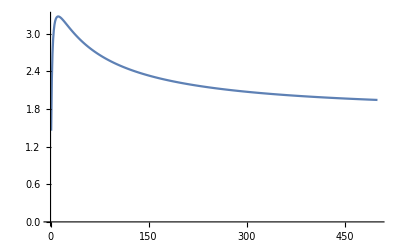

```mathematica
InvFitAcrossWNT=Table[Table[NumSolInvFit[W,270,0.9,0.9,NT,0.01,0.1,0.01],{W,10,5000,10}],{NT,{0.1,0.2,0.5,1,1.5,2}}];
ListLinePlot[InvFitAcrossWNT]
ListLinePlot[InvFitAcrossWNT[[1]]]
ListLinePlot[InvFitAcrossWNT[[6]]]
```

Increasing temperature also has a much more complex effect on R_0: when N_T is large, increasing temperature increases R_0, but when N_T is small, increasing temperature decreases R_0.

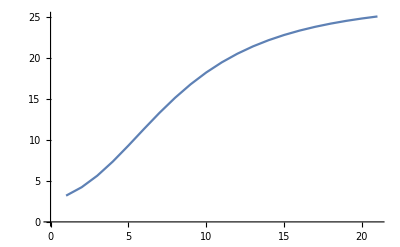

```mathematica
InvFitAcrossWT=Table[NumSolInvFit[200,T,0.9,0.9,2,0.01,0.1,0.01],{T,270,310,2}];
ListLinePlot[InvFitAcrossWT]
```

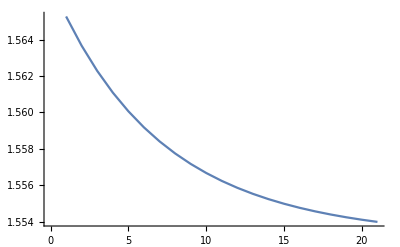

```mathematica
InvFitAcrossWT=Table[NumSolInvFit[200,T,0.9,0.9,0.1,0.01,0.1,0.01],{T,270,310,2}];
ListLinePlot[InvFitAcrossWT]
```

### Case 4: Trophic transmission; two specialist parasites; constant definitive host population sizes; avoidance of infected intermediate hosts

We assume that both the intermediate and definitive hosts have constant population size. Let K_N be the total number of intermediate hosts; let N_(1,r) be the number of intermediate hosts infected by the first specialist parasite; let N_(2,r) be the number of intermediate hosts infected by the second specialist parasite, and let N_(12,m) be the fraction of intermediate hosts infected by the generalist parasite. Then K_N-N_(1,r)-N_(2,r) is the number of susceptible intermediate hosts - we assume that each intermediate host can only be infected by a single parasite. Let K_1 be the abundance of the first definitive host population and let K_2 be the abundance of the second definitive host population. Let I_(1,r) and I_(2,r) be the numbers of the first and second definitive host populations, respectively, that are infected by the specialist parasites, and let I_(1,m) and I_(2,m) be the numbers of the definitive host populations infected by the generalist parasite. Let P_(1,r) and P_(2,r) be the numbers of the two specialist parasites in the environment and let P_(12,m) be the number of generalist parasites in the environment.

```mathematica
dN1rdt=β (KN-N1r-N2r-N12m) P1r-a N1r (K1+K2);
dN2rdt=β (KN-N1r-N2r-N12m) P2r-a N2r (K1+K2);
dN12mdt=β (KN-N1r-N2r-N12m) P12m-a N12m (K1+K2);

dI1rdt=a(K1-I1r-I1m) N1r-μ1 I1r;
dI2rdt=a(K2-I2r-I2m) N2r-μ2 I2r;
dI1mdt=a(K1-I1r-I1m) N12m-μ1 I1m;
dI2mdt=a(K2-I2r-I2m) N12m-μ2 I2m;

dP1rdt=λ1 I1r-β P1r (KN-N1r-N2r-N12m)-γ P1r;
dP2rdt=λ2 I2r-β P2r (KN-N1r-N2r-N12m)-γ P2r;
dP12mdt=c λ1 I1m+c λ2 I2m-β P12m (KN-N1r-N2r-N12m)-γ P12m;
```

The Jacobian is needed to inform us about the stability of the system.

```mathematica
J={{D[dN1rdt,N1r],D[dN1rdt,N2r],D[dN1rdt,I1r],D[dN1rdt,I2r],D[dN1rdt,P1r],D[dN1rdt,P2r],D[dN1rdt,N12m],D[dN1rdt,I1m],D[dN1rdt,I2m],D[dN1rdt,P12m]},
{D[dN2rdt,N1r],D[dN2rdt,N2r],D[dN2rdt,I1r],D[dN2rdt,I2r],D[dN2rdt,P1r],D[dN2rdt,P2r],D[dN2rdt,N12m],D[dN2rdt,I1m],D[dN2rdt,I2m],D[dN2rdt,P12m]},
{D[dI1rdt,N1r],D[dI1rdt,N2r],D[dI1rdt,I1r],D[dI1rdt,I2r],D[dI1rdt,P1r],D[dI1rdt,P2r],D[dI1rdt,N12m],D[dI1rdt,I1m],D[dI1rdt,I2m],D[dI1rdt,P12m]},
{D[dI2rdt,N1r],D[dI2rdt,N2r],D[dI2rdt,I1r],D[dI2rdt,I2r],D[dI2rdt,P1r],D[dI2rdt,P2r],D[dI2rdt,N12m],D[dI2rdt,I1m],D[dI2rdt,I2m],D[dI2rdt,P12m]},
{D[dP1rdt,N1r],D[dP1rdt,N2r],D[dP1rdt,I1r],D[dP1rdt,I2r],D[dP1rdt,P1r],D[dP1rdt,P2r],D[dP1rdt,N12m],D[dP1rdt,I1m],D[dP1rdt,I2m],D[dP1rdt,P12m]},
{D[dP2rdt,N1r],D[dP2rdt,N2r],D[dP2rdt,I1r],D[dP2rdt,I2r],D[dP2rdt,P1r],D[dP2rdt,P2r],D[dP2rdt,N12m],D[dP2rdt,I1m],D[dP2rdt,I2m],D[dP2rdt,P12m]},
{D[dN12mdt,N1r],D[dN12mdt,N2r],D[dN12mdt,I1r],D[dN12mdt,I2r],D[dN12mdt,P1r],D[dN12mdt,P2r],D[dN12mdt,N12m],D[dN12mdt,I1m],D[dN12mdt,I2m],D[dN12mdt,P12m]},
{D[dI1mdt,N1r],D[dI1mdt,N2r],D[dI1mdt,I1r],D[dI1mdt,I2r],D[dI1mdt,P1r],D[dI1mdt,P2r],D[dI1mdt,N12m],D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,P12m]},
{D[dI2mdt,N1r],D[dI2mdt,N2r],D[dI2mdt,I1r],D[dI2mdt,I2r],D[dI2mdt,P1r],D[dI2mdt,P2r],D[dI2mdt,N12m],D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,P12m]},
{D[dP12mdt,N1r],D[dP12mdt,N2r],D[dP12mdt,I1r],D[dP12mdt,I2r],D[dP12mdt,P1r],D[dP12mdt,P2r],D[dP12mdt,N12m],D[dP12mdt,I1m],D[dP12mdt,I2m],D[dP12mdt,P12m]}};
```

Before we can investigate whether the generalist can invade or not, we need to establish the conditions necessary for the specialist parasites to be able to persist in the system. That is, we are interested in the stability of the equilibrium where N_(1r), N_(2r),I_(1r), I_(2r), P_(1r) and P_(2r) are all equal to 0.

```mathematica
J[[1;;6,1;;6]]/.{N1r->0,N2r->0,I1r->0,I2r->0,P1r->0,P2r->0,N12m->0,I1m->0,I2m->0,P12m->0}//MatrixForm
```

(-a (K1+K2) | 0 | 0 | 0 | KN β | 0
0 | -a (K1+K2) | 0 | 0 | 0 | KN β
a K1 | 0 | -μ1 | 0 | 0 | 0
0 | a K2 | 0 | -μ2 | 0 | 0
0 | 0 | λ1 | 0 | -KN β-γ | 0
0 | 0 | 0 | λ2 | 0 | -KN β-γ)

Applying the next generation matrix theorem:

```mathematica
F={{0,0,0,0,KN β,0},{0,0,0,0,0,KN β},{a K1,0,0,0,0,0},{0,a K2,0,0,0,0},{0,0,λ1,0,0,0},{0,0,0,λ2,0,0}};
V={{a (K1+K2),0,0,0,0,0},{0,a (K1+K2),0,0,0,0},{0,0,μ1,0,0,0},{0,0,0,μ2,0,0},{0,0,0,0,KN β+γ,0},{0,0,0,0,0,KN β+γ}};
(J[[1;;6,1;;6]]/.{N1r->0,N2r->0,I1r->0,I2r->0,P1r->0,P2r->0,N12m->0,I1m->0,I2m->0,P12m->0})==F-V
Eigenvalues[Dot[F,Inverse[V]]]
```

True

{(K2^(1/3) KN^(1/3) β^(1/3) λ2^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ2^(1/3)),-((-1)^(1/3) K2^(1/3) KN^(1/3) β^(1/3) λ2^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ2^(1/3)),((-1)^(2/3) K2^(1/3) KN^(1/3) β^(1/3) λ2^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ2^(1/3)),(K1^(1/3) KN^(1/3) β^(1/3) λ1^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ1^(1/3)),-((-1)^(1/3) K1^(1/3) KN^(1/3) β^(1/3) λ1^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ1^(1/3)),((-1)^(2/3) K1^(1/3) KN^(1/3) β^(1/3) λ1^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ1^(1/3))}

This equilibrium will be unstable, allowing both specialists to persist, as long as both (K1 KN β λ1)/((K1+K2) (KN β+γ) μ1) > 0 and (K2 KN β λ2)/((K1+K2) (KN β+γ) μ2)> 0.

To determine whether the generalist can invade, we need to evaluate the stability of the generalist-free equilibrium (i.e., the equilibrium when N_(12,m), I_(1,m), I_(2,m), and P_(12,m) are all equal to 0).

Stability is determined by the eigenvalues of the submatrix in the bottom right block.

```mathematica
MatrixForm[J[[7;;10,7;;10]]/.{N12m->0,I1m->0,I2m->0,P12m->0}]
```

(-a (K1+K2) | 0 | 0 | (KN-N1r-N2r) β
a (-I1r+K1) | -μ1 | 0 | 0
a (-I2r+K2) | 0 | -μ2 | 0
0 | c λ1 | c λ2 | -(KN-N1r-N2r) β-γ)

Noting that K_N-N_(1,r)-N_(2,r) is just the number of susceptible intermediate hosts (N_S), K_1-I_(1,r) is the number of susceptible definitive hosts of the first species (S_1), and K_2-I_(2,r) is the number of susceptible definitive hosts of the second species (S_2), we can rewrite this matrix slightly and then apply the next generation matrix theorem to determine the stability condition for the generalist-free system.

```mathematica
F={{0,0,0,Ns β},{a S1,0,0,0},{a S2,0,0,0},{0,c λ1, c λ2,0}};
V={{a(K1+K2),0,0,0},{0,μ1,0,0},{0,0,μ2,0},{0,0,0,β Ns+γ}};
MatrixForm[F-V]
Eigenvalues[Dot[F,Inverse[V]]]
```

(-a (K1+K2) | 0 | 0 | Ns β
a S1 | -μ1 | 0 | 0
a S2 | 0 | -μ2 | 0
0 | c λ1 | c λ2 | -Ns β-γ)

{0,(c^(1/3) Ns^(1/3) β^(1/3) (S2 λ2 μ1+S1 λ1 μ2)^(1/3))/((K1+K2)^(1/3) (Ns β+γ)^(1/3) μ1^(1/3) μ2^(1/3)),-((-1)^(1/3) c^(1/3) Ns^(1/3) β^(1/3) (S2 λ2 μ1+S1 λ1 μ2)^(1/3))/((K1+K2)^(1/3) (Ns β+γ)^(1/3) μ1^(1/3) μ2^(1/3)),((-1)^(2/3) c^(1/3) Ns^(1/3) β^(1/3) (S2 λ2 μ1+S1 λ1 μ2)^(1/3))/((K1+K2)^(1/3) (Ns β+γ)^(1/3) μ1^(1/3) μ2^(1/3))}

Note that (-1)^(1/3)=-0.5+0.866025 ⅈ and (-1)^(2/3)=-0.5+0.866025 ⅈ, so whether the parasite-free equilibrium is stable or not depends entirely on the second eigenvalue. The condition for the generalist-absent equilibrium to be unstable is that this eigenvalue is greater than 1; this condition can be rewritten in a more biologically meaningful way:

(c β N_s (λ_2 S_2 μ_1 +λ_1 S_1 μ_2 ))/((K_1+K_2)(β N_S+γ) μ_1 μ_2)>1
c λ β N_s (λ_2 S_2 μ_1 +λ_1 S_1 μ_2 )>(K_1+K_2)(β K_N+γ) μ_1 μ_2
(β N_s)/(β N_S+γ) (c λ_2 μ_1 S_2+c λ_1 μ_2 S_1)>(K_1+K_2) μ_1 μ_2
(β N_s)/(β N_S+γ) (S_1/(K_1+K_2)(c λ_1)/μ_1 +S_2/(K_1+K_2)(c λ_2)/μ_2 )>1

where
(β N_s)/(β N_S+γ) is the probability that a parasite in the environment is ingested by a susceptible intermediate host; 
S_1/(K_1+K_2) and S_1/(K_1+K_2) are the probabilities that an infected intermediate host is ingested by a susceptible individual of the first and second susceptible definitive host, respectively;
(c λ_1)/μ_1 and (c λ_2)/μ_2 are the expected number of parasites shed from infected definitive hosts of the first and second species, respectively.

We define this expression as R_0, the invasion fitness of the generalist.

```mathematica
R0=(β Ns)/(β Ns+γ) (S1/(K1+K2) (c λ1)/μ1+S2/(K1+K2) (c λ2)/μ2);
```

To find the generalist-free equilibrium, we first make use of the fact that (dP_(1r))/dt=0 implies that β P_(1r)(K_N-N_(1r)-N_(2r))=λ_1 I_(1r)-γ P_(1r) and that (dP_(2r))/dt=0 implies that β P_(2r)(K_N-N_(1r)-N_(2r))=λ_2 I_(2r)-γ P_(2r).

```mathematica
I1rEq=Solve[λ1 I1r-γ P1r-c N1r (K1+K2)==0,I1r][[1,1,2]]
I2rEq=Solve[λ2 I2r-γ P2r-c N2r (K1+K2)==0,I2r][[1,1,2]]
```

(c K1 N1r+c K2 N1r+P1r γ)/λ1

(c K1 N2r+c K2 N2r+P2r γ)/λ2

```mathematica
P1rEq=Solve[(dI1rdt/.{I1r->I1rEq,I1m->0})==0,P1r][[1,1,2]]
P2rEq=Solve[(dI2rdt/.{I2r->I2rEq,I2m->0})==0,P2r][[1,1,2]]
```

(-a c K1 N1r^2-a c K2 N1r^2+a K1 N1r λ1-c K1 N1r μ1-c K2 N1r μ1)/(γ (a N1r+μ1))

(-a c K1 N2r^2-a c K2 N2r^2+a K2 N2r λ2-c K1 N2r μ2-c K2 N2r μ2)/(γ (a N2r+μ2))

```mathematica
I1rEq=I1rEq/.P1r->P1rEq//Simplify
I2rEq=I2rEq/.P2r->P2rEq//Simplify
```

(a K1 N1r)/(a N1r+μ1)

(a K2 N2r)/(a N2r+μ2)

```mathematica
N1rEq=Solve[(dP1rdt/.I1r->I1rEq/.P1r->P1rEq/.{N12m->0})==0,N1r]
```

{{N1r→0},{N1r→1/(2 (-a c K1 β-a c K2 β))(-a c K1 KN β-a c K2 KN β+a c K1 N2r β+a c K2 N2r β-a c K1 γ-a c K2 γ-a K1 β λ1+c K1 β μ1+c K2 β μ1-√((a c K1 KN β+a c K2 KN β-a c K1 N2r β-a c K2 N2r β+a c K1 γ+a c K2 γ+a K1 β λ1-c K1 β μ1-c K2 β μ1)^2-4 (-a c K1 β-a c K2 β) (-a K1 KN β λ1+a K1 N2r β λ1+c K1 KN β μ1+c K2 KN β μ1-c K1 N2r β μ1-c K2 N2r β μ1+c K1 γ μ1+c K2 γ μ1)))},{N1r→1/(2 (-a c K1 β-a c K2 β))(-a c K1 KN β-a c K2 KN β+a c K1 N2r β+a c K2 N2r β-a c K1 γ-a c K2 γ-a K1 β λ1+c K1 β μ1+c K2 β μ1+√((a c K1 KN β+a c K2 KN β-a c K1 N2r β-a c K2 N2r β+a c K1 γ+a c K2 γ+a K1 β λ1-c K1 β μ1-c K2 β μ1)^2-4 (-a c K1 β-a c K2 β) (-a K1 KN β λ1+a K1 N2r β λ1+c K1 KN β μ1+c K2 KN β μ1-c K1 N2r β μ1-c K2 N2r β μ1+c K1 γ μ1+c K2 γ μ1)))}}

```mathematica
N2rEq=Solve[(dP2rdt/.I2r->I2rEq/.P2r->P2rEq/.{N12m->0}/.N1r->N1rEq[[3,1,2]])==0,N2r]
```

{{N2r→0},{N2r→1/(2 (c^2 K1 β λ1+c^2 K2 β λ2))(c^2 K2 KN β λ2+c^2 K2 γ λ2+c K1 β λ1 λ2-(c K1^2 β λ1 λ2)/(K1+K2)-c K1 β λ2^2+c K2 β λ2^2+(c K1^2 β λ2^2)/(K1+K2)+c K2 β λ2 μ1-2 c K1 β λ1 μ2-c K2 β λ2 μ2-√((-c^2 K2 KN β λ2-c^2 K2 γ λ2-c K1 β λ1 λ2+(c K1^2 β λ1 λ2)/(K1+K2)+c K1 β λ2^2-c K2 β λ2^2-(c K1^2 β λ2^2)/(K1+K2)-c K2 β λ2 μ1+2 c K1 β λ1 μ2+c K2 β λ2 μ2)^2-4 (c^2 K1 β λ1+c^2 K2 β λ2) (-c K1 KN β λ2^2+c K2 KN β λ2^2+(c K1^2 KN β λ2^2)/(K1+K2)-K1 β λ2^2 μ1+K2 β λ2^2 μ1+(K1^2 β λ2^2 μ1)/(K1+K2)-c K2 KN β λ2 μ2-c K2 γ λ2 μ2-K1 β λ1 λ2 μ2+(K1^2 β λ1 λ2 μ2)/(K1+K2)-K2 β λ2 μ1 μ2+K1 β λ1 μ2^2)))},{N2r→1/(2 (c^2 K1 β λ1+c^2 K2 β λ2))(c^2 K2 KN β λ2+c^2 K2 γ λ2+c K1 β λ1 λ2-(c K1^2 β λ1 λ2)/(K1+K2)-c K1 β λ2^2+c K2 β λ2^2+(c K1^2 β λ2^2)/(K1+K2)+c K2 β λ2 μ1-2 c K1 β λ1 μ2-c K2 β λ2 μ2+√((-c^2 K2 KN β λ2-c^2 K2 γ λ2-c K1 β λ1 λ2+(c K1^2 β λ1 λ2)/(K1+K2)+c K1 β λ2^2-c K2 β λ2^2-(c K1^2 β λ2^2)/(K1+K2)-c K2 β λ2 μ1+2 c K1 β λ1 μ2+c K2 β λ2 μ2)^2-4 (c^2 K1 β λ1+c^2 K2 β λ2) (-c K1 KN β λ2^2+c K2 KN β λ2^2+(c K1^2 KN β λ2^2)/(K1+K2)-K1 β λ2^2 μ1+K2 β λ2^2 μ1+(K1^2 β λ2^2 μ1)/(K1+K2)-c K2 KN β λ2 μ2-c K2 γ λ2 μ2-K1 β λ1 λ2 μ2+(K1^2 β λ1 λ2 μ2)/(K1+K2)-K2 β λ2 μ1 μ2+K1 β λ1 μ2^2)))}}

Based on the complexity of these two expression, we are unlikely to be able to make any headway analytically.

```mathematica
NumSolInvFit=Function[{W,T,c,f,NTot,B,g,a},allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4),r1->r0 Exp[-Ε/(k T)] W^(-1/4),r2->r0 Exp[-Ε/(k T)] (f W)^(-1/4)};pars={Ε->0.45,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10,β->B,γ->g,a1->a,a2->a,NT->NTot};
DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];Soln=NDSolve[({
N1r'[t]==-a (K1+K2) N1r[t]+β (NT-N1r[t]-N2r[t]) P1r[t],
N2r'[t]==-a (K1+K2) N2r[t]+β (NT-N1r[t]-N2r[t]) P2r[t],
I1r'[t]==-μ1 I1r[t]+a (K1-I1r[t]) N1r[t],
I2r'[t]==-μ2 I2r[t]+a (K2-I2r[t]) N2r[t],
P1r'[t]==λ1 I1r[t]-γ P1r[t]-β (NT-N1r[t]-N2r[t]) P1r[t],
P2r'[t]==λ2 I2r[t]-γ P2r[t]-β (NT-N1r[t]-N2r[t]) P2r[t],
N1r[0]==0,N2r[0]==0,
I1r[0]==0,I2r[0]==0,
P1r[0]==1,P2r[0]==1}/.allom/.pars),
{N1r,N2r,I1r,I2r,P1r,P2r},{t,0,1000},
Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
(* Print[{N1ir->(N1ir[1000]/.Soln)[[1]],N2ir->(N2ir[1000]/.Soln)[[1]],D1s->(D1s[1000]/.Soln)[[1]],D1ir->(D1ir[1000]/.Soln)[[1]],D2s->(D2s[1000]/.Soln)[[1]],D2ir->(D2ir[1000]/.Soln)[[1]]}] *);
(β (NT-N1r-N2r))/(β (NT-N1r-N2r)+γ) ((K1-I1r)/(K1+K2) (c λ1)/μ1+(K2-I2r)/(K1+K2) (c λ2)/μ2)/.{N1r->(N1r[1000]/.Soln)[[1]],N2r->(N2r[1000]/.Soln)[[1]],I1r->(I1r[1000]/.Soln)[[1]],I2r->(I2r[1000]/.Soln)[[1]]}/.allom/.pars
];
```

As with the preceding model, there is not a simple relationship between R_0 and mass. For example, when intermediate host abundance is small, increasing mass increases R_0, but when intermediate host abundance is high, increasing host mass first increases, and then decreases, R_0.

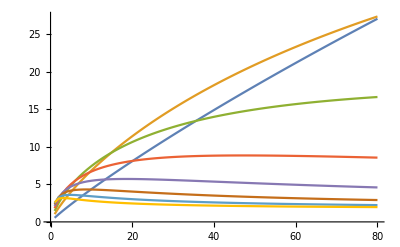

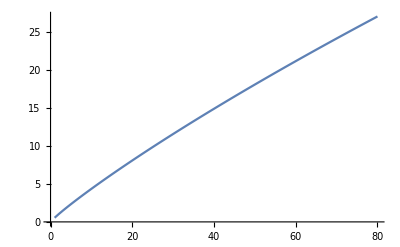

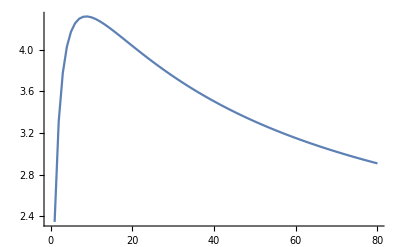

```mathematica
InvFitAcrossWNT=Table[Table[NumSolInvFit[W,270,0.9,0.9,NT,0.01,0.1,0.01],{W,25,2000,25}],{NT,0.25,2,0.25}];
ListLinePlot[InvFitAcrossWNT]
ListLinePlot[InvFitAcrossWNT[[1]]]
ListLinePlot[InvFitAcrossWNT[[6]]]
```

Increasing temperature also has a much more complex effect on R_0: when N_T is large, increasing temperature increases R_0, but when N_T is small, increasing temperature decreases R_0.

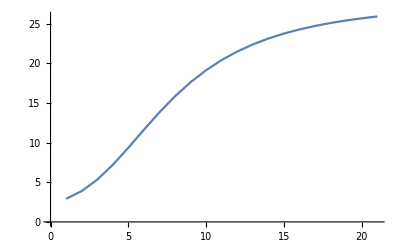

```mathematica
InvFitAcrossWT=Table[NumSolInvFit[200,T,0.9,0.9,2,0.01,0.1,0.01],{T,270,310,2}];
ListLinePlot[InvFitAcrossWT]
```

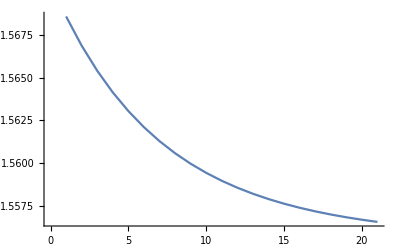

```mathematica
InvFitAcrossWT=Table[NumSolInvFit[200,T,0.9,0.9,0.1,0.01,0.1,0.01],{T,270,310,2}];
ListLinePlot[InvFitAcrossWT]
```

It also holds if you change the rate parasites are lost from the environment (here γ ranges from 0.01 to 0.1):

```mathematica
InvFitAcrossWg=Table[Table[NumSolInvFit[W,270,0.9,0.9,1,0.1,g,0.1],{W,10,1000,10}],{g,0.01,0.1,0.01}];
ListLinePlot[InvFitAcrossWg]
```

-Graphics-

It also holds if you change the ingestion rate of the definitive hosts:

```mathematica
InvFitAcrossWa=Table[Table[NumSolInvFit[W,270,0.9,0.9,1,0.1,0.01,a],{W,10,1000,10}],{a,0.05,0.5,0.05}];
ListLinePlot[InvFitAcrossWa]
```

-Graphics-

Increasing temperature decreases R_0:

```mathematica
InvFitAcrossT=Table[NumSolInvFit[100,T,0.9,0.9,1],{T,270,300,2}];
ListLinePlot[InvFitAcrossT]
```

-Graphics-

### Case 5: Trophic transmission; two specialist parasites; constant host population size; active seeking of intermediate hosts; no avoidance of infected intermediate hosts

We have assumed that parasites in the environment are consumed by all intermediate hosts, even though they only cause new infections in susceptible intermediate hosts. This makes the problem very analytically tractable.

```mathematica
dN1rdt=β (KN-N1r-N2r-N12m) P1r-c N1r (K1+K2);
dN2rdt=β (KN-N1r-N2r-N12m) P2r-c N2r (K1+K2);
dN12mdt=β (KN-N1r-N2r-N12m) P12m-c N12m (K1+K2);

dI1rdt=c(K1-I1r-I1m) N1r-μ1 I1r;
dI2rdt=c(K2-I2r-I2m) N2r-μ2 I2r;
dI1mdt=c(K1-I1r-I1m) N12m-μ1 I1m;
dI2mdt=c(K2-I2r-I2m) N12m-μ2 I2m;

dP1rdt=λ1 I1r-β P1r KN-γ P1r;
dP2rdt=λ2 I2r-β P2r KN-γ P2r;
dP12mdt=a λ1 I1m+a λ2 I2m-β P12m KN-γ P12m;
```

Find the equilibria (the brute force, all at once technique failed for this model):

```mathematica
I1rEq=Solve[dP1rdt==0,I1r][[1,1,2]]
I2rEq=Solve[dP2rdt==0,I2r][[1,1,2]]
```

(KN P1r β+P1r γ)/λ1

(KN P2r β+P2r γ)/λ2

```mathematica
N1rEq=Solve[(dI1rdt/.{I1r->I1rEq,I1m->0})==0,N1r][[1,1,2]]
N2rEq=Solve[(dI2rdt/.{I2r->I2rEq,I2m->0})==0,N2r][[1,1,2]]
```

-((KN P1r β+P1r γ) μ1)/(c (KN P1r β+P1r γ-K1 λ1))

-((KN P2r β+P2r γ) μ2)/(c (KN P2r β+P2r γ-K2 λ2))

```mathematica
P1rEq=Simplify[Solve[(dN1rdt/.{N1r->N1rEq,N2r->N2rEq,N12m->0})==0,P1r]][[2,1,2]]
P2rEq=Simplify[Solve[(dN2rdt/.{N1r->N1rEq,N2r->N2rEq,N12m->0}/.{P1r->P1rEq})==0,P2r]][[2,1,2]]
```

(-c (KN P2r β+P2r γ-K2 λ2) (K2 (KN β+γ) μ1+K1 (γ μ1+KN β (-λ1+μ1)))+K1 P2r β (KN β+γ) λ1 μ2)/(β (KN β+γ) (c KN (KN P2r β+P2r γ-K2 λ2)+P2r γ μ1-K2 λ2 μ1+P2r γ μ2+KN P2r β (μ1+μ2)))

(β (K2 λ2 μ1-K1 λ1 μ2)-c (K1 (KN β+γ) μ2+K2 (γ μ2+KN β (-λ2+μ2))))/(β (KN β+γ) (c KN+μ1+μ2))

The number of susceptible intermediate hosts at the generalist-free equilibrium is N_S=K_N-N_(1,r)-N_(2,r):

```mathematica
NsEq=Simplify[KN-Simplify[Simplify[N1rEq/.P1r->P1rEq/.P2r->P2rEq]+Simplify[N2rEq/.P2r->P2rEq]]]
```

((K1+K2) (KN β+γ) (c KN+μ1+μ2))/(c (K1+K2) (KN β+γ)+β (K1 λ1+K2 λ2))

The number of susceptible definitive hosts of species 1 and 2 at the generalist free-equilibrium are S_1=K_1-I_(1,r) and S_2=K_2-I_(2,r), respectively:

```mathematica
S1Eq=Simplify[(K1-I1r)/.I1r->I1rEq/.P1r->P1rEq/.P2r->P2rEq]
S2Eq=Simplify[(K2-I2r)/.I2r->I2rEq/.P2r->P2rEq]
```

((c (K1+K2) (KN β+γ)+β (K1 λ1+K2 λ2)) μ1)/(β λ1 (c KN+μ1+μ2))

((c (K1+K2) (KN β+γ)+β (K1 λ1+K2 λ2)) μ2)/(β λ2 (c KN+μ1+μ2))

To determine whether the generalist can invade, we need to evaluate the stability of the generalist-free equilibrium (i.e., the equilibrium when N_(12,m), I_(1,m), I_(2,m), and P_(12,m) are all equal to 0).

```mathematica
J={{D[dN1rdt,N1r],D[dN1rdt,N2r],D[dN1rdt,I1r],D[dN1rdt,I2r],D[dN1rdt,P1r],D[dN1rdt,P2r],D[dN1rdt,N12m],D[dN1rdt,I1m],D[dN1rdt,I2m],D[dN1rdt,P12m]},
{D[dN2rdt,N1r],D[dN2rdt,N2r],D[dN2rdt,I1r],D[dN2rdt,I2r],D[dN2rdt,P1r],D[dN2rdt,P2r],D[dN2rdt,N12m],D[dN2rdt,I1m],D[dN2rdt,I2m],D[dN2rdt,P12m]},
{D[dI1rdt,N1r],D[dI1rdt,N2r],D[dI1rdt,I1r],D[dI1rdt,I2r],D[dI1rdt,P1r],D[dI1rdt,P2r],D[dI1rdt,N12m],D[dI1rdt,I1m],D[dI1rdt,I2m],D[dI1rdt,P12m]},
{D[dI2rdt,N1r],D[dI2rdt,N2r],D[dI2rdt,I1r],D[dI2rdt,I2r],D[dI2rdt,P1r],D[dI2rdt,P2r],D[dI2rdt,N12m],D[dI2rdt,I1m],D[dI2rdt,I2m],D[dI2rdt,P12m]},
{D[dP1rdt,N1r],D[dP1rdt,N2r],D[dP1rdt,I1r],D[dP1rdt,I2r],D[dP1rdt,P1r],D[dP1rdt,P2r],D[dP1rdt,N12m],D[dP1rdt,I1m],D[dP1rdt,I2m],D[dP1rdt,P12m]},
{D[dP2rdt,N1r],D[dP2rdt,N2r],D[dP2rdt,I1r],D[dP2rdt,I2r],D[dP2rdt,P1r],D[dP2rdt,P2r],D[dP2rdt,N12m],D[dP2rdt,I1m],D[dP2rdt,I2m],D[dP2rdt,P12m]},
{D[dN12mdt,N1r],D[dN12mdt,N2r],D[dN12mdt,I1r],D[dN12mdt,I2r],D[dN12mdt,P1r],D[dN12mdt,P2r],D[dN12mdt,N12m],D[dN12mdt,I1m],D[dN12mdt,I2m],D[dN12mdt,P12m]},
{D[dI1mdt,N1r],D[dI1mdt,N2r],D[dI1mdt,I1r],D[dI1mdt,I2r],D[dI1mdt,P1r],D[dI1mdt,P2r],D[dI1mdt,N12m],D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,P12m]},
{D[dI2mdt,N1r],D[dI2mdt,N2r],D[dI2mdt,I1r],D[dI2mdt,I2r],D[dI2mdt,P1r],D[dI2mdt,P2r],D[dI2mdt,N12m],D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,P12m]},
{D[dP12mdt,N1r],D[dP12mdt,N2r],D[dP12mdt,I1r],D[dP12mdt,I2r],D[dP12mdt,P1r],D[dP12mdt,P2r],D[dP12mdt,N12m],D[dP12mdt,I1m],D[dP12mdt,I2m],D[dP12mdt,P12m]}}/.{N12m->0,I1m->0,I2m->0,P12m->0};
```

Stability is determined by the eigenvalues of the submatrix in the bottom right block.

```mathematica
MatrixForm[J[[7;;10,7;;10]]]
```

(-c (K1+K2) | 0 | 0 | (KN-N1r-N2r) β
c (-I1r+K1) | -μ1 | 0 | 0
c (-I2r+K2) | 0 | -μ2 | 0
0 | a λ1 | a λ2 | -KN β-γ)

Noting that K_N-N_(1,r)-N_(2,r) is just the number of susceptible intermediate hosts (N_S), K_1-I_(1,r) is the number of susceptible definitive hosts of the first species (S_1), and K_2-I_(2,r) is the number of susceptible definitive hosts of the second species (S_2), we can rewrite this matrix slightly and then apply the next generation matrix theorem to determine the stability condition for the generalist-free system.

```mathematica
F={{0,0,0,Ns β},{c S1,0,0,0},{c S2,0,0,0},{0,a λ1, a λ2,0}};
V={{c(K1+K2),0,0,0},{0,μ1,0,0},{0,0,μ2,0},{0,0,0,β KN+γ}};
MatrixForm[F-V]
Eigenvalues[Dot[F,Inverse[V]]]
```

(-c (K1+K2) | 0 | 0 | Ns β
c S1 | -μ1 | 0 | 0
c S2 | 0 | -μ2 | 0
0 | a λ1 | a λ2 | -KN β-γ)

{0,(a^(1/3) Ns^(1/3) β^(1/3) (S2 λ2 μ1+S1 λ1 μ2)^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ1^(1/3) μ2^(1/3)),-((-1)^(1/3) a^(1/3) Ns^(1/3) β^(1/3) (S2 λ2 μ1+S1 λ1 μ2)^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ1^(1/3) μ2^(1/3)),((-1)^(2/3) a^(1/3) Ns^(1/3) β^(1/3) (S2 λ2 μ1+S1 λ1 μ2)^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ1^(1/3) μ2^(1/3))}

Note that (-1)^(1/3)=-0.5+0.866025 ⅈ and (-1)^(2/3)=-0.5+0.866025 ⅈ, so whether the parasite-free equilibrium is stable or not depends entirely on the second eigenvalue. The condition for the generalist-absent equilibrium to be unstable is that this eigenvalue is greater than 1; this condition can be rewritten in a more biologically meaningful way:

(a β N_s (λ_2 S_2 μ_1 +λ_1 S_1 μ_2 ))/((K_1+K_2)(β K_N+γ) μ_1 μ_2)>1
a λ β N_s (λ_2 S_2 μ_1 +λ_1 S_1 μ_2 )>(K_1+K_2)(β K_N+γ) μ_1 μ_2
(β N_s)/(β K_N+γ) (a λ_2 μ_1 S_2+a λ_1 μ_2 S_1)>(K_1+K_2) μ_1 μ_2
(β N_s)/(β K_N+γ) (S_1/(K_1+K_2)(a λ_1)/μ_1 +S_2/(K_1+K_2)(a λ_2)/μ_2 )>1

where
(β N_s)/(β K_N+γ) is the probability that a parasite in the environment is ingested by a susceptible intermediate host; 
S_1/(K_1+K_2) and S_1/(K_1+K_2) are the probabilities that an infected intermediate host is ingested by a susceptible individual of the first and second susceptible definitive host, respectively;
(a λ_1)/μ_1 and (a λ_2)/μ_2 are the expected number of parasites shed from infected definitive hosts of the first and second species, respectively.

We define this expression as R_0, the invasion fitness of the generalist.

```mathematica
R0=(β Ns)/(β KN+γ) (S1/(K1+K2) (a λ1)/μ1+S2/(K1+K2) (a λ2)/μ2);
```

If you plug in the equilibrium values of N_S,S_1 and S_2, however, you get an incredibly simple expression for the invasion fitness:

```mathematica
Simplify[R0/.{Ns->NsEq,S1->S1Eq,S2->S2Eq}]
```

2 a

What this indicates is that as long as the fraction that shedding is reduced for the generalist (the cost of generalism) is less than 0.5, the generalist will be able to invade.

## Invasion of specialist into population with a generalist parasite

For this model, we assume that the primary and secondary host population sizes are constant at K_1 and K_2, respectively. As such, we do not need to keep track of the dynamics of both susceptible and infected hosts - we can simply track the prevalence of infection. We define I_(1r) and I_(2r) as the fraction of primary and secondary hosts infected by the specialist parasites, respectively. 

The dynamics of parasites in the environment are governed by shedding and loss, as before. The rate of shedding depends on the number of infected hosts, e.g., I_(1r)K_1. Similarly, loss due to contact with susceptible hosts depends on the number of susceptible hosts, e.g., (1-I_(1r)-I_(1m))K_1. 

The model is given below:

```mathematica
dI1rdt=β1 (1-I1r-I1m) P12r-μ1 I1r;
dI2rdt=β2 (1-I2r) P12r-μ2 I2r;
dP12rdt=a λ1 I1r K1 +a λ2 I2r K2 -β1 (1-I1r-I1m) K1  P12r-β2 (1-I2r) K2 P12r-γ P12r;

dI1mdt=β1 (1-I1r-I1m) P1m-μ1 I1m;
dP1mdt=λ1 I1m K1-β1 (1-I1r-I1m) K1 P1m -γ P1m;
```

In the absence of the specialist parasite, the equilibrium prevalences of infection are I_(1,r)= 1 -(γ μ_1)/(β_1 K_1(λ_1-μ_1)) and I_(2,r)= 1-(γ μ_2)/(β_2 K_2(λ_2-μ_2)), implying that the equilibrium number of susceptibles are (γ μ_1)/(β_1 K_1(λ_1-μ_1)) and (γ μ_2)/(β_2 K_2(λ_2-μ_2)).

```mathematica
I1rEq=Solve[dI1rdt==0,I1r]/.I1m->0
I2rEq=Solve[dI2rdt==0,I2r]
Solve[(dP12rdt/.I1rEq[[1]]/.I2rEq[[1]]/.I1m->0)==0,P12r]
```

{{I1r→(P12r β1)/(P12r β1+μ1)}}

{{I2r→(P12r β2)/(P12r β2+μ2)}}

{{P12r→0},{P12r→-1/(2 β1 β2 γ)(-a K1 β1 β2 λ1-a K2 β1 β2 λ2+K1 β1 β2 μ1+β2 γ μ1+K2 β1 β2 μ2+β1 γ μ2-√((a K1 β1 β2 λ1+a K2 β1 β2 λ2-K1 β1 β2 μ1-β2 γ μ1-K2 β1 β2 μ2-β1 γ μ2)^2+4 β1 β2 γ (a K2 β2 λ2 μ1+a K1 β1 λ1 μ2-K1 β1 μ1 μ2-K2 β2 μ1 μ2-γ μ1 μ2)))},{P12r→-1/(2 β1 β2 γ)(-a K1 β1 β2 λ1-a K2 β1 β2 λ2+K1 β1 β2 μ1+β2 γ μ1+K2 β1 β2 μ2+β1 γ μ2+√((a K1 β1 β2 λ1+a K2 β1 β2 λ2-K1 β1 β2 μ1-β2 γ μ1-K2 β1 β2 μ2-β1 γ μ2)^2+4 β1 β2 γ (a K2 β2 λ2 μ1+a K1 β1 λ1 μ2-K1 β1 μ1 μ2-K2 β2 μ1 μ2-γ μ1 μ2)))}}

Jacobian for specialist is

```mathematica
MatrixForm[Jmut={{D[dI1mdt,I1m],D[dI1mdt,P1m]},
{D[dP1mdt,I1m],D[dP1mdt,P1m]}}/.{I1m->0,P1m->0}]
F={{0,Jmut[[1,2]]},{Jmut[[2,1]],0}};
V=F-Jmut;
Eigenvalues[-V]
Inverse[V]
Dot[F,Inverse[V]]
Eigenvalues[Dot[F,Inverse[V]]]
```

(-μ1 | (1-I1r) β1
K1 λ1 | -(1-I1r) K1 β1-γ)

{-(1-I1r) K1 β1-γ,-μ1}

{{((1-I1r) K1 β1+γ)/(K1 β1 μ1-I1r K1 β1 μ1+γ μ1),0},{0,μ1/(K1 β1 μ1-I1r K1 β1 μ1+γ μ1)}}

{{0,((1-I1r) β1 μ1)/(K1 β1 μ1-I1r K1 β1 μ1+γ μ1)},{(K1 ((1-I1r) K1 β1+γ) λ1)/(K1 β1 μ1-I1r K1 β1 μ1+γ μ1),0}}

{-(√(-1+I1r) √K1 √β1 √λ1)/(√(-K1 β1+I1r K1 β1-γ) √μ1),(√(-1+I1r) √K1 √β1 √λ1)/(√(-K1 β1+I1r K1 β1-γ) √μ1)}

R_m=

```mathematica
Rm=((√(-1+I1r) √K1 √β1 √λ1)/(√(-K1 β1+I1r K1 β1-γ) √μ1))^2
```

((-1+I1r) K1 β1 λ1)/((-K1 β1+I1r K1 β1-γ) μ1)

```mathematica
D[Simplify[Rm/.I1rEq[[1]]]/.{K1->K1[W],λ1->λ1[W],P12r->P12r[W],μ1->μ1[W]},W]/.K1'[W]->-3 K1[W]/(4 W)/.λ1'[W]->3 λ1[W]/(4 W)/.μ1'[W]->- μ1[W]/(4 W)
Numerator[D[Simplify[Rm/.I1rEq[[1]]]/.{K1->K1[W],λ1->λ1[W],P12r->P12r[W],μ1->μ1[W]},W]/.K1'[W]->-3 K1[W]/(4 W)/.λ1'[W]->3 λ1[W]/(4 W)/.μ1'[W]->- μ1[W]/(4 W)]
```

-(β1 K1[W] λ1[W] (-(3 β1 K1[W] μ1[W])/(4 W)-((γ+β1 K1[W]) μ1[W])/(4 W)+β1 γ P12r'[W]))/(β1 γ P12r[W]+(γ+β1 K1[W]) μ1[W])^2

-β1 K1[W] λ1[W] (-(3 β1 K1[W] μ1[W])/(4 W)-((γ+β1 K1[W]) μ1[W])/(4 W)+β1 γ P12r'[W])

```mathematica
Solve[(dP12rdt/.{I1m->0}/.I1rEq[[1]]/.I2rEq[[1]]/.{K1->K1[W],λ1->λ1[W],K2->K2[W],λ2->λ2[W],P12r->P12r[W],μ1->μ1[W],μ2->μ2[W]})==0,γ]
Solve[Simplify[D[(dP12rdt/.{I1m->0}/.I1rEq[[1]]/.I2rEq[[1]]/.{K1->K1[W],λ1->λ1[W],K2->K2[W],λ2->λ2[W],P12r->P12r[W],μ1->μ1[W],μ2->μ2[W]}),W]/.{γ->(a β1 β2 K1[W] P12r[W] λ1[W]+a β1 β2 K2[W] P12r[W] λ2[W]-β1 β2 K1[W] P12r[W] μ1[W]+a β2 K2[W] λ2[W] μ1[W]-β1 β2 K2[W] P12r[W] μ2[W]+a β1 K1[W] λ1[W] μ2[W]-β1 K1[W] μ1[W] μ2[W]-β2 K2[W] μ1[W] μ2[W])/((β1 P12r[W]+μ1[W]) (β2 P12r[W]+μ2[W]))}/.K1'[W]->-3 K1[W]/(4 W)/.λ1'[W]->3 λ1[W]/(4 W)/.μ1'[W]->- μ1[W]/(4 W)/.K2'[W]->-3 K2[W]/(4 W)/.λ2'[W]->3 λ2[W]/(4 W)/.μ2'[W]->- μ2[W]/(4 W)]==0,P12r'[W]]//Simplify
```

{{γ→(a β1 β2 K1[W] P12r[W] λ1[W]+a β1 β2 K2[W] P12r[W] λ2[W]-β1 β2 K1[W] P12r[W] μ1[W]+a β2 K2[W] λ2[W] μ1[W]-β1 β2 K2[W] P12r[W] μ2[W]+a β1 K1[W] λ1[W] μ2[W]-β1 K1[W] μ1[W] μ2[W]-β2 K2[W] μ1[W] μ2[W])/((β1 P12r[W]+μ1[W]) (β2 P12r[W]+μ2[W]))}}

{{P12r'[W]→(β1 K1[W] μ1[W] (4 β1 P12r[W]+a λ1[W]+3 μ1[W]) (β2 P12r[W]+μ2[W])^2+β2 K2[W] (β1 P12r[W]+μ1[W])^2 μ2[W] (4 β2 P12r[W]+a λ2[W]+3 μ2[W]))/(4 W (β2^2 K2[W] (β1 P12r[W]+μ1[W])^2 (a λ2[W]-μ2[W])+β1^2 K1[W] (a λ1[W]-μ1[W]) (β2 P12r[W]+μ2[W])^2))}}

```mathematica
Simplify[-β1 K1[W] λ1[W] (-(3 β1 K1[W] μ1[W])/(4 W)-((γ+β1 K1[W]) μ1[W])/(4 W)+β1 γ P12r'[W])/.{P12r'[W]->(β1 K1[W] μ1[W] (4 β1 P12r[W]+a λ1[W]+3 μ1[W]) (β2 P12r[W]+μ2[W])^2+β2 K2[W] (β1 P12r[W]+μ1[W])^2 μ2[W] (4 β2 P12r[W]+a λ2[W]+3 μ2[W]))/(4 W (β2^2 K2[W] (β1 P12r[W]+μ1[W])^2 (a λ2[W]-μ2[W])+β1^2 K1[W] (a λ1[W]-μ1[W]) (β2 P12r[W]+μ2[W])^2))}]
```

-1/(4 W)β1 K1[W] λ1[W] (-3 β1 K1[W] μ1[W]-(γ+β1 K1[W]) μ1[W]+(β1 γ (β1 K1[W] μ1[W] (4 β1 P12r[W]+a λ1[W]+3 μ1[W]) (β2 P12r[W]+μ2[W])^2+β2 K2[W] (β1 P12r[W]+μ1[W])^2 μ2[W] (4 β2 P12r[W]+a λ2[W]+3 μ2[W])))/(β2^2 K2[W] (β1 P12r[W]+μ1[W])^2 (a λ2[W]-μ2[W])+β1^2 K1[W] (a λ1[W]-μ1[W]) (β2 P12r[W]+μ2[W])^2))

```mathematica
-3 β1 K1[W] μ1[W]-(γ+β1 K1[W]) μ1[W]+(β1 γ (β1 K1[W] μ1[W] (4 β1 P12r[W]+a λ1[W]+3 μ1[W]) (β2 P12r[W]+μ2[W])^2+β2 K2[W] (β1 P12r[W]+μ1[W])^2 μ2[W] (4 β2 P12r[W]+a λ2[W]+3 μ2[W])))/(β2^2 K2[W] (β1 P12r[W]+μ1[W])^2 (a λ2[W]-μ2[W])+β1^2 K1[W] (a λ1[W]-μ1[W]) (β2 P12r[W]+μ2[W])^2)>0
(β1 γ (β1 K1[W] μ1[W] (4 β1 P12r[W]+a λ1[W]+3 μ1[W]) (β2 P12r[W]+μ2[W])^2+β2 K2[W] (β1 P12r[W]+μ1[W])^2 μ2[W] (4 β2 P12r[W]+a λ2[W]+3 μ2[W])))/(β2^2 K2[W] (β1 P12r[W]+μ1[W])^2 (a λ2[W]-μ2[W])+β1^2 K1[W] (a λ1[W]-μ1[W]) (β2 P12r[W]+μ2[W])^2)>3 β1 K1[W] μ1[W]+(γ+β1 K1[W]) μ1[W]
Expand[(β1 γ (β1 K1[W] μ1[W] (4 β1 P12r[W]+a λ1[W]+3 μ1[W]) (β2 P12r[W]+μ2[W])^2+β2 K2[W] (β1 P12r[W]+μ1[W])^2 μ2[W] (4 β2 P12r[W]+a λ2[W]+3 μ2[W])))>(3 β1 K1[W] μ1[W]+(γ+β1 K1[W]) μ1[W]) (β2^2 K2[W] (β1 P12r[W]+μ1[W])^2 (a λ2[W]-μ2[W])+β1^2 K1[W] (a λ1[W]-μ1[W]) (β2 P12r[W]+μ2[W])^2)]//Simplify
```

-3 β1 K1[W] μ1[W]-(γ+β1 K1[W]) μ1[W]+(β1 γ (β1 K1[W] μ1[W] (4 β1 P12r[W]+a λ1[W]+3 μ1[W]) (β2 P12r[W]+μ2[W])^2+β2 K2[W] (β1 P12r[W]+μ1[W])^2 μ2[W] (4 β2 P12r[W]+a λ2[W]+3 μ2[W])))/(β2^2 K2[W] (β1 P12r[W]+μ1[W])^2 (a λ2[W]-μ2[W])+β1^2 K1[W] (a λ1[W]-μ1[W]) (β2 P12r[W]+μ2[W])^2)>0

(β1 γ (β1 K1[W] μ1[W] (4 β1 P12r[W]+a λ1[W]+3 μ1[W]) (β2 P12r[W]+μ2[W])^2+β2 K2[W] (β1 P12r[W]+μ1[W])^2 μ2[W] (4 β2 P12r[W]+a λ2[W]+3 μ2[W])))/(β2^2 K2[W] (β1 P12r[W]+μ1[W])^2 (a λ2[W]-μ2[W])+β1^2 K1[W] (a λ1[W]-μ1[W]) (β2 P12r[W]+μ2[W])^2)>3 β1 K1[W] μ1[W]+(γ+β1 K1[W]) μ1[W]

β1 γ (β1 K1[W] μ1[W] (4 β1 P12r[W]+a λ1[W]+3 μ1[W]) (β2 P12r[W]+μ2[W])^2+β2 K2[W] (β1 P12r[W]+μ1[W])^2 μ2[W] (4 β2 P12r[W]+a λ2[W]+3 μ2[W]))>(γ+4 β1 K1[W]) μ1[W] (β2^2 K2[W] (β1 P12r[W]+μ1[W])^2 (a λ2[W]-μ2[W])+β1^2 K1[W] (a λ1[W]-μ1[W]) (β2 P12r[W]+μ2[W])^2)

```mathematica
Simplify[Rm/.I1rEq[[1]]/.P12r->-1/(2 β1 β2 γ)(-a K1 β1 β2 λ1-a K2 β1 β2 λ2+K1 β1 β2 μ1+β2 γ μ1+K2 β1 β2 μ2+β1 γ μ2-√((a K1 β1 β2 λ1+a K2 β1 β2 λ2-K1 β1 β2 μ1-β2 γ μ1-K2 β1 β2 μ2-β1 γ μ2)^2+4 β1 β2 γ (a K2 β2 λ2 μ1+a K1 β1 λ1 μ2-K1 β1 μ1 μ2-K2 β2 μ1 μ2-γ μ1 μ2)))]
```

(2 K1 β1 β2 λ1)/(a K1 β1 β2 λ1+a K2 β1 β2 λ2+K1 β1 β2 μ1+β2 γ μ1-K2 β1 β2 μ2-β1 γ μ2+√((-a β1 β2 (K1 λ1+K2 λ2)+K1 β1 β2 μ1+β2 γ μ1+K2 β1 β2 μ2+β1 γ μ2)^2+4 β1 β2 γ (-(K1 β1+K2 β2+γ) μ1 μ2+a (K2 β2 λ2 μ1+K1 β1 λ1 μ2))))

```mathematica
Simplify[Rm/.I1rEq[[1]]/.P12r->-1/(2 β1 β2 γ)(-a K1 β1 β2 λ1-a K2 β1 β2 λ2+K1 β1 β2 μ1+β2 γ μ1+K2 β1 β2 μ2+β1 γ μ2-√((a K1 β1 β2 λ1+a K2 β1 β2 λ2-K1 β1 β2 μ1-β2 γ μ1-K2 β1 β2 μ2-β1 γ μ2)^2+4 β1 β2 γ (a K2 β2 λ2 μ1+a K1 β1 λ1 μ2-K1 β1 μ1 μ2-K2 β2 μ1 μ2-γ μ1 μ2)))]
```

Fitness of a generalist invading the specialist population is (a λ_1-μ_1)/(λ_1-μ_1)+(a λ_2-μ_2)/(λ_2-μ_2). Invasion of the specialist invading the system with a generalist is given above.

```mathematica
(2 K1 β1 β2 λ1)/(a K1 β1 β2 λ1+a K2 β1 β2 λ2+K1 β1 β2 μ1+β2 γ μ1-K2 β1 β2 μ2-β1 γ μ2+√((-a β1 β2 (K1 λ1+K2 λ2)+K1 β1 β2 μ1+β2 γ μ1+K2 β1 β2 μ2+β1 γ μ2)^2+4 β1 β2 γ (-(K1 β1+K2 β2+γ) μ1 μ2+a (K2 β2 λ2 μ1+K1 β1 λ1 μ2))))>
```

The Jacobian matrix for the full system is:

```mathematica
J={{D[dI1rdt,I1r],D[dI1rdt,P1r],D[dI1rdt,I2r],D[dI1rdt,P2r],D[dI1rdt,I1m],D[dI1rdt,I2m],D[dI1rdt,P12m]},
{D[dP1rdt,I1r],D[dP1rdt,P1r],D[dP1rdt,I2r],D[dP1rdt,P2r],D[dP1rdt,I1m],D[dP1rdt,I2m],D[dP1rdt,P12m]},
{D[dI2rdt,I1r],D[dI2rdt,P1r],D[dI2rdt,I2r],D[dI2rdt,P2r],D[dI2rdt,I1m],D[dI2rdt,I2m],D[dI2rdt,P12m]},
{D[dP2rdt,I1r],D[dP2rdt,P1r],D[dP2rdt,I2r],D[dP2rdt,P2r],D[dP2rdt,I1m],D[dP2rdt,I2m],D[dP2rdt,P12m]},
{D[dI1mdt,I1r],D[dI1mdt,P1r],D[dI1mdt,I2r],D[dI1mdt,P2r],D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,P12m]},
{D[dI2mdt,I1r],D[dI2mdt,P1r],D[dI2mdt,I2r],D[dI2mdt,P2r],D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,P12m]},
{D[dP12mdt,I1r],D[dP12mdt,P1r],D[dP12mdt,I2r],D[dP12mdt,P2r],D[dP12mdt,I1m],D[dP12mdt,I2m],D[dP12mdt,P12m]}}/.{I1m->0,I2m->0,P12m->0};
MatrixForm[J]
```

(-P1r β1-μ1 | (1-I1r) β1 | 0 | 0 | -P1r β1 | 0 | 0
K1 P1r β1+K1 λ1 | -(1-I1r) K1 β1-γ | 0 | 0 | K1 P1r β1 | 0 | 0
0 | 0 | -P2r β2-μ | (1-I2r) β2 | 0 | -P2r β2 | 0
0 | 0 | K2 P2r β2+K2 λ2 | -(1-I2r) K2 β2-γ | 0 | K2 P2r β2 | 0
0 | 0 | 0 | 0 | -μ1 | 0 | (1-I1r) β1
0 | 0 | 0 | 0 | 0 | -μ2 | (1-I2r) β2
0 | 0 | 0 | 0 | a K1 λ1 | a K2 λ2 | -(1-I1r) K1 β1-(1-I2r) K2 β2-γ)

As before, this has a upper block triangular structure, and whether the generalist can invade is entirely determined by the bottom left submatrix:

```mathematica
MatrixForm[J[[5;;7,5;;7]]]
```

(-μ1 | 0 | (1-I1r) β1
0 | -μ2 | (1-I2r) β2
a K1 λ1 | a K2 λ2 | -(1-I1r) K1 β1-(1-I2r) K2 β2-γ)

Applying the next generation matrix theorem, the generalist will be able to invade if the eigenvalue is greater than 1.

```mathematica
F={{0,0,(1-I1r) β1},{0,0,(1-I2r) β2},{a λ1 K1,a λ2 K2,0}};
V={{μ1,0,0},{0,μ2,0},{0,0,(1-I1r) K1 β1+(1-I2r)K2 β2+γ}};
Eigenvalues[Dot[F,Inverse[V]]]//Simplify
```

{0,-(√a √((-1+I2r) K2 β2 λ2 μ1+(-1+I1r) K1 β1 λ1 μ2))/(√((-1+I1r) K1 β1+(-1+I2r) K2 β2-γ) √μ1 √μ2),(√a √((-1+I2r) K2 β2 λ2 μ1+(-1+I1r) K1 β1 λ1 μ2))/(√((-1+I1r) K1 β1+(-1+I2r) K2 β2-γ) √μ1 √μ2)}

This condition can be simplified to
(β_1 K_1(a λ_1-μ_1))/(γ μ_1)(1-I_(1,r))+(β_2 K_2(a λ_2-μ_2))/(γ μ_2)(1-I_(2,r))>1,
which, after plugging in the generalist-free endemic equilibria for I_(1,r) and I_(2,r), simplifies to 
(a λ_1-μ_1)/(λ_1-μ_1)+(a λ_2-μ_2)/(λ_2-μ_2)>1

```mathematica
Simplify[(β1 K1(a λ1-μ1))/(γ μ1)(1-I1r)/.{I1r->(K1 β1 λ1-K1 β1 μ1-γ μ1)/(K1 β1 λ1-K1 β1 μ1)}]
Simplify[(β2 K2(a λ2-μ2))/(γ μ2)(1-I2r)/.{I2r->(K2 β2 λ2-K2 β2 μ2-γ μ2)/(K2 β2 λ2-K2 β2 μ2)}]
```

(a λ1-μ1)/(λ1-μ1)

(a λ2-μ2)/(λ2-μ2)

We can again see how changing host body size and temperature will affect invasion by looking at the derivatives of the invasion condition with respect to body size and temperature, after substituting in the allometric scaling relationships. Note that now you have a contravailing pressure of increasing body size on invasion fitness for the generalist: increasing host body size increases shedding rate, but decreases carrying capacity.

For an endoparasite, the derivative of the invasion fitness with respect to host body size is always positive because dR_0/dW=(1-a)/W((λ_1 μ_1)/(λ_1-μ_1)^2+(λ_2 μ_2)/(λ_2-μ_2)^2).

```mathematica
(D[(a λ1[W]-μ1[W])/(λ1[W]-μ1[W])+(a λ2[W] -μ2[W])/(λ2[W]-μ2[W]),W]/.{μ1'[W]->(-μ1[W])/(4 W),λ1'[W]->(3 λ1[W])/(4 W),μ2'[W]->(-μ2[W])/(4 W),λ2'[W]->(3 λ2[W])/(4 W)})==(1-a)/W((λ1[W] μ1[W])/(λ1[W]-μ1[W])^2+(λ2[W] μ2[W])/(λ2[W]-μ2[W])^2)//Simplify
```

True

Similarly, for an ectoparasite, the derivative of the invasion fitness with respect to host body size is always positive beacuse dR_0/dW=(2 (1-a))/(3 W)((λ_1 μ_1)/(λ_1-μ_1)^2+(λ_2 μ_2)/(λ_2-μ_2)^2).

```mathematica
Simplify[D[(a λ1[W]-μ1[W])/(λ1[W]-μ1[W])+(a λ2[W]-μ2[W])/(λ2[W]-μ2[W]),W]/.{μ1'[W]->(-μ1[W])/(4 W),λ1'[W]->(5 λ1[W])/(12 W),μ2'[W]->(-μ2[W])/(4 W),λ2'[W]->(5 λ2[W])/(12 W)}]==(2 (1-a))/(3 W)((λ1[W] μ1[W])/(λ1[W]-μ1[W])^2+(λ2[W] μ2[W])/(λ2[W]-μ2[W])^2)//Simplify
```

True

For both endoparasites and ectoparasites, the derivative of the invasion fitness with respect to temperature is zero, as before.

```mathematica
D[(a λ1[T] -μ1[T])/(λ1[T] -μ1[T])+(a λ2[T] -μ2[T])/(λ2[T] -μ2[T]),T]/.{μ2'[T]->(Ε μ2[T])/(k T^2),λ2'[T]->(Ε λ2[T])/(k T^2),μ1'[T]->(Ε μ1[T])/(k T^2),λ1'[T]->(Ε λ1[T])/(k T^2)}//Simplify
```

0